# Scalar tachyonic instabilities in gravitational backgrounds: Existence and growth rate. Numerical Analysis and Construction Figures File

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];

Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Part::partw,NonlinearModelFit::cvmit];
```

## Figure 1

```mathematica
(* Plots of the critical values Subscript[ξ, H,C](q^2) (with 0<q^2<9/8) and Subscript[ξ, -,H](q^2) (with 1<q^2<9/8) as a function of q^2 at which Subscript[r, H]=Subscript[r, C] and r_-=Subscript[r, H] 
respectively. The colored shaded regions correspond to the physical corresponding regions of Fig.6 showed below. Also plot of the 
metric function f(r) as a function of r in the case of the RN-dS/SdS/RN spacetimes for critical value Subscript[ξ, H,C] (when event and 
cosmological horizons coincide) and Subscript[ξ, -,H] (when inner Cauchy and outer event horizons coincide). The blue, green and red solid curves 
correspond to RN-dS spacetime while the purple and orange dashed curves correspond to  RN and SdS spacetime respectively *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

(* It is used to find the critical values  Subscript[ξ, -,H](q^2} (with 1<q^2<9/8) and Subscript[ξ, H,C](q^2} (with 0<q^2<9/8) *)

Simplify[NSolve[1-qq2-xi+4/3  xi  qq2 - 8/27 xi qq2^2-16/729  xi^2 qq2^3==0,xi],Reals]
```

{{xi→(-22.7813+30.375 qq2-6.75 qq2^2-19.0919 √(-1. (-1.125+1. qq2)^3))/qq2^3},{xi→(-22.7813+30.375 qq2-6.75 qq2^2+19.0919 √(-1. (-1.125+1. qq2)^3))/qq2^3}}

```mathematica
Clear[s,xi,m,mm2,qq2]
```

```mathematica
(*It is used to find the critical values Subscript[ξ, -,H]  and  Subscript[ξ, H,C] for q^2=1.02 *)
```

```mathematica
m=1; qq2=1.02;
```

```mathematica
Simplify[NSolve[m^2-qq2-xi+4/3  xi  qq2 - 8/27 xi qq2^2-16/729  xi^2 qq2^3==0,xi],Reals]
```

{{xi→0.49846},{xi→1.72269}}

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

Clear[s,xi,m,mm2]
```

```mathematica
(* Plot of the metric function f(r) as a function of r in the case of the RN-dS spacetime for critical value Subscript[ξ, -,H] (when inner Cauchy and outer event 
horizons coincide)  for  q^2=1.02 *)
```

```mathematica
(* Metric function f *)
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
```

```mathematica
m=1;xi=0.49846014658767457;qq2=1.02;
```

```mathematica
(* Horizons *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.25259,1.04174,1.04174,6.16911}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
horin=ss[[Length[ss]-2]]
```

6.16911

1.04174

1.04174

```mathematica
plhorinev=Plot[aa[r],{r,0,50},PlotStyle->{Darker[Green],Thick}, PlotRange->{{0,15},{-2,3}}];
```

```mathematica
Clear[s,xi,m,mm2,qq2]
```

```mathematica
(* Plot of the metric function f(r) as a function of r in the case of the RN-dS spacetime for critical value Subscript[ξ, H,C] (when event and cosmological horizons 
coincide) and for q^2=1.02 *)
```

```mathematica
(* Metric function f *)
```

```mathematica
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
```

```mathematica
m=1;xi=1.7226878281731584;qq2=1.02;
```

```mathematica
(* Horizons *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-4.78733,0.870812,1.95826,1.95826}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
horin=ss[[Length[ss]-2]]
```

1.95826

1.95826

0.870812

```mathematica
plhorevcos=Plot[aa[r],{r,0,50}, PlotStyle->{Darker[Blue],Thick},PlotRange->{{0,15},{-2,3}}];
```

```mathematica
Clear[s,xi,m,mm2,qq2]
```

```mathematica
(* Plot of the critical values Subscript[ξ, H,C](q^2} (with 0<q^2<9/8) (blue curve) and Subscript[ξ, -,H](q^2} (with 1<q^2<9/8)(green curve) as a function of q^2 at which Subscript[r, H]=Subscript[r, C] 
and r_-=Subscript[r, CH] respectively *)
```

```mathematica
m=1;
```

```mathematica
(*It is used to find the critical values Subscript[ξ, -,H]  and  Subscript[ξ, H,C]  as a function of q^2 *)
```

```mathematica
ximax=Simplify[NSolve[m^2-qq2-xi+4/3  xi  qq2 - 8/27 xi qq2^2-16/729  xi^2 qq2^3==0,xi],Reals]
```

{{xi→(-22.7813+30.375 qq2-6.75 qq2^2-19.0919 √(-1. (-1.125+1. qq2)^3))/qq2^3},{xi→(-22.7813+30.375 qq2-6.75 qq2^2+19.0919 √(-1. (-1.125+1. qq2)^3))/qq2^3}}

```mathematica
ximax[[2,1,2]]
```

(-22.7813+30.375 qq2-6.75 qq2^2+19.0919 √(-1. (-1.125+1. qq2)^3))/qq2^3

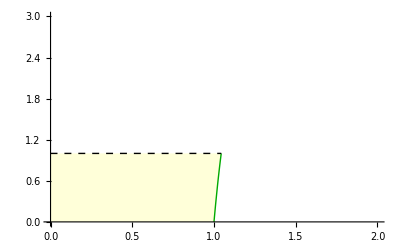

```mathematica
pl1=Plot[{ximax[[1,1,2]],1},{qq2,0,1.04423},PlotStyle->{{Darker[Green],Thick},{Black,Dashed,Thin}},Filling->{1->{{2},LightYellow}},PlotRange->{{0,2},{0,3}}]
```

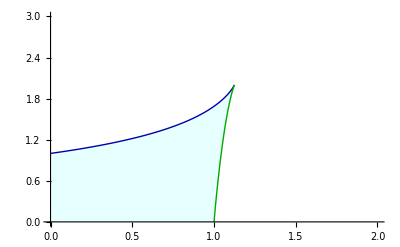

```mathematica
pl2=Plot[{ximax[[2,1,2]],ximax[[1,1,2]]},{qq2,0.001,1.125},PlotStyle->{{Darker[Blue],Thick},{Darker[Green],Thick}},Filling->{1->{{2},LightCyan}},PlotRange->{{0,2},{0,3}}]
```

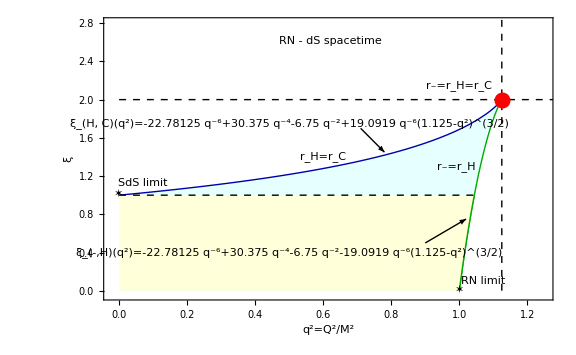

```mathematica
sximax=Show[pl2,pl1,Graphics[{Inset[" RN - dS spacetime",{0.62,2.61},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" ξ_(H, C)(q^2)=-22.78125q^-6+30.375q^-4-6.75q^-2+19.0919q^-6(1.125-q^2)^(3/2)",{0.5,1.75},BaseStyle->{Italic,Bold,Darker[Blue],FontFamily->"Times",11}]}],Graphics[{Inset[" ξ_(-,H)(q^2)=-22.78125q^-6+30.375q^-4-6.75q^-2-19.0919q^-6(1.125-q^2)^(3/2)",{0.5,0.4},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",11}]}],Graphics[{Inset[" SdS limit",{0.07,1.13},BaseStyle->{Italic,Bold,Orange,FontFamily->"Times",14}]}],Graphics[{Inset[" RN limit",{1.07,0.1},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",14}]}],Graphics[{Inset["✶",{0,1.01},BaseStyle->{Bold,Orange,FontFamily->"Times",26}]}],Graphics[{Inset["✶",{1,0.01},BaseStyle->{Bold,Purple,FontFamily->"Times",26}]}],Graphics[{Inset[" r_H=r_C",{0.6,1.4},BaseStyle->{Italic,Bold,Darker[Blue],FontFamily->"Times",16}]}],Graphics[{Inset[" r_-=r_H",{0.99,1.3},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",16}]}],Graphics[{Inset[" r_-=r_H=r_C",{1,2.15},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",16}]}],Frame->True,FrameLabel->{"q^2=Q^2/M^2","ξ"},Epilog->{{Thin,Black,Arrowheads[0.01],Arrow[{{0.9,0.5},{1.02,0.75}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{0.71,1.7},{0.78,1.45}}]},{Dashed,Black,Line[{{0,2},{2,2}}]},{Dashed,Black,Line[{{1.125,0},{1.125,7}}]},{PointSize[0.02],Red,Point[{1.125,2}]}},Axes->None,FrameStyle->Directive[Black,Thick],PlotRange->{{-0.02,1.25},{-0.04,2.8}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

```mathematica
Clear[s,xi,m,mm2,qq2]
```

```mathematica
(* Plot of the metric function f(r) as a function of r in the case of the SdS spacetime (q^2=0) for critical value Subscript[ξ, H,C] (when event and cosmological horizons 
coincide) *)
```

```mathematica
(* Metric function f *)
```

```mathematica
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
```

```mathematica
m=1; qq2=0;
```

```mathematica
(*It is used to find the critical values Subscript[ξ, H,C]  for q^2=0 *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]];
```

```mathematica
horcos=ss[[Length[ss]]];
horev=ss[[Length[ss]-1]];
horneg=ss[[Length[ss]-2]];
```

```mathematica
condsds=Simplify[NSolve[horcos==horev,xi],Reals]
```

{{xi→1.}}

```mathematica
m=1;xi=1;qq2=0;
```

```mathematica
(* Horizons *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-6.,3.,3.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
horneg=ss[[Length[ss]-2]]
```

3.

3.

-6.

```mathematica
plsds=Plot[aa[r],{r,0,50}, PlotStyle->{Orange,Dashed,Thick},PlotRange->{{0,15},{-2,1}}];
```

```mathematica
(* Plot of the metric function f(r) as a function of r in the case of the RN spacetime (ξ=0) for critical value Subscript[ξ, -,H] (when inner Cauchy and outer event 
horizons coincide) *)
```

```mathematica
Clear[s,xi,m,mm2,qq2]
```

```mathematica
(* Metric function *)
```

```mathematica
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
```

```mathematica
m=1; xi=0;
```

```mathematica
(*It is used to find the critical values Subscript[q^2, H,C]  for ξ=0 *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]];
```

```mathematica
horev=ss[[Length[ss]]];
horin=ss[[Length[ss]-1]];
horneg=ss[[Length[ss]-2]];
```

```mathematica
condsds=Simplify[NSolve[horin==horev,xi],Reals]
```

{{qq2→1.}}

```mathematica
m=1;xi=0;qq2=1;
```

```mathematica
(* Horizons *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{1.,1.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

1.

1.

```mathematica
plrn=Plot[aa[r],{r,0,50},  PlotStyle->{Purple,Dashed,Thick},PlotRange->{{0,15},{-2,3}}];
```

```mathematica
(* Plot of the metric function f(r) as a function of r in the case of the RN-dS spacetime  for critical values Subscript[ξ, -,H,c] =2 and  q^2=9/8 (when inner Cauchy,
 outer event and cosmogolical horizons coincide) *)
```

```mathematica
Clear[s,xi,m,mm2,qq2]
```

```mathematica
m=1;xi=2;qq2=1.125;
```

```mathematica
(* Horizons *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-4.5,1.5,1.5,1.5}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
horin=ss[[Length[ss]-2]]
```

1.5

1.5

1.5

```mathematica
plextr=Plot[aa[r],{r,0,50},PlotStyle->{Red,Thick}, PlotRange->{{0,15},{-2,3}}];
```

```mathematica
(* Plot of the metric function f(r) as a function of r in the case of the  RN-dS/SdS/RN spacetime  *)
```

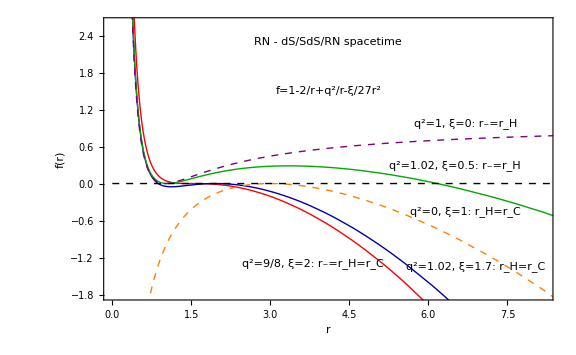

```mathematica
sfr=Show[plextr,plhorevcos,plhorinev,plrn,plsds,Graphics[{Inset[" RN - dS/SdS/RN spacetime",{4.1,2.3},BaseStyle->{Italic,Black,FontFamily->"Times",18}]}],Graphics[{Inset[Framed["f=1-2/r+q^2/r-ξ/27r^2"],{4.1,1.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["q^2=0, ξ=1: r_H=r_C",{6.7,-0.45},BaseStyle->{Italic,Bold,Orange,FontFamily->"Times",12}]}],Graphics[{Inset["q^2=1, ξ=0: r_-=r_H",{6.7,0.98},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["q^2=1.02, ξ=1.7: r_H=r_C",{6.9,-1.35},BaseStyle->{Italic,Bold,Darker[Blue],FontFamily->"Times",12}]}],Graphics[{Inset["q^2=1.02, ξ=0.5: r_-=r_H",{6.5,0.29},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",12}]}],Graphics[{Inset["q^2=9/8, ξ=2: r_-=r_H=r_C",{3.8,-1.3},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Frame->True,FrameLabel->{"r","f(r)"},Axes->None,FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},PlotRange->{{0,8.2},{-1.8,2.6}},ImageSize->Large]
```

```mathematica
(* Figure 1  *)
```

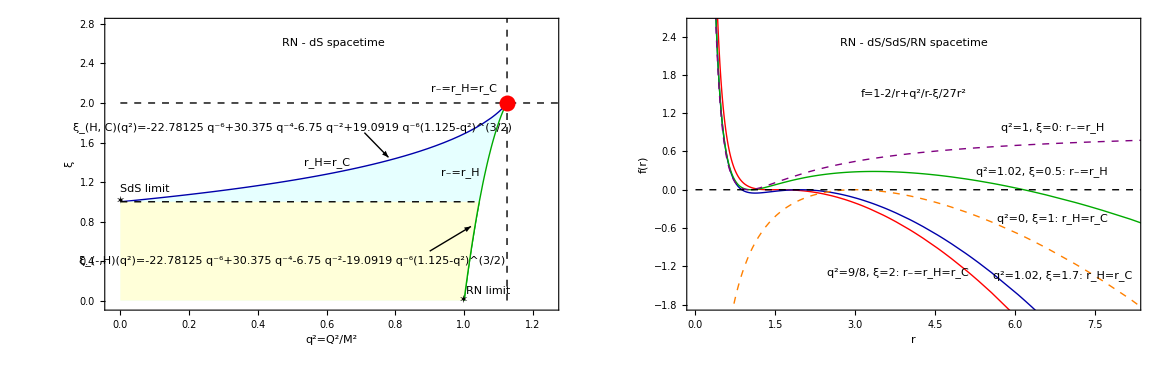

```mathematica
figximaxfr=GraphicsGrid[{{sximax,sfr}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"figximaxfr.pdf",figximaxfr,ImageResolution->1000];
```

## Figure 2

```mathematica
(* Plots of the m^2 Μ^2 dependent  Regge-Wheeler dimensionless potentials VΜ^2 and V_*Μ^2 as a function of r/M and r_*/M respectively in the case of the 
Schwarzschild-deSitter (SdS)(Q=0) (red curves) and RN-dS (Q=M=0.9) (blue curves) spacetimes for angular scale l=0 and dimensionless 
parameter fixed to ξ=0.5. The solid curves correspond to the critical value of the scalar field mass Subscript[m, cr]^2 Μ^2=0. The right panel demonstrates 
the process for identifying the zero eigenvalue eigenstat i.e. setting Ω=0 in equation (2.22) and increasing the dimensionless parameter 
m^2 Μ^2  until the solution Subscript[u, 0]  satisfies oth end boundary conditions (3.7) and (3.8). For the critical value Subscript[m, cr]^2 Μ^2 the boundary conditions 
(3.9) and (3.10). This value of m^2 Μ^2 is the critical value forthe considered value of ξ  *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

Clear[s,xi,m,mm2]
```

```mathematica
(* Plot of the m^2 Μ^2 dependent  Regge-Wheeler potential V as a function of r/M in the case of the Schwarzschild-deSitter (SdS)(Q=0)(red curves) 
and RN-dS (Q=M=0.9) (blue curves) spacetimes for angular scale l=0 and dimensionless parameter fixed to ξ= 0.5 *)
```

```mathematica
(* Metric function f *)
```

```mathematica
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
daar=D[aa[r],r]/r;
```

```mathematica
m=1;xi=0.5;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr05is=Plot[V[r,1,0.5,0,-0.03],{r,0,59}, PlotStyle->{Red,Dashed,Thick},PlotRange->{{0,59},{-0.08,0.09}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvr05isb=Plot[V[r,1,0.5,0,-0.1],{r,0,59}, PlotStyle->{Red,DotDashed,Thick},PlotRange->{{0,59},{-0.08,0.09}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvr05cr=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Red,Thick},PlotRange->{{0,37},{-0.08,0.095}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvr05st=Plot[V[r,1,0.5,0,0.03],{r,0,40},PlotStyle->{Red,Dotted,Thick}, PlotRange->{{0,40},{-0.08,0.1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0.5;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr05isq=Plot[V[r,1,0.5,0,-0.03],{r,0,59}, PlotStyle->{Blue,Dashed,Thick},PlotRange->{{0,20},{-0.1,1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvr05isqb=Plot[V[r,1,0.5,0,-0.1],{r,0,59}, PlotStyle->{Blue,DotDashed,Thick},PlotRange->{{0,20},{-0.1,1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvr05crq=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Blue,Thick},PlotRange->{{0,20},{-0.1,01}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvr05stq=Plot[V[r,1,0.5,0,0.03],{r,0,40},PlotStyle->{Blue,Dotted,Thick}, PlotRange->{{0,20},{-0.1,0.2}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

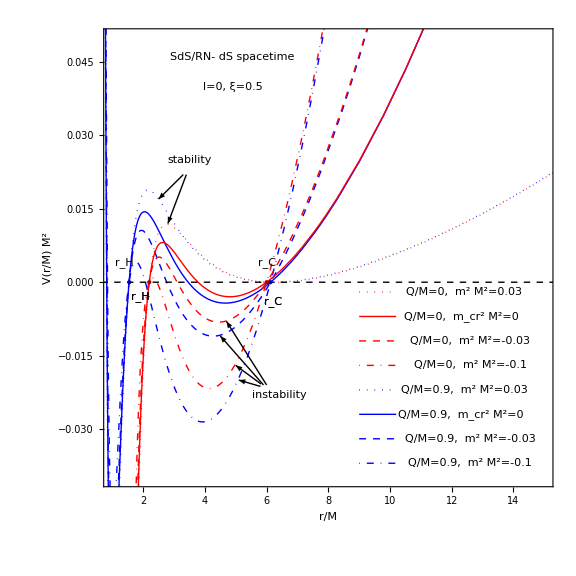

```mathematica
splvr05q=Show[plvr05isq,plvr05isqb,plvr05crq,plvr05stq,plvr05is,plvr05isb,plvr05cr,plvr05st,Graphics[{Inset[" SdS/RN- dS spacetime  ",{4.9,0.046},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["  l=0, ξ=0.5  ",{4.9,0.04},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" stability",{3.5,0.025},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" instability",{6.4,-0.023},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" Q/M=0,  m^2Μ^2=0.03",{12.4,-0.002},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  m_cr^2Μ^2=0",{12.3,-0.007},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  m^2Μ^2=-0.03 ",{12.6,-0.012},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  m^2Μ^2=-0.1 ",{12.6,-0.017},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset[" Q/M=0.9,  m^2Μ^2=0.03",{12.4,-0.022},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9,  m_cr^2Μ^2=0",{12.3,-0.027},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9,  m^2Μ^2=-0.03 ",{12.6,-0.032},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9,  m^2Μ^2=-0.1 ",{12.6,-0.037},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["r_H ",{1.4,0.004},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["r_H ",{1.9,-0.003},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["r_C",{6.2,-0.004},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["r_C",{6.,0.004},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["r_H ",{1.9,-0.003},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["r_C",{6.2,-0.004},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Epilog->{{Thin,Black,Arrowheads[0.01],Arrow[{{5.82,-0.0208},{5,-0.017}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{5.8,-0.0213},{5.1,-0.02}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{5.9,-0.021},{4.5,-0.011}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{6,-0.021},{4.7,-0.008}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{3.4,0.022},{2.8,0.012}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{3.3,0.022},{2.5,0.017}}]},{Dashing[0.008],Black,Line[{{-6,0},{70,0}}]},{PointSize[Large],Darker[Blue],Point[{1.55,0}]},{PointSize[Large],Darker[Red],Point[{2.196,0}]},{PointSize[Large],Darker[Blue],Point[{6.125,0}]},{PointSize[Large],Darker[Red],Point[{6.,0}]},{Thick,Red,Line[{{9,-0.007},{10.2,-0.007}}]},{Dashed,Thick,Red,Line[{{9,-0.012},{10.2,-0.012}}]},{DotDashed,Thick,Red,Line[{{9,-0.017},{10.2,-0.017}}]},{Dotted,Thick,Red,Line[{{9,-0.002},{10.2,-0.002}}]},{Thick,Blue,Line[{{9,-0.027},{10.2,-0.027}}]},{Dashed,Thick,Blue,Line[{{9,-0.032},{10.2,-0.032}}]},{{DotDashed,Thick,Blue,Line[{{9,-0.037},{10.2,-0.037}}]},Dotted,Thick,Blue,Line[{{9,-0.022},{10.2,-0.022}}]}},Frame->True,FrameLabel->{"r/M","V(r/M) M^2"},Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{1,15},{-0.04,0.05}},ImageSize->Large]
```

```mathematica
(* Plot of the m^2 Μ^2 dependent  Regge-Wheeler potential V_* as a function of  r_*/M  in the case of the  Schwarzschild-deSitter (SdS)(Q=0) (red curves) and 
RN-dS (Q=M=0.9) (blue curves) spacetimes for angular scale l=0 and dimensionless parameter fixed to ξ= 0.5 and plot of the radial zero mode solution 
of Schrodinger like equation (2.22) *)
```

```mathematica
m=1;xi=0.5;mm2=0;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.19615,2.19615,6.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.

2.19615

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.19615

5.99931

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05cr=Plot[ff[x],{x,-50,50},PlotStyle->{Red,Thick},PlotRange->{{-60,60},{-0.01,0.01}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;

(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05cr=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.0000532041}

```mathematica
m=1;xi=0.5;mm2=-0.03;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.19615,2.19615,6.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.

2.19615

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.19615

5.99931

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05is=Plot[ff[x],{x,-50,50},PlotStyle->{Red,Dashed,Thick},PlotRange->{{-60,60},{-0.01,0.01}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the  radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05is=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Red,Dashed,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{-0.0927362}

```mathematica
m=1;xi=0.5;mm2=-0.1;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.19615,2.19615,6.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.

2.19615

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.19615

5.99931

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05isb=Plot[ff[x],{x,-50,50},PlotStyle->{Red,DotDashed,Thick},PlotRange->{{-60,60},{-0.06,0.01}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the  radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05isb=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Red,DotDashed,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{-0.0491886}

```mathematica
m=1;xi=0.5;mm2=0.03;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.19615,2.19615,6.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.

2.19615

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.19615

5.99931

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05st=Plot[ff[x],{x,-50,50},PlotStyle->{Red,Dotted,Thick},PlotRange->{{-60,60},{-0.01,0.02}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the  radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05st=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Red,Dotted,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.246055}

```mathematica
m=1;xi=0.5;mm2=0;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.23195,0.561996,1.54315,6.12681}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.12681

1.54315

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.54315

6.12639

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05crq=Plot[ff[x],{x,-50,50},PlotStyle->{Blue,Thick},PlotRange->{{-60,60},{-0.01,0.02}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05crq=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.0000498716}

```mathematica
m=1;xi=0.5;mm2=-0.03;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.23195,0.561996,1.54315,6.12681}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.12681

1.54315

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.54315

6.12639

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05isq=Plot[ff[x],{x,-50,50},PlotStyle->{Blue,Dashed,Thick},PlotRange->{{-60,60},{-0.025,0.025}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)
bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the  radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05isq=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Blue,Dashed,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{-0.138341}

```mathematica
m=1;xi=0.5;mm2=-0.1;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.23195,0.561996,1.54315,6.12681}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.12681

1.54315

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.54315

6.12639

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05isqb=Plot[ff[x],{x,-50,50},PlotStyle->{Blue,DotDashed,Thick},PlotRange->{{-60,60},{-0.06,0.025}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the  radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05isqb=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Blue,DotDashed,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{-0.0663234}

```mathematica
m=1;xi=0.5;mm2=0.03;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.23195,0.561996,1.54315,6.12681}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.12681

1.54315

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.54315

6.12639

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05stq=Plot[ff[x],{x,-50,50},PlotStyle->{Blue,Dotted,Thick},PlotRange->{{-60,60},{-0.02,0.025}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05stq=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Blue,Dotted,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.387674}

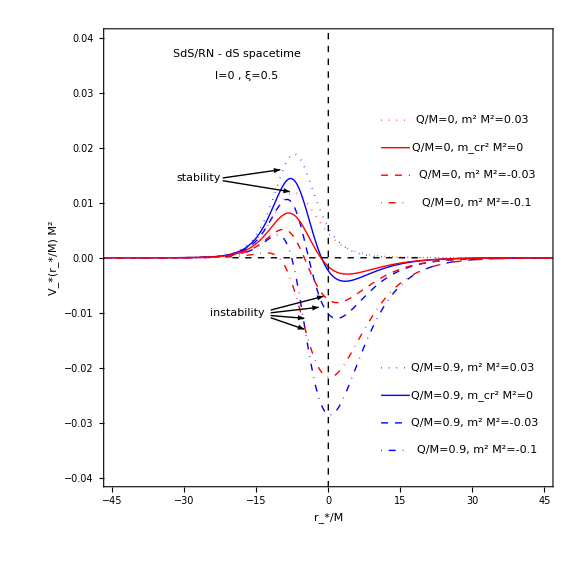

```mathematica
splvrt05q=Show[plvrt05crq,plvrt05isq,plvrt05isqb,plvrt05stq,plvrt05cr,plvrt05is,plvrt05isb,plvrt05st,Graphics[{Inset[" SdS/RN - dS spacetime ",{-19,0.037},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" l=0 , ξ=0.5 ",{-17,0.033},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" stability",{-27,0.0145},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" instability",{-19,-0.01},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Q/M=0, m^2Μ^2=0.03",{30,0.025},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0, m_cr^2Μ^2=0 ",{29,0.020},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0, m^2Μ^2=-0.03",{31,0.015},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0, m^2Μ^2=-0.1",{31,0.01},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m^2Μ^2=0.03",{30,-0.02},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m_cr^2Μ^2=0 ",{30,-0.025},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m^2Μ^2=-0.03",{30.5,-0.030},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m^2Μ^2=-0.1",{31,-0.035},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Epilog->{{Thin,Black,Arrowheads[0.01],Arrow[{{-22,0.014},{-8,0.012}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{-22,0.0145},{-10,0.016}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{-12,-0.01},{-2,-0.009}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{-12,-0.0095},{-1,-0.007}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{-12,-0.0105},{-5,-0.011}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{-12,-0.0109},{-5,-0.013}}]},{Dashing[0.008],Black,Line[{{-20,0},{20,0}}]},{Dashing[0.008],Black,Line[{{0,-1},{0,1}}]},{Thick,Red,Line[{{11,0.02},{17,0.02}}]},{Dashed,Thick,Red,Line[{{11,0.015},{17,0.015}}]},{DotDashed,Thick,Red,Line[{{11,0.01},{17,0.01}}]},{Dotted,Thick,Red,Line[{{11.,0.025},{17,0.025}}]},{Thick,Blue,Line[{{11,-0.025},{17,-0.025}}]},{Dashed,Thick,Blue,Line[{{11,-0.03},{16.5,-0.03}}]},{DotDashed,Thick,Blue,Line[{{11,-0.035},{16.5,-0.035}}]},{Dotted,Thick,Blue,Line[{{11.,-0.02},{17,-0.02}}]}},Frame->True,FrameLabel->{"r_*/M","V_*(r_*/M) M^2"},Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-45,45},{-0.04,0.04}},ImageSize->Large]
```

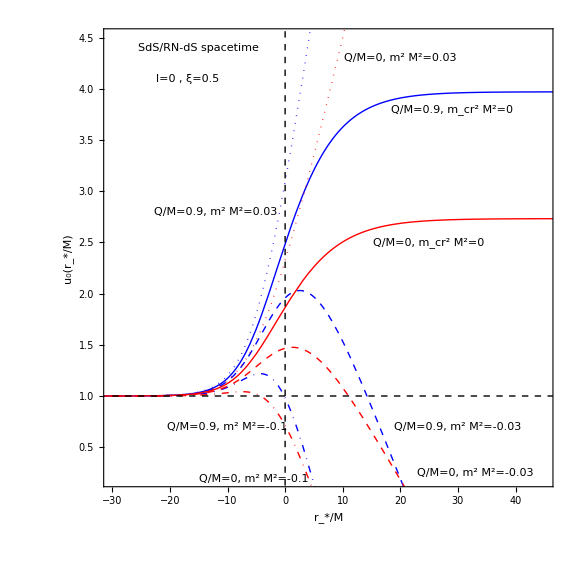

```mathematica
splu05q=Show[plu05crq,plu05stq,plu05isq,plu05isqb,plu05cr,plu05st,plu05is,plu05isb,Graphics[{Inset[" SdS/RN-dS spacetime  ",{-15,4.4},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" l=0 , ξ=0.5  ",{-17,4.1},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["Q/M=0, m^2Μ^2=0.03",{20,4.3},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0, m_cr^2Μ^2=0",{25,2.5},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0, m^2Μ^2=-0.03 ",{33,0.25},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0, m^2Μ^2=-0.1 ",{-5.5,0.19},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m^2Μ^2=0.03",{-12,2.8},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m_cr^2Μ^2=0",{29,3.8},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m^2Μ^2=-0.03 ",{30,0.7},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, m^2Μ^2=-0.1 ",{-10,0.7},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Epilog->{{Dashing[0.008],Black,Line[{{-30,1},{60,1}}]},{Dashing[0.008],Black,Line[{{0,0},{0,5}}]}},FrameLabel->{"r_*/M","u_0(r_*/M)"},Frame->True,Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-30,45},{0.2,4.5}},ImageSize->Large]
```

```mathematica
(* Figure 2  *)
```

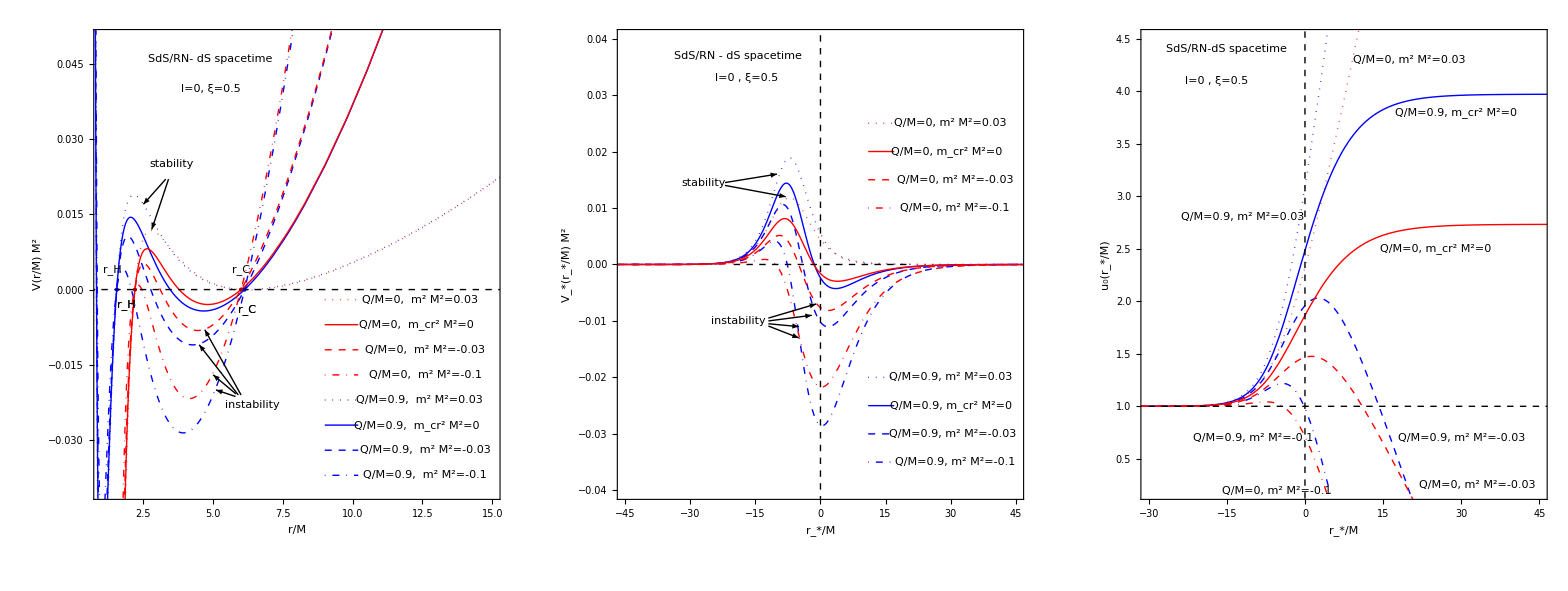

```mathematica
fig1=GraphicsGrid[{{splvr05q,splvrt05q,splu05q}},Spacings->3]
```

```mathematica
Export[NotebookDirectory[]<>"fig1.pdf",fig1,ImageResolution->1000];
```

## Figure 3

```mathematica
(* Plots of the ξ dependent  Regge-Wheeler potentials V and  V_* as a function of r/M and r_*/M respectively in the case of the SdS (solid 
curves) and RN-dS (dashed curves) spacetimes for angular scale l=0 and critical value for m^2=Subscript[m, cr]^2=0. Also plot of the radial function 
Subscript[u, 0](r_*/M ) which is the radial zero mode solution of Schrodinger like equation (2.22) with Ω=0 and boundary conditions (3.7) and (3.8) 
at large negative r_*  *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

Clear[s,xi,m,mm2]
```

```mathematica
(* Plot of the ξ dependent  Regge-Wheeler potentials V as a function of r/M  in the case of the SdS (solid curves) and RN-dS 
(dashed curves) spacetimes for angular scale l=0 and critical value for m^2=Subscript[m, cr]^2=0 *)
```

```mathematica
(* Metric function f *)
```

```mathematica
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
daar=D[aa[r],r]/r;
```

```mathematica
m=1;xi=0.1;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr01cr=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Green,Thick},PlotRange->{{0,37},{-0.08,0.095}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0.1;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr01crq=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Green,Dashed,Thick},PlotRange->{{0,20},{-0.1,01}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0.5;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr05cr=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Red,Thick},PlotRange->{{0,37},{-0.08,0.095}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0.5;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr05crq=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Red,Dashed,Thick},PlotRange->{{0,20},{-0.1,01}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0.9;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr09cr=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Blue,Thick},PlotRange->{{0,37},{-0.08,0.095}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0.9;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
plvr09crq=Plot[V[r,1,0.5,0,0],{r,0,37},  PlotStyle->{Blue,Dashed,Thick},PlotRange->{{0,20},{-0.1,01}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
plvrschcr=Plot[V[r,1,0,0,0],{r,0,37},  PlotStyle->{Dotted,Darker[Brown],Thick},PlotRange->{{0,37},{-0.08,0.095}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;xi=0;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
plvrschcrq=Plot[V[r,1,0,0,0],{r,0,37},  PlotStyle->{Dotted,Magenta,Thick},PlotRange->{{0,37},{-0.08,0.095}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

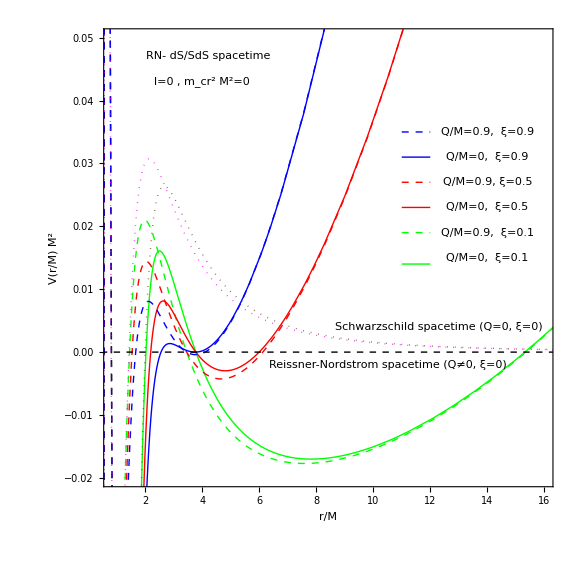

```mathematica
splvrmcr=Show[plvr01crq,plvr01cr,plvr05crq,plvr05cr,plvr09crq,plvr09cr,plvrschcr,plvrschcrq,Graphics[{Inset[" RN- dS/SdS spacetime  ",{4.2,0.047},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["  l=0 , m_cr^2Μ^2=0 ",{4,0.043},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["Schwarzschild spacetime (Q=0, ξ=0)",{12.3,0.004},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",13}]}],Graphics[{Inset["Reissner-Nordstrom spacetime (Q≠0, ξ=0)",{10.5 ,-0.002},BaseStyle->{Bold,Magenta,FontFamily->"Times",13}]}],Graphics[{Inset[" Q/M=0.9,  ξ=0.9",{14,0.035},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  ξ=0.9",{14,0.031},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, ξ=0.5 ",{14,0.027},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset[" Q/M=0,  ξ=0.5",{14,0.023},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9,  ξ=0.1",{14,0.019},BaseStyle->{Bold,Green,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  ξ=0.1 ",{14,0.015},BaseStyle->{Bold,Green,FontFamily->"Times",13}]}],Frame->True,FrameLabel->{"r/M","V(r/M) M^2"},Axes->None,AspectRatio->1,Epilog->{{Dashing[0.008],Black,Line[{{0,0},{20,0}}]},{Thick,Dashed,Blue,Line[{{11,0.035},{12,0.035}}]},{Thick,Blue,Line[{{11,0.031},{12,0.031}}]},{Dashed,Thick,Red,Line[{{11,0.027},{12,0.027}}]},{Thick,Red,Line[{{11,0.023},{12,0.023}}]},{Thick,Green,Line[{{11,0.014},{12,0.014}}]},{Dashed,Thick,Green,Line[{{11,0.019},{12,0.019}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{0.85,16},{-0.02,0.05}},ImageSize->Large]
```

```mathematica
(* Plot of the ξ dependent  Regge-Wheeler potentials  V_* as a function of  r_*/M respectively in the case of the SdS (solid 
curves) and RN-dS (dashed curves) spacetimes for angular scale l=0 and critical value for m^2=Subscript[m, cr]^2=0. Also plot of the radial function 
Subscript[u, 0](r_*/M ) which is the radial zero mode solution of Schrodinger like equation (2.22) with Ω=0 and boundary conditions (3.7) and (3.8) 
at large negative r_*  *)
```

```mathematica
m=1;xi=0.5;mm2=0;qq2=0;

(*  Regge-Wheeler potential V  *)

V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.19615,2.19615,6.}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.

2.19615

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.19615

5.99931

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05cr=Plot[ff[x],{x,-50,50},PlotStyle->{Red,Thick},PlotRange->{{-60,60},{-0.01,0.01}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05cr=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.0000532041}

```mathematica
m=1;xi=0.5;mm2=0;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-8.23195,0.561996,1.54315,6.12681}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

6.12681

1.54315

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.54315

6.12639

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt05crq=Plot[ff[x],{x,-50,50},PlotStyle->{Red,Dashed,Thick},PlotRange->{{-60,60},{-0.01,0.03}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu05crq=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Red,Dashed,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.0000498716}

```mathematica
m=1;xi=0.1;mm2=0;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-17.3528,2.03103,15.3217}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

15.3217

2.03103

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.03103

15.2732

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Red,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt01cr=Plot[ff[x],{x,-50,50},PlotStyle->{Green,Thick},PlotRange->{{-60,60},{-0.01,0.04}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu01cr=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.00250428}

```mathematica
m=1;xi=0.1;mm2=0;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-17.3726,0.563681,1.45451,15.3544}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

15.3544

1.45451

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.45451

15.305

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt01crq=Plot[ff[x],{x,-50,50},PlotStyle->{Dashed,Green,Thick},PlotRange->{{-60,60},{-0.01,0.05}}];
```

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu01crq=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Dashed,Green,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.00358575}

```mathematica
m=1;xi=0.9;mm2=0;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-6.28822,2.5578,3.73042}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

3.73042

2.5578

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

2.55949

3.72509

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt09cr=Plot[ff[x],{x,-50,50},PlotStyle->{Blue,Thick},PlotRange->{{-60,60},{-0.025,0.025}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu09cr=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.000155209}

```mathematica
m=1;xi=0.9;mm2=0;qq2=0.81;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]]
```

{-6.33113,0.560356,1.67051,4.10027}

```mathematica
horcos=ss[[Length[ss]]]
horev=ss[[Length[ss]-1]]
```

4.10027

1.67051

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.67052

4.09999

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt09crq=Plot[ff[x],{x,-50,50},PlotStyle->{Blue,Dashed,Thick},PlotRange->{{-60,60},{-0.02,0.025}}];
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)
```

```mathematica
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

```mathematica
plu09crq=Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotStyle->{Blue,Dashed,Thick},PlotRange->All];
```

```mathematica
u'[xmax] /. sol
```

{0.0000290409}

```mathematica
m=1;xi=0;qq2=0;mm2=0;
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
rt[r_]=r+2*m*Log[r/(2*m)-1];
(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
plvrtschcr=ParametricPlot[{rt[r],V[r,1,0,0,0]},{r,0,60}, PlotRange->{{-15,50},{-0.1,0.1}},AxesLabel->{"r*/M","V(r*)"},PlotStyle->{Dotted,Darker[Brown],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
m=1;xi=0;qq2=0.81;mm2=0;
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;

(* Horizons  *)
hor2=m+Sqrt[m^2-qq2]
hor1=m-Sqrt[m^2-qq2]
```

1.43589

0.56411

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]];
```

```mathematica
horev=ss[[Length[ss]]]
```

1.43589

```mathematica
horevin=ss[[Length[ss]-1]]
```

0.56411

```mathematica
horcos=20;
```

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos}][[1,2]],rt≥0}}]
rofrt[xmin]
rofrt[xmax]
```

1.43589

57.1081

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
plvrt09crq=Plot[ff[x],{x,-50,50},PlotStyle->{Magenta,Dotted,Thick},PlotRange->{{-60,60},{-0.02,0.035}}];
```

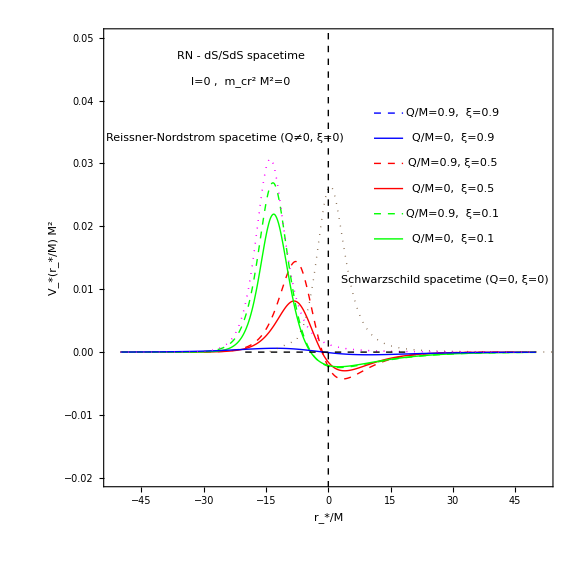

```mathematica
splvrtmcr=Show[plvrt05crq,plvrt09crq,plvrt01crq,plvrt05cr,plvrt01cr,plvrt09cr,plvrtschcr,plvrt09crq,Graphics[{Inset[" RN - dS/SdS spacetime ",{-21,0.047},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" l=0 ,  m_cr^2Μ^2=0",{-21,0.043},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["Reissner-Nordstrom spacetime (Q≠0, ξ=0)",{-25,0.034},BaseStyle->{Bold,Magenta,FontFamily->"Times",13}]}],Graphics[{Inset["Schwarzschild spacetime (Q=0, ξ=0)",{28,0.0115},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",13}]}],Graphics[{Inset[" Q/M=0.9,  ξ=0.9",{30,0.038},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  ξ=0.9",{30,0.034},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, ξ=0.5 ",{30,0.03},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset[" Q/M=0,  ξ=0.5",{30,0.026},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9,  ξ=0.1",{30,0.022},BaseStyle->{Bold,Green,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  ξ=0.1 ",{30,0.018},BaseStyle->{Bold,Green,FontFamily->"Times",13}]}],Epilog->{{Dashing[0.008],Black,Line[{{-20,0},{20,0}}]},{Dashing[0.008],Black,Line[{{0,-1},{0,1}}]},{Thick,Dashed,Blue,Line[{{11,0.038},{18,0.038}}]},{Thick,Blue,Line[{{11,0.034},{18,0.034}}]},{Dashed,Thick,Red,Line[{{11,0.03},{18,0.03}}]},{Thick,Red,Line[{{11,0.026},{18,0.026}}]},{Thick,Green,Line[{{11,0.018},{18,0.018}}]},{Dashed,Thick,Green,Line[{{11,0.022},{18,0.022}}]}},Frame->True,FrameLabel->{"r_*/M","V_*(r_*/M) M^2"},Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-52,52},{-0.02,0.05}},ImageSize->Large]
```

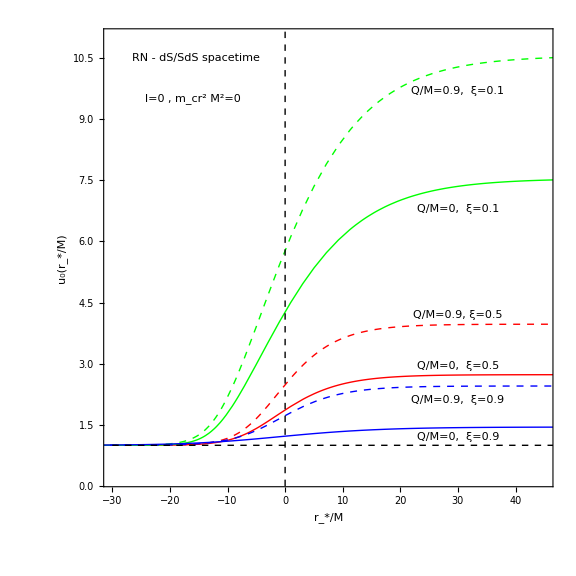

```mathematica
splumcr=Show[plu05crq,plu05cr,plu01cr,plu01crq,plu09cr,plu09crq,Graphics[{Inset[" RN - dS/SdS spacetime  ",{-15.5,10.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" l=0 , m_cr^2Μ^2=0 ",{-16,9.5},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" Q/M=0.9,  ξ=0.9",{30,2.1},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  ξ=0.9",{30,1.2},BaseStyle->{Bold,Blue,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9, ξ=0.5 ",{30,4.2},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset[" Q/M=0,  ξ=0.5",{30,2.95},BaseStyle->{Bold,Red,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0.9,  ξ=0.1",{30,9.7},BaseStyle->{Bold,Green,FontFamily->"Times",13}]}],Graphics[{Inset["Q/M=0,  ξ=0.1 ",{30,6.8},BaseStyle->{Bold,Green,FontFamily->"Times",13}]}],Epilog->{{Dashing[0.008],Black,Line[{{-30,1},{60,1}}]},{Dashing[0.008],Black,Line[{{0,0},{0,15}}]}},FrameLabel->{"r_*/M","u_0(r_*/M)"},Frame->True,Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-30,45},{0.2,11.}},ImageSize->Large]
```

```mathematica
(* Figure 3  *)
```

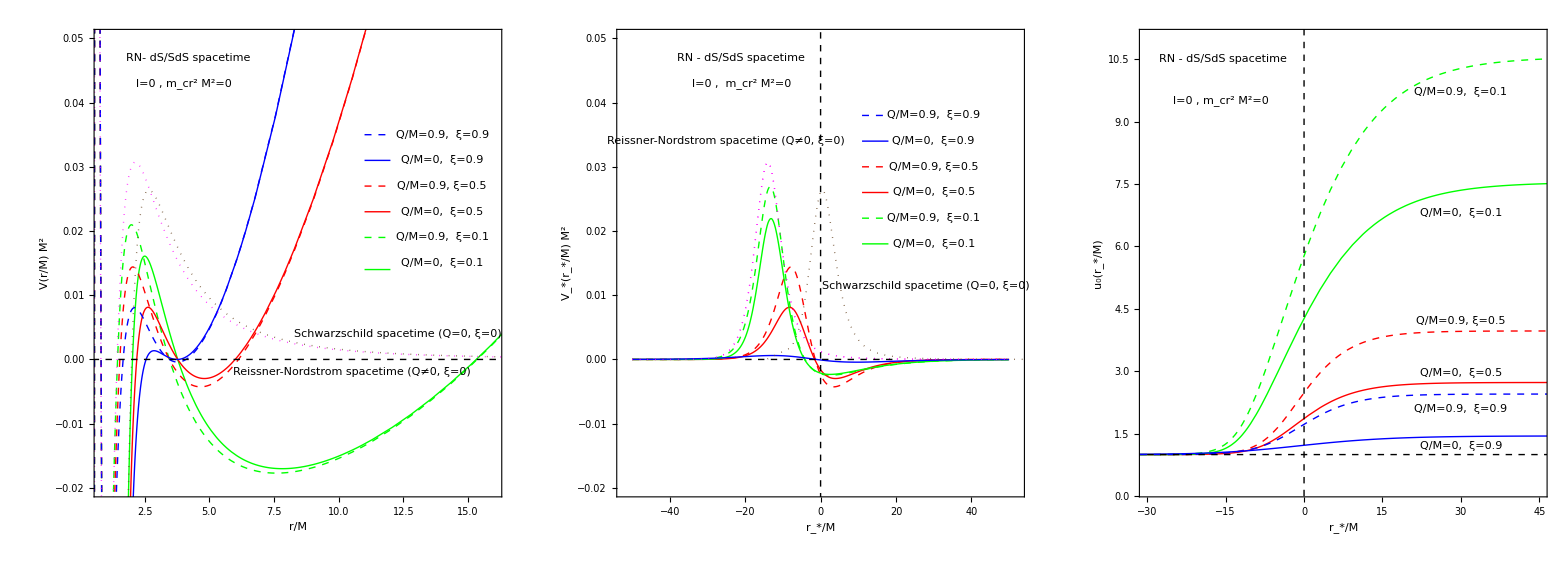

```mathematica
fig2=GraphicsGrid[{{splvrmcr,splvrtmcr,splumcr}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"fig2.pdf",fig2,ImageResolution->1000];
```

## Figure 4

```mathematica
(* Plot of the critical value of the scalar field mass Subscript[m, cr]^2 M^2 which is zero and independent of the dimensionless parameter ξ (with ξ ϵ[0,Subscript[ξ, Η,C](q)]) 
in the case of the SdS and RN-dS spacetime (blue straight line) for l=0. The solid curves show the form of Subscript[m, cr](ξ,q)^2 M^2 that saturates the 
Sufficient for Instability Criterion (SIC) Eq.(3.11) while the corresponding dashed curves shows the forms of Subscript[m, cr](ξ,q)^2 M^2 that saturate the
Suffiecient for Stability Criterion (SSC) Eq.(3.12) for three values of Q/M *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

Clear[s,xi,m,mm2]
```

```mathematica
(*  It is used to find  the critical value Subscript[m, cr]^2 Μ^2= 0 of the scalar field mass for  various values of dimensionless parameter ξ =9 Μ^2 Λ . In practice we used the 
shooting method in solving Eq. (2.22) with growth rate  Ω = 0  and fixed ξ  and boundary conditions (3.7) and (3.8) at large negative r_* and adjust m^2 Μ^2 until 
the boundary conditions (3.9) and (3.10) are satisfied. By repeating   this process for several values of ξ from 0 to 1 we have constructed the blue straight 
line which shows the independence of Subscript[m, cr]^2 Μ^2 on ξ *)
```

```mathematica
(* Metric function f *)
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
daar=D[aa[r],r]/r;
m=1;xi=0.9;mm2=-0.0001;qq2=0.3;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
ss=Sort[Table[s[[i,1,2]],{i,1,Length[s]}]];
```

```mathematica
horcos=ss[[Length[ss]]];
horev=ss[[Length[ss]-1]];
```

```mathematica
(* It is used to find the function r_*(r)  *)
```

```mathematica
hord=10^-10;
rt1[r1_?NumberQ]:=NIntegrate[1/aa[x],{x,(horev+horcos)/2,r1}]
```

```mathematica
(* It is used to find the function r(r_*)  *)
```

```mathematica
xmin=-50;
xmax=50;
rofrt[rt_]:=Piecewise[{{FindRoot[rt1[rr]==rt,{rr,horev+hord}][[1,2]],rt≤0},{FindRoot[rt1[rr]==rt,{rr,horcos-0.0001}][[1,2]],rt≥0}}]
rofrt[xmin];
rofrt[xmax];
```

```mathematica
tabvrt1=Table[{rtt,V[rofrt[rtt],m,xi,0,mm2]},{rtt,xmin,xmax,1}];
```

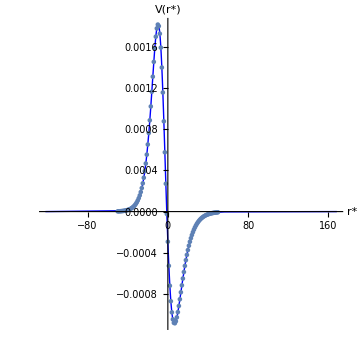

```mathematica
pl1=ListPlot[tabvrt1,PlotRange->All];
pl2=ParametricPlot[{{rt1[r],V[r,m,xi,0,mm2]}},{r,horev+hord,horcos-hord}, PlotRange->All,PlotStyle->{Blue,Thick},AxesLabel->{"r*","V(r*)"},BaseStyle->{FontFamily->"Times",18},AspectRatio->1,ImageSize->Medium];

Show[pl2,pl1]
```

```mathematica
ff= Interpolation[tabvrt1,InterpolationOrder->3,Method->"Hermite"]
```

InterpolatingFunction[{{-50., 50.}}, <>]

```mathematica
(* Schrodinger-like equation (2.22) with Ω=0 *)
```

```mathematica
eq1=D[u[x],{x,2}]-ff[x]u[x]==0;
(*  Boundary conditions  (3.7) and (3.8) *)

bc1=u[xmin]==1;
bc2=u'[xmin]==0;
```

```mathematica
(* It is used to find the radial zero mode solution Subscript[u, 0]  *)

sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
```

{{u→InterpolatingFunction[{{-50., 50.}}, <>]}}

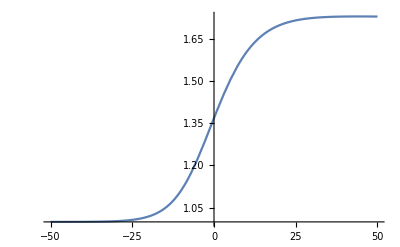

```mathematica
Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotRange->All]
```

```mathematica
u'[xmax] /. sol
```

{-0.000105564}

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
mcrξ=Table[{i,0},{i,0,1,0.01}];
```

```mathematica
plmcrξ=ListPlot[mcrξ,PlotRange->All,Joined->True,PlotStyle->{Red,Dashed},PlotRange->All];
```

```mathematica
intmcrξ= Interpolation[mcrξ,InterpolationOrder->2,Method->"Hermite"];
```

```mathematica
plintmcrξ=Plot[intmcrξ[ξ],{ξ,0.01,1.54},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
(*  It is used to construct  the  lower curves in Fig.4 which correspond to the values of m(ξ)^2 Μ^2  that saturate  τηε Sufficient for Instability Criterion (SIC) *)
```

```mathematica
(* Metric function f *)
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
daar=D[aa[r],r]/r;
m=1;qq2=0.9;

(*  Regge-Wheeler potential V  *)
V[r_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
V1[r_,m_,xi_,l_,qq2_,mm2_]:=Chop[(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2)];
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
```

```mathematica
horev[xi_]=0.5 √((18.+(26.316159643915796-10.526463857566318 xi)/((-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))+3.0779567040180544 (-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))/xi)-0.5 √(1/xi(36.+(-26.316159643915796+10.526463857566318 xi)/((-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))-3.0779567040180544 (-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3)-108./(√((18.+(26.316159643915796-10.526463857566318 xi)/((-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))+3.0779567040180544 (-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))/xi))));
horcos[xi_]=0.5 √((18.+(26.316159643915796-10.526463857566318 xi)/((-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))+3.0779567040180544 (-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))/xi)+0.5 √(1/xi(36.+(-26.316159643915796+10.526463857566318 xi)/((-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))-3.0779567040180544 (-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3)-108./(√((18.+(26.316159643915796-10.526463857566318 xi)/((-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))+3.0779567040180544 (-25.+20. xi-3.1622776601683795 √(xi (-25.+10. xi+4. xi^2)))^(1/3))/xi))));
```

```mathematica
plsicxi09=Plot[NSolve[Integrate[V1[r,m,xi,0,qq2,mm2],{r,horev[xi],horcos[xi]}]==0,mm2][[1,1,2]],{xi,0.0001,1.57},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
(* Metric function f *)
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
daar=D[aa[r],r]/r;
m=1;qq2=0.3;
V[r_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
```

```mathematica
V1[r_,m_,xi_,l_,qq2_,mm2_]:=Chop[(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2)];
```

```mathematica
(* Horizons  *)
```

```mathematica
s=Simplify[NSolve[aa[r]==0,r],Reals];
```

```mathematica
horev[xi_]=0.5 √((18.+(54.73981796016061-7.2986423946880805 xi)/((-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))+1.4797272445982819 (-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))/xi)-0.5 √(1/xi(36.+(-54.73981796016061+7.2986423946880805 xi)/((-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))-1.4797272445982819 (-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3)-108./(√((18.+(54.73981796016061-7.2986423946880805 xi)/((-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))+1.4797272445982819 (-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))/xi))));
horcos[xi_]=0.5 √((18.+(54.73981796016061-7.2986423946880805 xi)/((-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))+1.4797272445982819 (-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))/xi)+0.5 √(1/xi(36.+(-54.73981796016061+7.2986423946880805 xi)/((-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))-1.4797272445982819 (-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3)-108./(√((18.+(54.73981796016061-7.2986423946880805 xi)/((-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))+1.4797272445982819 (-225.+360. xi-5.477225575051661 √(xi (-4725.+4230. xi+4. xi^2)))^(1/3))/xi))));
```

```mathematica
plsicxi03=Plot[NSolve[Integrate[V1[r,m,xi,0,qq2,mm2],{r,horev[xi],horcos[xi]}]==0,mm2][[1,1,2]],{xi,0.0001,1.15},PlotStyle->{Darker[Green],Thick},PlotRange->All];
```

```mathematica
(* Metric function f *)
```

```mathematica
aa[r_]:=1-2*m/r+qq2/r^2-xi/27 *r^2;
daar=D[aa[r],r]/r;
m=1;qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,xi_,l_,mm2_]:=aa[r]*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
V1[r_,m_,xi_,l_,qq2_,mm2_]:=Chop[(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2)];
(* Horizons  *)s=Simplify[NSolve[aa[r]==0,r],Reals];
```

```mathematica
horev[xi_]=((1.4999999999999998+2.598076211353316 ⅈ) xi+(1.5-2.598076211353316 ⅈ) (xi^2+√((-1.+xi) xi^3))^(2/3))/(xi (xi^2+√((-1.+xi) xi^3))^(1/3));
horcos[xi_]=((1.4999999999999998-2.598076211353316 ⅈ) xi+(1.5+2.598076211353316 ⅈ) (xi^2+√((-1.+xi) xi^3))^(2/3))/(xi (xi^2+√((-1.+xi) xi^3))^(1/3));
```

```mathematica
plsicxi0=Plot[NSolve[Integrate[V1[r,m,xi,0,qq2,mm2],{r,horev[xi],horcos[xi]}]==0,mm2][[1,1,2]],{xi,0.0001,1.05},PlotStyle->{Darker[Magenta],Thick},PlotRange->All];
```

```mathematica
Clear[ss,s,mm2,sol]
```

```mathematica
(*  It is used to construct  the  upper curves in Fig.4 which correspond to the values of m(ξ)^2 Μ^2  that saturate  τηε Sufficient for Stability Criterion (SSC) *)
```

```mathematica
qq2=0;

(*  Regge-Wheeler potential V  *)
V[r_,m_,xi_,l_,mm2_,qq2_]:=(1-2*m/r+qq2/r^2-xi/27 *r^2)*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
dvr=D[V[r,1,xi,0,mm2,qq2],r];
```

```mathematica
ddvr=D[D[V[r,1,xi,0,mm2,qq2],r],r];
```

```mathematica
s=Solve[dvr==0&&V[r,1,xi,0,mm2,qq2]==0&&ddvr>0,{mm2,xi}]
```

{{mm2→ConditionalExpression[(-5832+2187 r+27 (-54+27 r)-2 (-54+27 r)^2)/(729 r^3-27 r^3 (-54+27 r)),r>3],xi→ConditionalExpression[(-54+27 r)/r^3,r>3]}}

```mathematica
FullSimplify[(-5832+2187 r+27 (-54+27 r)-2 (-54+27 r)^2)/(729 r^3-27 r^3 (-54+27 r))]
```

(2 (-3+r))/r^3

```mathematica
ss=Solve[xi==(-54+27 r)/r^3,r];
```

```mathematica
mm2xi[r_]=(2 (-3+r))/r^3;
```

```mathematica
(* The analytical form of the SSC curve for Q=0 as function of ξ *)

sol1[xi_]=PowerExpand[mm2xi[ss[[1,1,2]]]]
```

(2 (-3+3 (1/((-xi^2+√(-xi^3+xi^4))^(1/3))+((-xi^2+√(-xi^3+xi^4))^(1/3))/xi)))/(27 (1/((-xi^2+√(-xi^3+xi^4))^(1/3))+((-xi^2+√(-xi^3+xi^4))^(1/3))/xi)^3)

```mathematica
an1pl00=Plot[sol1[xi],{xi,0,1},AspectRatio->3/2,PlotStyle->{Darker[Magenta],Dashing[0.02],Thick},PlotRange->{{0,1.2},{-0.1,0.1}}];
```

```mathematica
Clear[s,ss,sol1]
```

```mathematica
qq2=0.3;
V[r_,m_,xi_,l_,mm2_,qq2_]:=(1-2*m/r+qq2/r^2-xi/27 *r^2)*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
dvr=D[V[r,1,xi,0,mm2,qq2],r];
```

```mathematica
ddvr=D[D[V[r,1,xi,0,mm2,qq2],r],r];
```

```mathematica
s=Solve[dvr==0&&V[r,1,xi,0,mm2,qq2]==0&&ddvr>0,{mm2,xi}];
```

```mathematica
sm1=(-1.0428747231239114*^18+8.690622692699264*^18 r-1.7767495282851828*^19 r^2+5.793748461799509*^18 r^3+7.152775878764826*^16 r^5 ((4.384649148589726*^-29 (-3.6947083907980524*^29+3.386816024898215*^30 r-7.389416781596106*^30 r^2+3.0789236589983773*^30 r^3))/(r^4 (-2.+5. r))-1.1321115420967026*^-29 √((-3.915173489891899*^44+2.936380117418924*^45 r-5.546495777346857*^45 r^2+1.631322287454958*^45 r^3)/(r^8 (-2.+5. r)^2)))-5.29835250278876*^15 r^8 ((4.384649148589726*^-29 (-3.6947083907980524*^29+3.386816024898215*^30 r-7.389416781596106*^30 r^2+3.0789236589983773*^30 r^3))/(r^4 (-2.+5. r))-1.1321115420967026*^-29 √((-3.915173489891899*^44+2.936380117418924*^45 r-5.546495777346857*^45 r^2+1.631322287454958*^45 r^3)/(r^8 (-2.+5. r)^2)))^2)/(-5.793748461799508*^17 r^4+1.931249487266503*^18 r^5-7.152775878764826*^16 r^8 ((4.384649148589726*^-29 (-3.6947083907980524*^29+3.386816024898215*^30 r-7.389416781596106*^30 r^2+3.0789236589983773*^30 r^3))/(r^4 (-2.+5. r))-1.1321115420967026*^-29 √((-3.915173489891899*^44+2.936380117418924*^45 r-5.546495777346857*^45 r^2+1.631322287454958*^45 r^3)/(r^8 (-2.+5. r)^2))));
sxi1=(4.384649148589726*^-29 (-3.6947083907980524*^29+3.386816024898215*^30 r-7.389416781596106*^30 r^2+3.0789236589983773*^30 r^3))/(r^4 (-2.+5. r))-1.1321115420967026*^-29 √((-3.915173489891899*^44+2.936380117418924*^45 r-5.546495777346857*^45 r^2+1.631322287454958*^45 r^3)/(r^8 (-2.+5. r)^2));
```

```mathematica
para1pl03=ParametricPlot[{sxi1,sm1},{r,2.785,50},AspectRatio->3/2,PlotStyle->{Darker[Green],Dashing[0.02],Thick},PlotRange->{{0,1.2},{-0.1,0.1}}];
```

```mathematica
Clear[s,ss,sol,sm1,sxi1]
```

```mathematica
qq2=0.9;
V[r_,m_,xi_,l_,mm2_,qq2_]:=(1-2*m/r+qq2/r^2-xi/27 *r^2)*(l*(l+1)/r^2+(-(2 qq2)/r^3+(2 m)/r^2-(2 r xi)/27)/r+mm2);
dvr=D[V[r,1,xi,0,mm2,qq2],r];
```

```mathematica
ddvr=D[D[V[r,1,xi,0,mm2,qq2],r],r];
```

```mathematica
s=Solve[dvr==0&&V[r,1,xi,0,mm2,qq2]==0&&ddvr>0,{mm2,xi}];
```

```mathematica
sm1=(-9.972489539872514*^18+2.7701359832979206*^19 r-2.380264993055992*^19 r^2+6.155857740662047*^18 r^3+7.599824371187712*^15 r (243.-540. r+270. r^2)-5.629499534213121*^13 (243.-540. r+270. r^2)^2)/(-1.846757322198614*^18 r^4+2.0519525802206822*^18 r^5-7.599824371187712*^15 r^4 (243.-540. r+270. r^2));
sxi1=(0.1 (243.-540. r+270. r^2))/r^4;
```

```mathematica
para1pl09=ParametricPlot[{sxi1,sm1},{r,2.1709,50},AspectRatio->3/2,PlotStyle->{Red,Dashing[0.02],Thick},PlotRange->{{0,1.8},{-0.1,0.1}}];
```

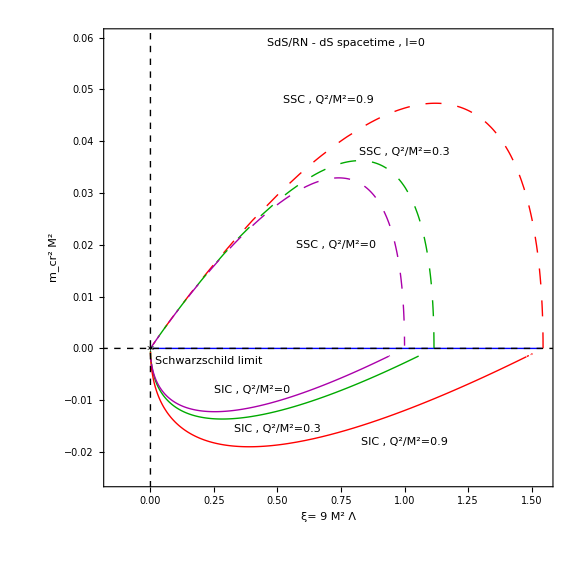

```mathematica
fig4new=Show[plintmcrξ,plsicxi03,plsicxi09,plsicxi0,para1pl09,para1pl03,an1pl00,Graphics[{Inset[" SdS/RN - dS spacetime , l=0 ",{0.77,0.059},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" Schwarzschild limit",{0.23,-0.0025},BaseStyle->{Italic,Bold,Brown,FontFamily->"Times",14}]}],Graphics[{Inset[" SIC , Q^2/M^2=0",{0.4,-0.008},BaseStyle->{Italic,Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset[" SIC , Q^2/M^2=0.3",{0.5,-0.0155},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset[" SIC , Q^2/M^2=0.9",{1,-0.018},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],Graphics[{Inset[" SSC , Q^2/M^2=0",{0.73,0.02},BaseStyle->{Italic,Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset[" SSC , Q^2/M^2=0.3",{1,0.038},BaseStyle->{Italic,Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset[" SSC , Q^2/M^2=0.9",{0.7,0.048},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],Graphics[{Inset["✶",{0,0},BaseStyle->{Bold,Brown,FontFamily->"Times",26}]}],PlotRange->{{-0.15,1.55},{-0.025,0.06}},Frame->True,FrameLabel->{"ξ= 9 M^2 Λ"," m_cr^2 M^2"},Axes->None,AspectRatio->1,Epilog->{{Dashing[0.008],Black,Line[{{-1,0},{3,0}}]},{Dashing[0.008],Black,Line[{{0,-1},{0,1}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"fig4new.pdf",fig4new,ImageResolution->1000];
```

## Figure 5

```mathematica
(* 3D plot of the dimensionless growth rate of the instability  Ω M as a function of the dimensionless parameters ξ and q^2=Q^2/M^2 for scalar field 
mass m^2 M^2 =-0.05 (cyan surface) and m^2 M^2 =-0.2  (yellow surface) *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
(* m^2 =-0.2  *)
```

```mathematica
(* Table obtained from mathsfile: tables_fig5.nb   *)
```

```mathematica
omtabq02={{0.,0.1,0.28814261496385324},{0.1,0.1,0.2888479216053611},{0.2,0.1,0.2895636064898522},{0.30000000000000004,0.1,0.29029053989276726},{0.4,0.1,0.2910298796859707},{0.5,0.1,0.2917829982036695},{0.6000000000000001,0.1,0.29255152815963215},{0.7000000000000001,0.1,0.29333764767209974},{0.8,0.1,0.294144578416936},{0.9,0.1,0.2949767766128051},{0.,0.2,0.24099755211046556},{0.1,0.2,0.24218403475258288},{0.2,0.2,0.24338888236764616},{0.30000000000000004,0.2,0.2446141745591173},{0.4,0.2,0.24586253650259493},{0.5,0.2,0.2471370622552521},{0.6000000000000001,0.2,0.24844173851302354},{0.7000000000000001,0.2,0.24978229267052043},{0.8,0.2,0.2511660101597875},{0.9,0.2,0.2526058234039898},{0.,0.30000000000000004,0.20709480955110618},{0.1,0.30000000000000004,0.20874951657256002},{0.2,0.30000000000000004,0.21042787588043213},{0.30000000000000004,0.30000000000000004,0.21213364559950693},{0.4,0.30000000000000004,0.21387071742631572},{0.5,0.30000000000000004,0.21564402405863095},{0.6000000000000001,0.30000000000000004,0.21746042834462403},{0.7000000000000001,0.30000000000000004,0.2193289332675309},{0.8,0.30000000000000004,0.22126292003569895},{0.9,0.30000000000000004,0.22328433616720048},{0.,0.4,0.17923917217098387},{0.1,0.4,0.18139189105307063},{0.2,0.4,0.18357033378271928},{0.30000000000000004,0.4,0.18577905697475033},{0.4,0.4,0.1880236640706169},{0.5,0.4,0.19031153189064517},{0.6000000000000001,0.4,0.1926521215815415},{0.7000000000000001,0.4,0.19505837554555436},{0.8,0.4,0.19755008152697817},{0.9,0.4,0.20016027265134229},{0.,0.5,0.15463656304806328},{0.1,0.5,0.15735533921981185},{0.2,0.5,0.16009452246668365},{0.30000000000000004,0.5,0.1628606961714087},{0.4,0.5,0.16566185495746544},{0.5,0.5,0.16850732400362028},{0.6000000000000001,0.5,0.17141013131053928},{0.7000000000000001,0.5,0.17438797031633843},{0.8,0.5,0.17746695836857768},{0.9,0.5,0.18069211196660995},{0.,0.6,0.13171174026248117},{0.1,0.6,0.13511786313445},{0.2,0.6,0.13852582862995058},{0.30000000000000004,0.6,0.14194519770985778},{0.4,0.6,0.14538706863535975},{0.5,0.6,0.1488648383641056},{0.6000000000000001,0.6,0.15239535119399783},{0.7000000000000001,0.6,0.15600223231943963},{0.8,0.6,0.1597189116647435},{0.9,0.6,0.16360402934141138},{0.,0.7000000000000001,0.10923855982858591},{0.1,0.7000000000000001,0.11355377139537946},{0.2,0.7000000000000001,0.11782016044965384},{0.30000000000000004,0.7000000000000001,0.12205548930393946},{0.4,0.7000000000000001,0.12627818851503517},{0.5,0.7000000000000001,0.13050867259089466},{0.6000000000000001,0.7000000000000001,0.1347707257800245},{0.7000000000000001,0.7000000000000001,0.13909528390784298},{0.8,0.7000000000000001,0.1435266369979079},{0.9,0.7000000000000001,0.14813783425035754},{0.,0.8,0.08578803735586843},{0.1,0.8,0.09147484197979668},{0.2,0.8,0.09696996480662268},{0.30000000000000004,0.8,0.10232076642464669},{0.4,0.8,0.1075686931537744},{0.5,0.8,0.11275236252671193},{0.6000000000000001,0.8,0.11791160459968765},{0.7000000000000001,0.8,0.12309128020666295},{0.8,0.8,0.12835105315329726},{0.9,0.8,0.13378364408657906},{0.,0.9,0.0584972221186362},{0.1,0.9,0.06688337846727832},{0.2,0.9,0.07452076859546053},{0.30000000000000004,0.9,0.08164323199078823},{0.4,0.9,0.08840207007180394},{0.5,0.9,0.09490684517812875},{0.6000000000000001,0.9,0.10124619726110351},{0.7000000000000001,0.9,0.10750225405717571},{0.8,0.9,0.11376475187883642},{0.9,0.9,0.12015760651306259}};
```

```mathematica
fig3daom02=ListSurfacePlot3D[omtabq02,TicksStyle->Black,AxesLabel->{"Q^2/M^2","ξ","ΩM"},Mesh->{4,4,4},MeshStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Darker[Green],Thick]}, BoundaryStyle->{Directive[Darker[Yellow],Thick],Opacity[0.85]},PlotRange->{{0,1},{0,0.9},{0,0.5}},PlotStyle->{FaceForm[LightYellow,Yellow],Opacity[0.85]},AxesStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},MaxPlotPoints->50,ImageSize->Large];
```

```mathematica
fig3dom02=-Graphics3D-;
```

```mathematica
(* m^2 =-0.05  *)
```

```mathematica
(* Table obtained from mathsfile: tables_fig5.nb   *)
```

```mathematica
omtabq005={{0.,0.1,0.12454528514361532},{0.1,0.1,0.12484002405555347},{0.2,0.1,0.12513998709386742},{0.30000000000000004,0.1,0.12544581366571356},{0.4,0.1,0.12575833570824083},{0.5,0.1,0.1260785502523261},{0.6000000000000001,0.1,0.1264082257369996},{0.7000000000000001,0.1,0.12674941485451913},{0.8,0.1,0.12710585641305688},{0.9,0.1,0.12748460339800807},{0.,0.2,0.09898312569243772},{0.1,0.2,0.09946263168004205},{0.2,0.2,0.09993020725098604},{0.30000000000000004,0.2,0.10041729081249157},{0.4,0.2,0.10092488113088413},{0.5,0.2,0.1014265591278623},{0.6000000000000001,0.2,0.10195385936903417},{0.7000000000000001,0.2,0.10250162133819583},{0.8,0.2,0.10307725651296326},{0.9,0.2,0.10369531247553776},{0.,0.30000000000000004,0.08223100444444781},{0.1,0.30000000000000004,0.08286658460067838},{0.2,0.30000000000000004,0.08351218421133398},{0.30000000000000004,0.30000000000000004,0.08416948685142325},{0.4,0.30000000000000004,0.08484051669410694},{0.5,0.30000000000000004,0.08555614692922335},{0.6000000000000001,0.30000000000000004,0.08623775548807291},{0.7000000000000001,0.30000000000000004,0.08697466560789409},{0.8,0.30000000000000004,0.087748571459789},{0.9,0.30000000000000004,0.08858610629146076},{0.,0.4,0.06939205460572187},{0.1,0.4,0.0702052053168617},{0.2,0.4,0.07102837015676754},{0.30000000000000004,0.4,0.07192853704992846},{0.4,0.4,0.0727},{0.5,0.4,0.0735838590225468},{0.6000000000000001,0.4,0.07447819087221935},{0.7000000000000001,0.4,0.07540549142407144},{0.8,0.4,0.0763801500617153},{0.9,0.4,0.07743118978395207},{0.,0.5,0.05852369220645706},{0.1,0.5,0.05966003643921723},{0.2,0.5,0.06068514602164129},{0.30000000000000004,0.5,0.06172047484937844},{0.4,0.5,0.0627696834083276},{0.5,0.5,0.06383786124971498},{0.6000000000000001,0.5,0.06486211594455014},{0.7000000000000001,0.5,0.06601982682033085},{0.8,0.5,0.06724175870633552},{0.9,0.5,0.06847979909631474},{0.,0.6,0.049026587222078526},{0.1,0.6,0.05029756962592003},{0.2,0.6,0.05156778156286067},{0.30000000000000004,0.6,0.05284107044838988},{0.4,0.6,0.05412289437190984},{0.5,0.6,0.05541899131533924},{0.6000000000000001,0.6,0.05673860008415761},{0.7000000000000001,0.6,0.05809413481755838},{0.8,0.6,0.059506844183087985},{0.9,0.6,0.06098428932170446},{0.,0.7000000000000001,0.039893034737064036},{0.1,0.7000000000000001,0.041502474248585004},{0.2,0.7000000000000001,0.04309098626120892},{0.30000000000000004,0.7000000000000001,0.04466582242879879},{0.4,0.7000000000000001,0.04623460533768001},{0.5,0.7000000000000001,0.047806077021502684},{0.6000000000000001,0.7000000000000001,0.0493921520032016},{0.7000000000000001,0.7000000000000001,0.05100796227709538},{0.8,0.7000000000000001,0.05267878296032641},{0.9,0.7000000000000001,0.05445477911438896},{0.,0.8,0.03061874839876547},{0.1,0.8,0.03273271128528879},{0.2,0.8,0.03477455112078508},{0.30000000000000004,0.8,0.03676137837588834},{0.4,0.8,0.03870853540228198},{0.5,0.8,0.040631246090415726},{0.6000000000000001,0.8,0.04254638422446748},{0.7000000000000001,0.8,0.04447496257714615},{0.8,0.8,0.04644807708959523},{0.9,0.8,0.04852320437063689},{0.,0.9,0.020215891859937937},{0.1,0.9,0.023262042426004804},{0.2,0.9,0.026059189214559658},{0.30000000000000004,0.9,0.028680164428914665},{0.4,0.9,0.031173916640516518},{0.5,0.9,0.033577602812299684},{0.6000000000000001,0.9,0.03592388277413065},{0.7000000000000001,0.9,0.03824583298272081},{0.8,0.9,0.040585235121184164},{0.9,0.9,0.04301110627679682}};
```

```mathematica
fig3daom005=ListSurfacePlot3D[omtabq005,TicksStyle->Black,AxesLabel->{"Q^2/M^2","ξ","ΩM"},Mesh->{4,4,4},MeshStyle->{Directive[Red,Thick],Directive[Blue,Thick],Directive[Darker[Green],Thick]}, BoundaryStyle->{Directive[Darker[Cyan],Thick],Opacity[0.35]},PlotRange->{{0,1},{0,0.9},{0,0.5}},PlotStyle->{FaceForm[Cyan,LightCyan],Opacity[0.35]},AxesStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},MaxPlotPoints->50,ImageSize->Large];
```

```mathematica
fig3dim=Show[fig3daom02,fig3daom005,PlotLabel->Style[Framed["RN - dS spacetime, l=0, m^2M^2=-0.05,m^2M^2=-0.2"],18,Black,Background->LightBlue]]
```

-Graphics3D-

```mathematica
fig3dim=-Graphics3D-;
```

```mathematica
Export[NotebookDirectory[]<>"fig3dim.pdf",fig3dim,ImageResolution->1000];
```

## Figure 6

```mathematica
(* Plot of the ξ dependent relative growth rate of the instability Ω/Subscript[Ω, F] (with Subscript[Ω, F] the growth rate of the instability in flat spacetime) as a 
function of the dimensionless parameter q^2=Q^2/M^2  for the scalar field mass m^2 M^2=-0.05  and m^2 M^2 =-0.2. The curves for a given parameter value ξ
(with ξ<1) turn out to be straight lines. The range of values of ξ and q is determined by the physically interesting parameter region between the green and blue lines of Fig.1.The
parameter region corresponding to linear behavior of Ω(q^2) (yellow region) is also shown in Fig.1 *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

(* m^2 M^2=-0.05  *)
```

```mathematica
(* Table obtained from mathsfile: tables_fig6.nb   *)
```

```mathematica
omtabrelq={{0.,0.1,0.556983447716437},{0.025,0.1,0.5573109566856302},{0.05,0.1,0.5524577642605759},{0.07500000000000001,0.1,0.5579701124044026},{0.1,0.1,0.5583015602018531},{0.125,0.1,0.5586347200255581},{0.15000000000000002,0.1,0.5589693540672431},{0.17500000000000002,0.1,0.5593056953000545},{0.2,0.1,0.5596430356906679},{0.225,0.1,0.5599825158916933},{0.25,0.1,0.5603233949345193},{0.275,0.1,0.5606661697674936},{0.30000000000000004,0.1,0.5610107336986152},{0.325,0.1,0.5613571023754197},{0.35000000000000003,0.1,0.5617054461402077},{0.375,0.1,0.5620559436459017},{0.4,0.1,0.5624083747617313},{0.42500000000000004,0.1,0.5627627596353793},{0.45,0.1,0.5631197185583026},{0.47500000000000003,0.1,0.563478953706226},{0.5,0.1,0.5638404177376488},{0.525,0.1,0.564204864778329},{0.55,0.1,0.5645713738572221},{0.5750000000000001,0.1,0.5649416382486927},{0.6000000000000001,0.1,0.5653147713261392},{0.625,0.1,0.5656907268927194},{0.65,0.1,0.5660704638777871},{0.675,0.1,0.5664536413462714},{0.7000000000000001,0.1,0.5668406154460528},{0.7250000000000001,0.1,0.567231897239018},{0.75,0.1,0.08913126020716279},{0.775,0.1,0.5680284169956066},{0.8,0.1,0.5684346705558456},{0.8250000000000001,0.1,0.5688457154880026},{0.8500000000000001,0.1,0.5692659268739763},{0.875,0.1,0.5696926577899933},{0.9,0.1,0.5701284785650935},{0.925,0.1,0.5705748038238961},{0.9500000000000001,0.1,0.5710345818868199},{0.9750000000000001,0.1,0.5715116472211593},{1.,0.1,0.5720150060044594},{1.0250000000000001,0.1,0.5725188137737868-0.0000635875205158992 ⅈ},{1.05,0.1,0.5728511932903333-0.00009767962194035439 ⅈ},{1.075,0.1,0.10100513897739655-0.0003904916890628426 ⅈ},{1.1,0.1,0.5190893097459306+0.016972408336102304 ⅈ},{1.125,0.1,0.5736416009553151-0.00042558268803607937 ⅈ},{0.,0.2,0.4426659953473934},{0.025,0.2,0.44318783231236414},{0.05,0.2,0.4437113239656929},{0.07500000000000001,0.2,0.4442340904271701},{0.1,0.2,0.4359146401570418},{0.125,0.2,0.4452958201092791},{0.15000000000000002,0.2,0.4458285797034279},{0.17500000000000002,0.2,0.44636372542216013},{0.2,0.2,0.4469014728376944},{0.225,0.2,0.44744159314677673},{0.25,0.2,0.4479847550436844},{0.275,0.2,0.4485307055673304},{0.30000000000000004,0.2,0.4490797767461925},{0.325,0.2,0.4496251922395935},{0.35000000000000003,0.2,0.45018676819830566},{0.375,0.2,0.45074552535993934},{0.4,0.2,0.41698560855250855},{0.42500000000000004,0.2,0.45187284126389227},{0.45,0.2,0.45244222710052134},{0.47500000000000003,0.2,0.4530157077544329},{0.5,0.2,0.4535933618676038},{0.525,0.2,0.06187861773508384},{0.55,0.2,0.4547623253996763},{0.5750000000000001,0.2,0.4553541932327814},{0.6000000000000001,0.2,0.45595152023522845},{0.625,0.2,0.4565543725986185},{0.65,0.2,0.457163194195971},{0.675,0.2,0.45777874846836325},{0.7000000000000001,0.2,0.4584011862322977},{0.7250000000000001,0.2,0.4590312985741084},{0.75,0.2,0.4596695409854831},{0.775,0.2,0.4603174086172489},{0.8,0.2,0.4609755049943376},{0.8250000000000001,0.2,0.461644546444309},{0.8500000000000001,0.2,0.4623270303336838},{0.875,0.2,0.4630244131458168},{0.9,0.2,0.46373953528676887},{0.925,0.2,0.46447631437508924},{0.9500000000000001,0.2,0.46524020631992563},{0.9750000000000001,0.2,0.4660414332981518},{1.,0.2,0.4669009415456021},{1.0250000000000001,0.2,0.46774923011751574-0.00003456002134507067 ⅈ},{1.05,0.2,2.892073219022382+0.06085655486269787 ⅈ},{1.075,0.2,0.44045046669800914+0.04564483496810081 ⅈ},{1.1,0.2,0.41459567840890454+0.03603617860887816 ⅈ},{1.125,0.2,0.0027858759114260676-0.2555179591368197 ⅈ},{0.,0.30000000000000004,0.3677482315917453},{0.025,0.30000000000000004,0.368455119800109},{0.05,0.30000000000000004,0.369164331420801},{0.07500000000000001,0.30000000000000004,0.4752236563037879},{0.1,0.30000000000000004,0.3705906324607082},{0.125,0.30000000000000004,0.3713080652458054},{0.15000000000000002,0.30000000000000004,0.3720282951096378},{0.17500000000000002,0.30000000000000004,0.3727513158788383},{0.2,0.30000000000000004,0.3734778416920549},{0.225,0.30000000000000004,0.3742073010869265},{0.25,0.30000000000000004,0.37494034817527827},{0.275,0.30000000000000004,0.37567707629222563},{0.30000000000000004,0.30000000000000004,0.3764173884621143},{0.325,0.30000000000000004,0.377161336861415},{0.35000000000000003,0.30000000000000004,0.37790903728276065},{0.375,0.30000000000000004,0.3786614603085752},{0.4,0.30000000000000004,0.37941832514845775},{0.42500000000000004,0.30000000000000004,51.293154724115695},{0.45,0.30000000000000004,0.3791181039110267},{0.47500000000000003,0.30000000000000004,0.3086944329430318},{0.5,0.30000000000000004,0.08427705089479917},{0.525,0.30000000000000004,0.38327802353376167},{0.55,0.30000000000000004,0.3840677889406641},{0.5750000000000001,0.30000000000000004,0.38486393911977435},{0.6000000000000001,0.30000000000000004,0.3856669669966732},{0.625,0.30000000000000004,0.3864779390022033},{0.65,0.30000000000000004,0.07814353466646547},{0.675,0.30000000000000004,0.38809424486479105},{0.7000000000000001,0.30000000000000004,0.3889625292391285},{0.7250000000000001,0.30000000000000004,0.3898108479201607},{0.75,0.30000000000000004,0.390671001689705},{0.775,0.30000000000000004,0.38894816007735367},{0.8,0.30000000000000004,0.39242354142517233},{0.8250000000000001,0.30000000000000004,-0.10108571715655346},{0.8500000000000001,0.30000000000000004,0.3942557854891126},{0.875,0.30000000000000004,14.469772440899405},{0.9,0.30000000000000004,0.3961691110594561},{0.925,0.30000000000000004,0.397170320781024},{0.9500000000000001,0.30000000000000004,0.3982119590350867},{0.9750000000000001,0.30000000000000004,0.3993095687990179},{1.,0.30000000000000004,0.40048916301047366},{1.0250000000000001,0.30000000000000004,0.006939000160114376-0.4461537010635514 ⅈ},{1.05,0.30000000000000004,0.40280085595274495-0.0006104800056694092 ⅈ},{1.075,0.30000000000000004,0.39617405194231115+0.006985221521575179 ⅈ},{1.1,0.30000000000000004,0.36301734875417935+0.012952095884432371 ⅈ},{1.125,0.30000000000000004,0.40329466880206494-0.0010323662304625246 ⅈ},{0.,0.4,0.31033070239354293},{0.025,0.4,0.2686315382701483},{0.05,0.4,0.3121442042199316},{0.07500000000000001,0.4,0.3130544554855472},{0.1,0.4,0.31396722292566487},{0.125,0.4,0.31487306901711337},{0.15000000000000002,0.4,0.31580173328162714},{0.17500000000000002,0.4,0.3167234266338033},{0.2,0.4,0.31764852800309923},{0.225,0.4,0.3185768860838912},{0.25,0.4,0.31950880421582767},{0.275,0.4,0.32044233434233327},{0.30000000000000004,0.4,0.3138566580987444},{0.325,0.4,0.3223213287912196},{0.35000000000000003,0.4,0.32305874430818765},{0.375,0.4,0.3242247060020852},{0.4,0.4,0.3235229273321899},{0.42500000000000004,0.4,0.32615170195228027},{0.45,0.4,0.32712148244808203},{0.47500000000000003,0.4,0.32809169223629003},{0.5,0.4,0.32907702164235175},{0.525,0.4,0.330065414413148},{0.55,0.4,0.33106079604478084},{0.5750000000000001,0.4,0.33206432968804445},{0.6000000000000001,0.4,0.3330765952629737},{0.625,0.4,0.334097276826609},{0.65,0.4,0.3351246245809707},{0.675,0.4,0.33617003239042154},{0.7000000000000001,0.4,0.3372236094020023},{0.7250000000000001,0.4,0.33821723671000137},{0.75,0.4,0.3393383696439761},{0.775,0.4,0.3404666117676259},{0.8,0.4,0.3415824153392603},{0.8250000000000001,0.4,0.3427178255310924},{0.8500000000000001,0.4,0.3438771101182497},{0.875,0.4,0.3390453406139164},{0.9,0.4,0.3462828078712082},{0.925,0.4,0.3475426746739115},{0.9500000000000001,0.4,14.332815826985417},{0.9750000000000001,0.4,0.3502426383268071},{1.,0.4,0.3517426775730618},{1.0250000000000001,0.4,2.792416420905878-0.010828700869853674 ⅈ},{1.05,0.4,0.3535169497355622-0.0007870565080684728 ⅈ},{1.075,0.4,0.005496323482844767-0.31854890381441475 ⅈ},{1.1,0.4,0.2729043865009707-0.029126678910588722 ⅈ},{1.125,0.4,0.0007166358463997827+0.3129016273558572 ⅈ},{0.,0.5,0.2385511484452319},{0.025,0.5,0.26339128709843806},{0.05,0.5,0.26451750839646404},{0.07500000000000001,0.5,0.19977057531509204},{0.1,0.5,0.2668077940364085},{0.125,0.5,0.26795039255522934},{0.15000000000000002,0.5,0.2690954818949271},{0.17500000000000002,0.5,0.2702426078934188},{0.2,0.5,0.2713922234577817},{0.225,0.5,0.27254513935494923},{0.25,0.5,0.2737008148329539},{0.275,0.5,0.274859462230836},{0.30000000000000004,0.5,0.2760223547335526},{0.325,0.5,0.2771885994548178},{0.35000000000000003,0.5,0.27835938042908165},{0.375,0.5,0.2795344850117873},{0.4,0.5,0.28071455805432244},{0.42500000000000004,0.5,0.2622343268231465},{0.45,0.5,0.2830906208366669},{0.47500000000000003,0.5,0.28428733040921644},{0.5,0.5,0.28549159458512474},{0.525,0.5,0.2867018817963223},{0.55,0.5,0.2878711266457253},{0.5750000000000001,0.5,0.28914765910682594},{0.6000000000000001,0.5,0.13753635607238873},{0.625,0.5,0.2916293785615438},{0.65,0.5,0.29288652447806374},{0.675,0.5,0.29415528965557397},{0.7000000000000001,0.5,0.2551790712716193},{0.7250000000000001,0.5,0.2967343436768359},{0.75,0.5,0.2926960498414879},{0.775,0.5,0.29937981843003675},{0.8,0.5,0.3007142867880091},{0.8250000000000001,0.5,0.3021097418039546},{0.8500000000000001,0.5,0.3035128651025327},{0.875,0.5,0.30495318175041086},{0.9,0.5,0.3064287156560319},{0.925,0.5,0.1271455501410368},{0.9500000000000001,0.5,0.3095122993233404},{0.9750000000000001,0.5,0.31122203427130346},{1.,0.5,0.2889490969531516},{1.0250000000000001,0.5,0.3151987962432218+0.000014142884347036242 ⅈ},{1.05,0.5,0.3109396592572738+0.0005040598814075953 ⅈ},{1.075,0.5,-0.0033949647570704474+0.5748234688680393 ⅈ},{1.1,0.5,0.3152970862238441-0.00011838959756653508 ⅈ},{1.125,0.5,0.316581948182867-0.003993974348215105 ⅈ},{0.,0.6,0.21925356346678032},{0.025,0.6,0.2206760084248456},{0.05,0.6,0.22209730158244428},{0.07500000000000001,0.6,0.2235180202334619},{0.1,0.6,0.22493756957317174},{0.125,0.6,0.22635769105858858},{0.15000000000000002,0.6,0.22777737448786725},{0.17500000000000002,0.6,0.22919742295512963},{0.2,0.6,0.2306181300468336},{0.225,0.6,0.23203899141509376},{0.25,0.6,0.23346241607012913},{0.275,0.6,0.23488666026407803},{0.30000000000000004,0.6,0.23631245105291013},{0.325,0.6,0.23774102227210894},{0.35000000000000003,0.6,0.2391724598512081},{0.375,0.6,0.24060681167268974},{0.4,0.6,0.2420449419092624},{0.42500000000000004,0.6,0.2434863131548101},{0.45,0.6,0.24493283076076028},{0.47500000000000003,0.6,0.24638434168001888},{0.5,0.6,0.24784126365113807},{0.525,0.6,0.2492926446338491},{0.55,0.6,0.2507763218366932},{0.5750000000000001,0.6,0.25225518996219026},{0.6000000000000001,0.6,0.25374273347270343},{0.625,0.6,0.25524020301542594},{0.65,0.6,0.25674872167878254},{0.675,0.6,0.258276430566223},{0.7000000000000001,0.6,0.2598048690921958},{0.7250000000000001,0.6,0.26135548162065786},{0.75,0.6,0.2629235528011522},{0.775,0.6,0.26451168691580834},{0.8,0.6,0.26612269743974537},{0.8250000000000001,0.6,0.2677602327605148},{0.8500000000000001,0.6,0.26942931402249093},{0.875,0.6,0.04182184176131442},{0.9,0.6,0.2727300329656914},{0.925,0.6,0.27469226866505625},{0.9500000000000001,0.6,0.27657208035360636},{0.9750000000000001,0.6,0.2768267725534224},{1.,0.6,0.2784620164739221},{1.0250000000000001,0.6,0.2831387584148042+7.801195251395745*^-6 ⅈ},{1.05,0.6,0.28331109263618-0.0016740245374971857 ⅈ},{1.075,0.6,-0.07518349527883789+0.8178599592024623 ⅈ},{1.1,0.6,0.24222300005914024-0.006130604183475435 ⅈ},{1.125,0.6,0.27953045921377634-0.013281178099447663 ⅈ},{0.,0.7000000000000001,0.17840707500167127},{0.025,0.7000000000000001,0.18021688794015353},{0.05,0.7000000000000001,0.18201943057795833},{0.07500000000000001,0.7000000000000001,0.18381516488422484},{0.1,0.7000000000000001,0.18560470730854114},{0.125,0.7000000000000001,0.18738812003106908},{0.15000000000000002,0.7000000000000001,0.18916648113511128},{0.17500000000000002,0.7000000000000001,0.19093978517867},{0.2,0.7000000000000001,0.1927087489951453},{0.225,0.7000000000000001,0.19447435491309248},{0.25,0.7000000000000001,0.19623598033433923},{0.275,0.7000000000000001,0.19799494840643828},{0.30000000000000004,0.7000000000000001,0.19975163044345773},{0.325,0.7000000000000001,0.2015066356470877},{0.35000000000000003,0.7000000000000001,0.2032606494042689},{0.375,0.7000000000000001,0.2050139843437713},{0.4,0.7000000000000001,0.20676744089585425},{0.42500000000000004,0.7000000000000001,0.20852160861956262},{0.45,0.7000000000000001,0.2102774520062813},{0.47500000000000003,0.7000000000000001,0.21203528978761724},{0.5,0.7000000000000001,0.21379527591534137},{0.525,0.7000000000000001,0.2154674327699784},{0.55,0.7000000000000001,0.21733048011879372},{0.5750000000000001,0.7000000000000001,0.2191059463978154},{0.6000000000000001,0.7000000000000001,0.2208884188683224},{0.625,0.7000000000000001,0.2226790044827132},{0.65,0.7000000000000001,0.2244791130351231},{0.675,0.7000000000000001,0.22629055307869014},{0.7000000000000001,0.7000000000000001,0.22811454209066048},{0.7250000000000001,0.7000000000000001,0.22995371357768912},{0.75,0.7000000000000001,0.2318105121224222},{0.775,0.7000000000000001,0.23368766701037172},{0.8,0.7000000000000001,0.23558667934249491},{0.8250000000000001,0.7000000000000001,0.23751634811534283},{0.8500000000000001,0.7000000000000001,0.23947750436297588},{0.875,0.7000000000000001,0.2414575936802747},{0.9,0.7000000000000001,0.24352917559901902},{0.925,0.7000000000000001,0.24564113962296796},{0.9500000000000001,0.7000000000000001,0.24783309726131283},{0.9750000000000001,0.7000000000000001,0.2501366568281792},{1.,0.7000000000000001,0.25261055747763894},{1.0250000000000001,0.7000000000000001,0.25541606802470274},{1.05,0.7000000000000001,0.0007889083130283663-0.33981191792130977 ⅈ},{1.075,0.7000000000000001,0.25589548535596424-0.0034509887719233424 ⅈ},{1.1,0.7000000000000001,0.005654315316871509-0.33715469628920425 ⅈ},{1.125,0.7000000000000001,0.25374891371823755-0.0031408670363814828 ⅈ},{0.,0.8,0.13693120561120486},{0.025,0.8,0.13932956748379186},{0.05,0.8,0.14170362710081238},{0.07500000000000001,0.8,0.14405520980308867},{0.1,0.8,0.1463851350435605},{0.125,0.8,0.1486951199931419},{0.15000000000000002,0.8,0.15098631261939843},{0.17500000000000002,0.8,0.15325973130396583},{0.2,0.8,0.15551652038623387},{0.225,0.8,0.15775837007151927},{0.25,0.8,0.1599861359257133},{0.275,0.8,0.16219996667490524},{0.30000000000000004,0.8,0.1644018819901543},{0.325,0.8,0.16659293113645796},{0.35000000000000003,0.8,0.16877388055771983},{0.375,0.8,0.1709458383746225},{0.4,0.8,0.17310983293791937},{0.42500000000000004,0.8,0.17526507065794011},{0.45,0.8,0.17741837149626555},{0.47500000000000003,0.8,0.17956506502079622},{0.5,0.8,0.18170845653738427},{0.525,0.8,0.18384958336195376},{0.55,0.8,0.18598929307166176},{0.5750000000000001,0.8,0.18787805453712378},{0.6000000000000001,0.8,0.19027321464546793},{0.625,0.8,0.19241943107935816},{0.65,0.8,0.19457112135046312},{0.675,0.8,0.19672969324494335},{0.7000000000000001,0.8,0.19889807923851607},{0.7250000000000001,0.8,0.2010784867711764},{0.75,0.8,0.2032738835714029},{0.775,0.8,0.20548702453598366},{0.8,0.8,0.20772211559297107},{0.8250000000000001,0.8,0.20998374595950986},{0.8500000000000001,0.8,0.21227937136638456},{0.875,0.8,-0.10876535358241621},{0.9,0.8,0.217002366917718},{0.925,0.8,0.05842299631555348},{0.9500000000000001,0.8,0.1990912072240647},{0.9750000000000001,0.8,0.224648720861021},{1.,0.8,9.618673922805726},{1.0250000000000001,0.8,0.2306631534997056},{1.05,0.8,0.015019464466331097-0.43283784313200846 ⅈ},{1.075,0.8,0.23285334723926637-0.003939869472464947 ⅈ},{1.1,0.8,0.8922934321063324-0.005959244698962768 ⅈ},{1.125,0.8,0.0077732715494237365+0.865067132658486 ⅈ},{0.,0.9,0.09040821684921177},{0.025,0.9,0.09394311929027777},{0.05,0.9,0.0973861070747626},{0.07500000000000001,0.9,0.10074589577933742},{0.1,0.9,0.10403101632006173},{0.125,0.9,0.1072472225339426},{0.15000000000000002,0.9,0.11040094816658137},{0.17500000000000002,0.9,0.11349694069934067},{0.2,0.9,0.1165402370445695},{0.225,0.9,0.11953458303140053},{0.25,0.9,0.12248408643926789},{0.275,0.9,0.12539204976501578},{0.30000000000000004,0.9,0.12826159453784927},{0.325,0.9,0.13109603001303752},{0.35000000000000003,0.9,0.13389789786884473},{0.375,0.9,0.13666949532564895},{0.4,0.9,0.13941399346621364},{0.42500000000000004,0.9,0.14213322446605764},{0.45,0.9,0.14482988875582334},{0.47500000000000003,0.9,0.14750600023271565},{0.5,0.9,0.1501636048195804},{0.525,0.9,0.15280543372707497},{0.55,0.9,0.15543325589453078},{0.5750000000000001,0.9,0.1580494378004727},{0.6000000000000001,0.9,0.16065648779737973},{0.625,0.9,0.1632048667619784},{0.65,0.9,0.16585194716186555},{0.675,0.9,0.16844538618205349},{0.7000000000000001,0.9,0.17104056481093455},{0.7250000000000001,0.9,0.17364014623581045},{0.75,0.9,0.17624719306875516},{0.775,0.9,0.17886640997754252},{0.8,0.9,0.1815026892275594},{0.8250000000000001,0.9,0.18416142016386666},{0.8500000000000001,0.9,0.1868493145675796},{0.875,0.9,0.1892992443709412},{0.9,0.9,0.19235151484477117},{0.925,0.9,0.19519268094074763},{0.9500000000000001,0.9,0.19812174537501373},{0.9750000000000001,0.9,0.20117360229909073},{1.,0.9,0.20441536357048665},{1.0250000000000001,0.9,0.20799490615511645},{1.05,0.9,4.139941250185991-0.009447321492660818 ⅈ},{1.075,0.9,0.20949568832729903-0.0043936988378277305 ⅈ},{1.1,0.9,0.007292140100149577+0.3404440915723914 ⅈ},{1.125,0.9,1.0991191063907417-0.030375421413684288 ⅈ},{0.,1.,-2.563306537196749*^-9},{0.025,1.,0.020938453605176703},{0.05,1.,0.03287383408734864},{0.07500000000000001,1.,0.04156524992677327},{0.1,1.,0.04868536918190065},{0.125,1.,0.05490115674279911},{0.15000000000000002,1.,0.06052946373633887},{0.17500000000000002,1.,0.06574152444242101},{0.2,1.,0.07063882879850208},{0.225,1.,0.07528700045061022},{0.25,1.,0.07973077459878922},{0.275,1.,0.08400275345540217},{0.30000000000000004,1.,0.08812762909873859},{0.325,1.,0.09212473812078709},{0.35000000000000003,1.,0.0960096234459309},{0.375,1.,0.09979505057227238},{0.4,1.,0.10349196819437319},{0.42500000000000004,1.,0.10710969022316928},{0.45,1.,0.11065642180280771},{0.47500000000000003,1.,0.11413928151265956},{0.5,1.,0.11756492308879658},{0.525,1.,0.12093907811197635},{0.55,1.,0.12426729143233231},{0.5750000000000001,1.,0.1275547359586405},{0.6000000000000001,1.,0.13080620401049345},{0.625,1.,0.13402629850746797},{0.65,1.,0.13721967802440177},{0.675,1.,0.14039102463064276},{0.7000000000000001,1.,0.14354477672052238},{0.7250000000000001,1.,0.14668586437868883},{0.75,1.,0.1498353443690956},{0.775,1.,0.15295083522669511},{0.8,1.,0.1564748644668865},{0.8250000000000001,1.,0.15923371835730035},{0.8500000000000001,1.,0.16240014423927665},{0.875,1.,0.1655970329356924},{0.9,1.,0.16870400696634014},{0.925,1.,0.1721360117495967},{0.9500000000000001,1.,0.17552046972401705},{0.9750000000000001,1.,0.17902824890170735},{1.,1.,0.1827255579355679},{1.0250000000000001,1.,0.18675832012816987},{1.05,1.,0.1922034362893712+0.00015313073963372066 ⅈ},{1.075,1.,0.12051161546747305-0.11509737853788336 ⅈ},{1.1,1.,0.14144037673425414-0.028052150922940448 ⅈ},{1.125,1.,0.013057190975148902+0.33078030112249474 ⅈ},{0.,1.1,0.5583244540550455+0.1584159493311734 ⅈ},{0.025,1.1,2.683440180778478+0.0005592848479156928 ⅈ},{0.05,1.1,2.6036635916562205+0.018815624488613132 ⅈ},{0.07500000000000001,1.1,2.625458393359272+0.0014770779745292464 ⅈ},{0.1,1.1,2.6832815723651966-3.068418502652578*^-9 ⅈ},{0.125,1.1,2.520028910266036-0.03680028324145955 ⅈ},{0.15000000000000002,1.1,2.630722427728445-0.0008179209326745488 ⅈ},{0.17500000000000002,1.1,0.5555819761697631+0.20773626935744088 ⅈ},{0.2,1.1,-0.004324400080136021+0.30654068626926095 ⅈ},{0.225,1.1,6.269419161555999+0. ⅈ},{0.25,1.1,-0.03414847674972743+0. ⅈ},{0.275,1.1,0.012271075559520589},{0.30000000000000004,1.1,0.02854028528231194},{0.325,1.1,0.03892193104508654},{0.35000000000000003,1.1,0.04701075565412776},{0.375,1.1,0.05392896487981446},{0.4,1.1,0.060137527791894796},{0.42500000000000004,1.1,0.0658628546097037},{0.45,1.1,0.07123185262416828},{0.47500000000000003,1.1,0.07632339245810843},{0.5,1.1,0.08119070469333449},{0.525,1.1,0.08587204571826106},{0.55,1.1,0.09039636409998225},{0.5750000000000001,1.1,0.09478664267509627},{0.6000000000000001,1.1,0.09906133639413559},{0.625,1.1,0.10323620930216791},{0.65,1.1,0.10732472742807908},{0.675,1.1,0.11133880000958528},{0.7000000000000001,1.1,0.11528929352480899},{0.7250000000000001,1.1,0.1191863638446762},{0.75,1.1,0.12303959039730755},{0.775,1.1,0.12685867919090144},{0.8,1.1,0.13065321199557137},{0.8250000000000001,1.1,0.13443360948273328},{0.8500000000000001,1.1,0.13821087332545298},{0.875,1.1,0.14199837522903244},{0.9,1.1,0.14581194465447933},{0.925,1.1,0.1496714097490956},{0.9500000000000001,1.1,0.15360424219325905},{0.9750000000000001,1.1,0.15765123856378413},{1.,1.1,0.16188105763555855},{1.0250000000000001,1.1,0.16643579463532032},{1.05,1.1,0.17173121911172595+0.00005386099757266789 ⅈ},{1.075,1.1,0.01684353894832033-0.3333813573327403 ⅈ},{1.1,1.1,-0.01862169603379438+0.5688631063254165 ⅈ},{1.125,1.1,0.17559534941548147-0.0058273412878319265 ⅈ},{0.,1.2000000000000002,2.6357728458408958-0.015243986451488547 ⅈ},{0.025,1.2000000000000002,0.2206170738172719+0.23737455059871373 ⅈ},{0.05,1.2000000000000002,2.6832800197883904+3.1602156105288*^-6 ⅈ},{0.07500000000000001,1.2000000000000002,0.1979366291241547+0.8063076879002358 ⅈ},{0.1,1.2000000000000002,2.6847136564004708-0.010232594688316556 ⅈ},{0.125,1.2000000000000002,2.4101310324200456+0.0020445417575197552 ⅈ},{0.15000000000000002,1.2000000000000002,2.685502069424214+0.004077754737387226 ⅈ},{0.17500000000000002,1.2000000000000002,0.7306971311969329+0.17490428501636382 ⅈ},{0.2,1.2000000000000002,2.652145746992268+0.029441756761188678 ⅈ},{0.225,1.2000000000000002,2.6496319668875334+0.004810700339002571 ⅈ},{0.25,1.2000000000000002,2.6305841798725145-0.02288404606476861 ⅈ},{0.275,1.2000000000000002,2.6632737991847555+0.0012997697492553946 ⅈ},{0.30000000000000004,1.2000000000000002,2.677071824776448-0.0006095001647376033 ⅈ},{0.325,1.2000000000000002,2.683578409689018+0.0000310385037476049 ⅈ},{0.35000000000000003,1.2000000000000002,2.7123469900627546+0.023328014202980037 ⅈ},{0.375,1.2000000000000002,0.0034244467517594757+0.621119441671571 ⅈ},{0.4,1.2000000000000002,2.676963834036353+0.00537276704407793 ⅈ},{0.42500000000000004,1.2000000000000002,-0.03329012304103249+0.273697686247661 ⅈ},{0.45,1.2000000000000002,50.88738854233634+0. ⅈ},{0.47500000000000003,1.2000000000000002,0.007836829598705679},{0.5,1.2000000000000002,0.027468634557669482},{0.525,1.2000000000000002,0.038882053944392814},{0.55,1.2000000000000002,0.04759375297350122},{0.5750000000000001,1.2000000000000002,0.055025045739045784},{0.6000000000000001,1.2000000000000002,0.061705443812331624},{0.625,1.2000000000000002,0.06788206932413325},{0.65,1.2000000000000002,0.07369084056883976},{0.675,1.2000000000000002,0.07921647999675006},{0.7000000000000001,1.2000000000000002,0.08451683719596208},{0.7250000000000001,1.2000000000000002,0.0896343306842485},{0.75,1.2000000000000002,0.09460257819604848},{0.775,1.2000000000000002,0.09944856857561518},{0.8,1.2000000000000002,0.10419607379269483},{0.8250000000000001,1.2000000000000002,0.10886642134242193},{0.8500000000000001,1.2000000000000002,0.11347990945779517},{0.875,1.2000000000000002,0.11805751023653319},{0.9,1.2000000000000002,0.12262153477498387},{0.925,1.2000000000000002,0.12719023055704617},{0.9500000000000001,1.2000000000000002,0.1318184729235356},{0.9750000000000001,1.2000000000000002,0.13652957531365711},{1.,1.2000000000000002,0.14140353301250705},{1.0250000000000001,1.2000000000000002,0.14657898493431404},{1.05,1.2000000000000002,0.1524594694874455},{1.075,1.2000000000000002,0.14800301008571054-0.00469257328070818 ⅈ},{1.1,1.2000000000000002,0.14550844021880596+0.027885429197612225 ⅈ},{1.125,1.2000000000000002,0.15655021706732253+0.00028924589892446057 ⅈ},{0.,1.3000000000000003,0.35087312185164093+0.09629049623231888 ⅈ},{0.025,1.3000000000000003,3.388209024368078+0.1132740745529587 ⅈ},{0.05,1.3000000000000003,2.9472405602477942-0.1259657640810123 ⅈ},{0.07500000000000001,1.3000000000000003,2.6830572051265364+5.545771145530764*^-6 ⅈ},{0.1,1.3000000000000003,0.3540001579592897+0.081521008248312 ⅈ},{0.125,1.3000000000000003,2.810490426025699-1.1592333342119023 ⅈ},{0.15000000000000002,1.3000000000000003,0.02870613046267639+0.45544782301544096 ⅈ},{0.17500000000000002,1.3000000000000003,0.009821459402414221+0.6269808249053439 ⅈ},{0.2,1.3000000000000003,2.646759615865126+0.009760077420533829 ⅈ},{0.225,1.3000000000000003,0.026856130615221303+0.905775041323814 ⅈ},{0.25,1.3000000000000003,2.6479000178742+0.006591927393628876 ⅈ},{0.275,1.3000000000000003,2.683282217346274+4.772129640510495*^-7 ⅈ},{0.30000000000000004,1.3000000000000003,0.2888734306367845+0.05751033850684771 ⅈ},{0.325,1.3000000000000003,1.7900876496820344-0.00039948855105553045 ⅈ},{0.35000000000000003,1.3000000000000003,1.3461220759293748+0.5002848218158229 ⅈ},{0.375,1.3000000000000003,2.692679821246064-0.044490734117307515 ⅈ},{0.4,1.3000000000000003,3.304887206704302-0.0100471889117404 ⅈ},{0.42500000000000004,1.3000000000000003,2.6829795160122654+0.00014740786328347949 ⅈ},{0.45,1.3000000000000003,2.7009267349440456+0.005406877592651034 ⅈ},{0.47500000000000003,1.3000000000000003,2.6976507689005067+0.1760656975258189 ⅈ},{0.5,1.3000000000000003,2.6752696752200706-0.00016802079898321513 ⅈ},{0.525,1.3000000000000003,2.6184031443466744+0.013399114382589793 ⅈ},{0.55,1.3000000000000003,2.690954533676205-0.030396764433808558 ⅈ},{0.5750000000000001,1.3000000000000003,0.8732730784492455-0.25054327688903305 ⅈ},{0.6000000000000001,1.3000000000000003,0.02193607415950704+0. ⅈ},{0.625,1.3000000000000003,-0.013176770434568517+2.692600122178871*^-17 ⅈ},{0.65,1.3000000000000003,0.021666123918925827},{0.675,1.3000000000000003,0.035945487272346414},{0.7000000000000001,1.3000000000000003,0.0459550037080593},{0.7250000000000001,1.3000000000000003,0.05427482428633011},{0.75,1.3000000000000003,0.061690877750107904},{0.775,1.3000000000000003,0.06853288637456265},{0.8,1.3000000000000003,0.07497314917209302},{0.8250000000000001,1.3000000000000003,0.08111742997459984},{0.8500000000000001,1.3000000000000003,0.08703908064500257},{0.875,1.3000000000000003,0.09279522647252932},{0.9,1.3000000000000003,0.09843364174756777},{0.925,1.3000000000000003,0.10400013708572547},{0.9500000000000001,1.3000000000000003,0.10954237086392632},{0.9750000000000001,1.3000000000000003,0.11511798310572192},{1.,1.3000000000000003,0.12080813353818193},{1.0250000000000001,1.3000000000000003,0.1267537836211507},{1.05,1.3000000000000003,0.13330614126587367},{1.075,1.3000000000000003,0.12924860483281445-0.003191536818378241 ⅈ},{1.1,1.3000000000000003,0.6465938956225665-0.2694940936256034 ⅈ},{1.125,1.3000000000000003,0.13593661833400383-0.01122991643755557 ⅈ},{0.,1.4000000000000001,-0.18182061084545736-0.7203598549162086 ⅈ},{0.025,1.4000000000000001,0.09442149931615493+0.07151227998278141 ⅈ},{0.05,1.4000000000000001,-0.00873630761914635-0.4988454340039454 ⅈ},{0.07500000000000001,1.4000000000000001,2.708959593302333-0.00020906508327558432 ⅈ},{0.1,1.4000000000000001,0.3254660229052939+0.08825564462440214 ⅈ},{0.125,1.4000000000000001,2.7887244987409945+0.10005442995161323 ⅈ},{0.15000000000000002,1.4000000000000001,0.003967449821739884+0.820807197295703 ⅈ},{0.17500000000000002,1.4000000000000001,0.05811798343448698+0.2465160933345312 ⅈ},{0.2,1.4000000000000001,-0.026591734504575783-0.446647322663635 ⅈ},{0.225,1.4000000000000001,0.41432013324522754+0.07875373155583992 ⅈ},{0.25,1.4000000000000001,2.6829935043910833-0.00020715053555319282 ⅈ},{0.275,1.4000000000000001,0.5651378994562555+0.12225324271758914 ⅈ},{0.30000000000000004,1.4000000000000001,0.41065583628440006+0.05669398780284495 ⅈ},{0.325,1.4000000000000001,0.02727638790872292+0.6795189655192919 ⅈ},{0.35000000000000003,1.4000000000000001,0.4351554052559217+0.04853936849508673 ⅈ},{0.375,1.4000000000000001,2.813067483328345-0.07371397286252493 ⅈ},{0.4,1.4000000000000001,2.498786816651046+0.03404277581268905 ⅈ},{0.42500000000000004,1.4000000000000001,0.6531017249648519-0.14507690242296237 ⅈ},{0.45,1.4000000000000001,0.42414645400398254+0.018034636630742184 ⅈ},{0.47500000000000003,1.4000000000000001,0.5180019481150451+0.04151517153389943 ⅈ},{0.5,1.4000000000000001,2.605656726590831-0.002075382250357575 ⅈ},{0.525,1.4000000000000001,2.6832844220947814+6.450899405528807*^-6 ⅈ},{0.55,1.4000000000000001,2.660357352315307-0.034288251328139854 ⅈ},{0.5750000000000001,1.4000000000000001,2.684813855114263-0.0014811721237791926 ⅈ},{0.6000000000000001,1.4000000000000001,2.702853073917138-0.0013192717255067594 ⅈ},{0.625,1.4000000000000001,2.5332519836343086-0.0337856940773368 ⅈ},{0.65,1.4000000000000001,2.611267855674132+0.08258230064098326 ⅈ},{0.675,1.4000000000000001,2.6652363380426354+0.0010736794835259171 ⅈ},{0.7000000000000001,1.4000000000000001,2.7187795710734877+0.05401757433542034 ⅈ},{0.7250000000000001,1.4000000000000001,0.019674647845835218+0.8179832973669284 ⅈ},{0.75,1.4000000000000001,-0.03005447744155913+0. ⅈ},{0.775,1.4000000000000001,0.020621468017251673},{0.8,1.4000000000000001,0.0363866212439528},{0.8250000000000001,1.4000000000000001,0.04717890001356783},{0.8500000000000001,1.4000000000000001,0.0561801228528936},{0.875,1.4000000000000001,0.06426497115813744},{0.9,1.4000000000000001,0.0717918427367342},{0.925,1.4000000000000001,0.0789557916861814},{0.9500000000000001,1.4000000000000001,0.08588840658695843},{0.9750000000000001,1.4000000000000001,0.09270012100525842},{1.,1.4000000000000001,0.0995066721764833},{1.0250000000000001,1.4000000000000001,0.10646863237192977},{1.05,1.4000000000000001,0.11391212726039569},{1.075,1.4000000000000001,0.1246296143418885+0.0006758827337100241 ⅈ},{1.1,1.4000000000000001,0.11717292516350748-0.007621251029300493 ⅈ},{1.125,1.4000000000000001,0.4411434720814455-0.3153400305475717 ⅈ},{0.,1.5000000000000002,2.683579240715782+0.010721723377844116 ⅈ},{0.025,1.5000000000000002,0.04891376309007495+0.554827417909698 ⅈ},{0.05,1.5000000000000002,0.00040340716660570774-1.0530823795183768 ⅈ},{0.07500000000000001,1.5000000000000002,-0.005725517121246966-0.8875975802910662 ⅈ},{0.1,1.5000000000000002,2.687094530853588+0.0028093977321648686 ⅈ},{0.125,1.5000000000000002,0.4844198252017022+0.05729114701606327 ⅈ},{0.15000000000000002,1.5000000000000002,2.1462688253725517+0.6675492890216607 ⅈ},{0.17500000000000002,1.5000000000000002,0.3435008984841537+0.1054024226999746 ⅈ},{0.2,1.5000000000000002,0.06485750069688159+0.15879834267158693 ⅈ},{0.225,1.5000000000000002,2.6832815729997477+1.9455952002856083*^-14 ⅈ},{0.25,1.5000000000000002,0.598204307910003+0.12616644629450718 ⅈ},{0.275,1.5000000000000002,2.84138688983406-0.03718929956580285 ⅈ},{0.30000000000000004,1.5000000000000002,0.0055301836181655805-0.4344670511541317 ⅈ},{0.325,1.5000000000000002,0.04878732074704886+0.4076072750450098 ⅈ},{0.35000000000000003,1.5000000000000002,0.6166707088752574+0.10147761144516979 ⅈ},{0.375,1.5000000000000002,0.37020636492151243+0.04794546326774438 ⅈ},{0.4,1.5000000000000002,0.05488549991533544+0.8557522855985509 ⅈ},{0.42500000000000004,1.5000000000000002,0.5375057835700255+0.0015607641386805938 ⅈ},{0.45,1.5000000000000002,0.0031508874851639626-0.8900129332851657 ⅈ},{0.47500000000000003,1.5000000000000002,-0.009292943337157805+1.1449152996358647 ⅈ},{0.5,1.5000000000000002,1.9095738772749347-0.4228518585453009 ⅈ},{0.525,1.5000000000000002,0.02427034001749038-1.053803049416208 ⅈ},{0.55,1.5000000000000002,2.6832921857549414+2.635631246369267*^-6 ⅈ},{0.5750000000000001,1.5000000000000002,2.441077601985377-0.18408383988184726 ⅈ},{0.6000000000000001,1.5000000000000002,1.0122421530685435-0.4881491767140376 ⅈ},{0.625,1.5000000000000002,2.6010077122975783-0.021106757149405478 ⅈ},{0.65,1.5000000000000002,2.4208243942428385+0.5948567481696135 ⅈ},{0.675,1.5000000000000002,2.6329858123602095+0.000844019836024906 ⅈ},{0.7000000000000001,1.5000000000000002,2.6834267768304474-0.000043048372242601745 ⅈ},{0.7250000000000001,1.5000000000000002,2.6832816148773393-7.530598553068352*^-7 ⅈ},{0.75,1.5000000000000002,2.5371659464185226-0.03364161044571519 ⅈ},{0.775,1.5000000000000002,2.6769440521983094+0.11303275166366825 ⅈ},{0.8,1.5000000000000002,2.553490376212607+0.00857278136257549 ⅈ},{0.8250000000000001,1.5000000000000002,-0.00242255316288501-0.31101697062660405 ⅈ},{0.8500000000000001,1.5000000000000002,13.503619635491768+0. ⅈ},{0.875,1.5000000000000002,0.020138391528245522},{0.9,1.5000000000000002,0.03740395627358667},{0.925,1.5000000000000002,0.049093713565539536},{0.9500000000000001,1.5000000000000002,0.058964472143013424},{0.9750000000000001,1.5000000000000002,0.06798122537096371},{1.,1.5000000000000002,0.07656971716845747},{1.0250000000000001,1.5000000000000002,0.08503145957095999},{1.05,1.5000000000000002,0.09373989001183945},{1.075,1.5000000000000002,0.10346877059476452},{1.1,1.5000000000000002,0.0930285209873525-0.009756370592278064 ⅈ},{1.125,1.5000000000000002,0.10840747982575072-0.008041753398338092 ⅈ},{0.,1.6,-0.004202066322202625-0.8715871429508704 ⅈ},{0.025,1.6,2.9837115596598145+0.16232110077344383 ⅈ},{0.05,1.6,2.682292515914112-0.10885615792884916 ⅈ},{0.07500000000000001,1.6,1.9092596046349712+0.11228246292859204 ⅈ},{0.1,1.6,2.683281572999753-1.2798882107921373*^-14 ⅈ},{0.125,1.6,2.6023375506837905+0.008101993663552106 ⅈ},{0.15000000000000002,1.6,2.1924882174682763-0.029532600085053085 ⅈ},{0.17500000000000002,1.6,0.3832027214260397+0.15402525525918204 ⅈ},{0.2,1.6,2.8253415539397486+0.03753016107389934 ⅈ},{0.225,1.6,0.05175391531446591+0.25321459601945207 ⅈ},{0.25,1.6,0.3320245413265037+0.0023929363589074 ⅈ},{0.275,1.6,0.39443394003893983+0.0939788610605476 ⅈ},{0.30000000000000004,1.6,0.4276054266394634+0.05534937322857459 ⅈ},{0.325,1.6,2.754128698486357+0.05644600871949578 ⅈ},{0.35000000000000003,1.6,2.6832816625862494+1.4782735806436502*^-8 ⅈ},{0.375,1.6,3.339591526740717+0.14769166236654044 ⅈ},{0.4,1.6,0.6145549322477514+0.047861185847730005 ⅈ},{0.42500000000000004,1.6,2.7393619814772348+0.015401860582794724 ⅈ},{0.45,1.6,2.6941784446516492+0.008021320693872395 ⅈ},{0.47500000000000003,1.6,0.4735875012265413+0.0410601748770236 ⅈ},{0.5,1.6,0.4466929677092076+0.022310313951939924 ⅈ},{0.525,1.6,2.1196318945570787-0.15918552084286752 ⅈ},{0.55,1.6,2.6856544591431266+0.0018590392845130904 ⅈ},{0.5750000000000001,1.6,2.6827953556342394-0.0001468042009429056 ⅈ},{0.6000000000000001,1.6,0.8142776447644375+0.7296226180830891 ⅈ},{0.625,1.6,1.1315659308091564-0.5011843187558988 ⅈ},{0.65,1.6,2.9195099580480393-0.3340516040335704 ⅈ},{0.675,1.6,1.3485905062564347+0.17867412561688448 ⅈ},{0.7000000000000001,1.6,1.348657607044676+0.002875234720877006 ⅈ},{0.7250000000000001,1.6,2.6754025262506933+0.0029293674366656546 ⅈ},{0.75,1.6,2.835885268630222-0.04493012406184827 ⅈ},{0.775,1.6,1.5795284013830513+0.04834362617467778 ⅈ},{0.8,1.6,1.664591802251521-0.2236703283383352 ⅈ},{0.8250000000000001,1.6,2.6911363734046803+0.0054607361430189846 ⅈ},{0.8500000000000001,1.6,3.025398451158743+0.0024797294402734934 ⅈ},{0.875,1.6,2.5568714333989613-0.027079700986186835 ⅈ},{0.9,1.6,4.104031040085107+0.02016261279851528 ⅈ},{0.925,1.6,14.34100979445896-1.9688828530284188*^-11 ⅈ},{0.9500000000000001,1.6,0.013986304877679044},{0.9750000000000001,1.6,0.03604736964431459},{1.,1.6,0.0495805000986815},{1.0250000000000001,1.6,0.061034755953682185},{1.05,1.6,0.07188484374085617},{1.075,1.6,0.08323921505062833},{1.1,1.6,0.08005819928684753-0.013366639074025912 ⅈ},{1.125,1.6,0.09131072316477569-0.010336992724246662 ⅈ},{0.,1.7000000000000002,0.0018830460216033543+0.17917323164308296 ⅈ},{0.025,1.7000000000000002,0.4628885367713773+0.27493282208679604 ⅈ},{0.05,1.7000000000000002,2.115586861197786+0.10206332412127836 ⅈ},{0.07500000000000001,1.7000000000000002,1.1101853527125374-0.32854928245947124 ⅈ},{0.1,1.7000000000000002,2.913298015398156+0.2973848456137708 ⅈ},{0.125,1.7000000000000002,2.6842143330828447+0.00043475340256680456 ⅈ},{0.15000000000000002,1.7000000000000002,0.06551417588684547-0.09896046762196087 ⅈ},{0.17500000000000002,1.7000000000000002,4.905249991894108+0.6449512914093368 ⅈ},{0.2,1.7000000000000002,3.3023218029726777-0.45005243007763157 ⅈ},{0.225,1.7000000000000002,0.030269477219101597+0.36112637138310133 ⅈ},{0.25,1.7000000000000002,2.6841870245085215+0.001684248510496881 ⅈ},{0.275,1.7000000000000002,0.3096574941256381-0.49394330720545526 ⅈ},{0.30000000000000004,1.7000000000000002,2.6467056266268174-0.0007617951332658877 ⅈ},{0.325,1.7000000000000002,0.6172155496204599-0.13179451160829933 ⅈ},{0.35000000000000003,1.7000000000000002,2.701411132165181+0.02035473900121935 ⅈ},{0.375,1.7000000000000002,2.8893001106393204+0.03448723264319866 ⅈ},{0.4,1.7000000000000002,4.113768572003666-0.21548784233010018 ⅈ},{0.42500000000000004,1.7000000000000002,0.4357504792775164+0.03728878561203417 ⅈ},{0.45,1.7000000000000002,0.40795587480144385-0.048560563498864694 ⅈ},{0.47500000000000003,1.7000000000000002,2.664813381396834-0.001455459821647636 ⅈ},{0.5,1.7000000000000002,0.09749095718552184+0.7710128242285831 ⅈ},{0.525,1.7000000000000002,0.39491540714276996-0.005674664452483811 ⅈ},{0.55,1.7000000000000002,2.685400328241906-0.31361972711157327 ⅈ},{0.5750000000000001,1.7000000000000002,0.8742282407289744+0.24052852592965848 ⅈ},{0.6000000000000001,1.7000000000000002,3.232062498149021+0.11097279647179584 ⅈ},{0.625,1.7000000000000002,0.36384775031679223-0.1505792978495625 ⅈ},{0.65,1.7000000000000002,0.1566214111226075-0.549647335932338 ⅈ},{0.675,1.7000000000000002,0.08815391595175995-0.20643954959845365 ⅈ},{0.7000000000000001,1.7000000000000002,0.07045994015328227-0.5317157082268608 ⅈ},{0.7250000000000001,1.7000000000000002,1.4691783103256915-0.012761215898946894 ⅈ},{0.75,1.7000000000000002,1.5648684442504865-0.12528125337748588 ⅈ},{0.775,1.7000000000000002,1.5680967643859476-0.1307387748622329 ⅈ},{0.8,1.7000000000000002,2.7020546335310938+0.08348517887586107 ⅈ},{0.8250000000000001,1.7000000000000002,-0.0008834751491871498+0.45831087744477417 ⅈ},{0.8500000000000001,1.7000000000000002,2.3346311802026722+0.008816150868793995 ⅈ},{0.875,1.7000000000000002,2.6852882746763+0.0010927738308343284 ⅈ},{0.9,1.7000000000000002,2.4084079660321027-0.10220486658358345 ⅈ},{0.925,1.7000000000000002,2.468552706781337+0.0925971831733937 ⅈ},{0.9500000000000001,1.7000000000000002,2.683421131898451+0.00004901544970642592 ⅈ},{0.9750000000000001,1.7000000000000002,2.7018482983884584+0.011173960591418439 ⅈ},{1.,1.7000000000000002,-0.04192206931204302+2.37953509545674*^-16 ⅈ},{1.0250000000000001,1.7000000000000002,0.027265036184167535},{1.05,1.7000000000000002,0.04570580804376334},{1.075,1.7000000000000002,0.0604666500957705},{1.1,1.7000000000000002,0.08058031767031927+0.0017284548863222304 ⅈ},{1.125,1.7000000000000002,0.07623649827085704-0.008903382600543462 ⅈ},{0.,1.8000000000000003,0.8320907350847876+0.4464662585349845 ⅈ},{0.025,1.8000000000000003,0.6013076399602583+0.4252184534808854 ⅈ},{0.05,1.8000000000000003,2.8161782267756417+0.10896905423817844 ⅈ},{0.07500000000000001,1.8000000000000003,2.683306640254856+0.000051943235418962055 ⅈ},{0.1,1.8000000000000003,0.12646528970888576+0.15537105309297689 ⅈ},{0.125,1.8000000000000003,0.5835640883190818+0.20414625257768873 ⅈ},{0.15000000000000002,1.8000000000000003,0.4454868883586117+0.14444764993158943 ⅈ},{0.17500000000000002,1.8000000000000003,0.3381213810008378+0.10942740003252584 ⅈ},{0.2,1.8000000000000003,2.7833130122026186+0.03318522480682741 ⅈ},{0.225,1.8000000000000003,-0.01957151400078307-0.4459545039758884 ⅈ},{0.25,1.8000000000000003,3.279384781309703+0.2381701702149747 ⅈ},{0.275,1.8000000000000003,2.683275821946813-8.527540083453135*^-6 ⅈ},{0.30000000000000004,1.8000000000000003,2.7008444222088483-0.02669050887233496 ⅈ},{0.325,1.8000000000000003,2.6854882821777837-0.004000853385047539 ⅈ},{0.35000000000000003,1.8000000000000003,0.022003214137693523+0.37613028992566205 ⅈ},{0.375,1.8000000000000003,3.1012888455700316+0.13455417095397326 ⅈ},{0.4,1.8000000000000003,0.3914895705597836+0.06550882240006817 ⅈ},{0.42500000000000004,1.8000000000000003,0.3739758834361043-0.007030683795106753 ⅈ},{0.45,1.8000000000000003,1.2104040296942442-0.08605610879963493 ⅈ},{0.47500000000000003,1.8000000000000003,0.004419168106463619-0.9417797845290059 ⅈ},{0.5,1.8000000000000003,-0.005833879571363461-0.4316085742427689 ⅈ},{0.525,1.8000000000000003,0.3409057175654391+0.04421121124281448 ⅈ},{0.55,1.8000000000000003,2.683283239888619+9.581232957459487*^-6 ⅈ},{0.5750000000000001,1.8000000000000003,0.9220831582380017-0.008798051797116868 ⅈ},{0.6000000000000001,1.8000000000000003,0.26097250371319713-0.7202814141744699 ⅈ},{0.625,1.8000000000000003,0.012169863678508403-0.4715696228987934 ⅈ},{0.65,1.8000000000000003,1.2590740569608905-0.1696241183474492 ⅈ},{0.675,1.8000000000000003,0.22692414745820122-0.5859220300454399 ⅈ},{0.7000000000000001,1.8000000000000003,1.6070662027691804-0.2552022717282595 ⅈ},{0.7250000000000001,1.8000000000000003,1.5647145720346272-0.28361708085777754 ⅈ},{0.75,1.8000000000000003,0.00005572555172809308-1.0227911359859616 ⅈ},{0.775,1.8000000000000003,2.726483814003829+0.0022129878845018004 ⅈ},{0.8,1.8000000000000003,1.6702322999247152-0.017918484754957064 ⅈ},{0.8250000000000001,1.8000000000000003,2.7782123242781656+0.01584339269857218 ⅈ},{0.8500000000000001,1.8000000000000003,1.909679364533466-0.146768156760294 ⅈ},{0.875,1.8000000000000003,2.6832487796855964-9.028066907950796*^-6 ⅈ},{0.9,1.8000000000000003,2.0676626863423033-0.012728354701258335 ⅈ},{0.925,1.8000000000000003,2.2353224203879885-0.049295420250977606 ⅈ},{0.9500000000000001,1.8000000000000003,2.7198162761187805-0.006739904725652028 ⅈ},{0.9750000000000001,1.8000000000000003,2.5617482598728025+0.10296699829807893 ⅈ},{1.,1.8000000000000003,4.51730986163137+0.7100912034085822 ⅈ},{1.0250000000000001,1.8000000000000003,3.7167785672426747-0.2229047569472652 ⅈ},{1.05,1.8000000000000003,6.271489193032895+0. ⅈ},{1.075,1.8000000000000003,0.029050917150752073},{1.1,1.8000000000000003,0.050719538150791735},{1.125,1.8000000000000003,-0.009243803407685573+0.27020317347562395 ⅈ},{0.,1.9000000000000001,0.09640379628153495+0.13070805631798027 ⅈ},{0.025,1.9000000000000001,2.6908303974786527+0.00108569789865055 ⅈ},{0.05,1.9000000000000001,0.5326833008256603+0.2533154826793483 ⅈ},{0.07500000000000001,1.9000000000000001,2.680678386656772+0.00008188243275422053 ⅈ},{0.1,1.9000000000000001,0.23249774365852444-0.545123153513052 ⅈ},{0.125,1.9000000000000001,0.024630307271765704+0.2575476021171788 ⅈ},{0.15000000000000002,1.9000000000000001,-0.006593071093949064-0.5350760514011866 ⅈ},{0.17500000000000002,1.9000000000000001,0.28982833588241824-0.2632118132785295 ⅈ},{0.2,1.9000000000000001,2.6031051501473255-0.004881705382756654 ⅈ},{0.225,1.9000000000000001,-0.008687491606402543-0.5102227124794675 ⅈ},{0.25,1.9000000000000001,0.6533847969687082+0.17861781935528723 ⅈ},{0.275,1.9000000000000001,2.673753368495359+0.00010836739864944435 ⅈ},{0.30000000000000004,1.9000000000000001,0.5786653076687378+0.13223170530297476 ⅈ},{0.325,1.9000000000000001,2.775452574750872-0.007827155000437 ⅈ},{0.35000000000000003,1.9000000000000001,0.29745284533731564+0.04003209920412404 ⅈ},{0.375,1.9000000000000001,2.9818171383131906+0.27500036456347104 ⅈ},{0.4,1.9000000000000001,0.49640311841446977+0.3846379937922689 ⅈ},{0.42500000000000004,1.9000000000000001,0.618635923341212+0.12048173317547664 ⅈ},{0.45,1.9000000000000001,3.036215798728085+0.0249898111024798 ⅈ},{0.47500000000000003,1.9000000000000001,0.24603639150431075+0.046850834345457656 ⅈ},{0.5,1.9000000000000001,2.8640569531734386+0.13849163972027684 ⅈ},{0.525,1.9000000000000001,0.016112800475018525-0.4358053586061413 ⅈ},{0.55,1.9000000000000001,0.008204919738417572-0.7375569264993214 ⅈ},{0.5750000000000001,1.9000000000000001,0.2863246105192596+0.3828560417586872 ⅈ},{0.6000000000000001,1.9000000000000001,2.112420404875862-0.11960792956997882 ⅈ},{0.625,1.9000000000000001,0.01873843327980334-0.4935945235526903 ⅈ},{0.65,1.9000000000000001,0.008936270073095182-0.7903455414977522 ⅈ},{0.675,1.9000000000000001,0.07553150699090186-0.616904470892635 ⅈ},{0.7000000000000001,1.9000000000000001,2.655920260779167-0.012708636778329972 ⅈ},{0.7250000000000001,1.9000000000000001,2.9533307853065516-0.10423997886346228 ⅈ},{0.75,1.9000000000000001,-0.021129271079728902+0.2536852880755359 ⅈ},{0.775,1.9000000000000001,1.6551939895211534-0.07838380627368058 ⅈ},{0.8,1.9000000000000001,1.7297513719314714+0.049034089414008344 ⅈ},{0.8250000000000001,1.9000000000000001,1.795936437457388-0.06299864041901641 ⅈ},{0.8500000000000001,1.9000000000000001,1.8606354410647479+0.03384909143787845 ⅈ},{0.875,1.9000000000000001,2.690106264292888+0.0071663002819811385 ⅈ},{0.9,1.9000000000000001,2.1233508857413086+0.04505218378875501 ⅈ},{0.925,1.9000000000000001,2.647765637079192+0.00956500328551206 ⅈ},{0.9500000000000001,1.9000000000000001,-0.005768156973260172+0.8655013632394785 ⅈ},{0.9750000000000001,1.9000000000000001,1.1259712600868774-0.008445131943383947 ⅈ},{1.,1.9000000000000001,2.5860082053033557+0.09431677235412426 ⅈ},{1.0250000000000001,1.9000000000000001,2.595433275852952+0.018718543525578564 ⅈ},{1.05,1.9000000000000001,2.6832817062797854-2.4250655388987016*^-284 ⅈ},{1.075,1.9000000000000001,14.190227294675713+0. ⅈ},{1.1,1.9000000000000001,0.008159558800172363},{1.125,1.9000000000000001,0.05862100846578747-0.005440689531950133 ⅈ},{0.,2.,2.683805145834514-0.0003802885128820437 ⅈ},{0.025,2.,2.6711015748304896-0.0008746042832217403 ⅈ},{0.05,2.,-0.026727828596289485-0.38797030834113566 ⅈ},{0.07500000000000001,2.,2.6806825674397508+0.0008388280766352106 ⅈ},{0.1,2.,2.7663824549135225+0.011806770120918368 ⅈ},{0.125,2.,0.03946658311474101+0.43207578942534736 ⅈ},{0.15000000000000002,2.,0.21425021870108799+0.08148464317404112 ⅈ},{0.17500000000000002,2.,2.750949451803141-0.0039088232298049854 ⅈ},{0.2,2.,-0.026432095934294828-0.4319989313626198 ⅈ},{0.225,2.,-0.00636241780590526-0.7152558089436833 ⅈ},{0.25,2.,-0.000556472774777079-0.5240145482962579 ⅈ},{0.275,2.,-0.06257744778432679-0.04580573956188086 ⅈ},{0.30000000000000004,2.,0.043597913742551946+1.1684815249424287 ⅈ},{0.325,2.,0.2891217497676888+0.07332687775687251 ⅈ},{0.35000000000000003,2.,2.7674235655592234+0.003949285978628679 ⅈ},{0.375,2.,0.24844102211274477-0.03717723683898599 ⅈ},{0.4,2.,2.765072218371366+0.14554221348197754 ⅈ},{0.42500000000000004,2.,0.2813718023125083+0.04205797534180341 ⅈ},{0.45,2.,0.3202141779495309-0.03567823774013258 ⅈ},{0.47500000000000003,2.,0.8131297481711658+0.531918678881252 ⅈ},{0.5,2.,2.6832815729968833-1.3832044009060526*^-13 ⅈ},{0.525,2.,0.41700668814924735-0.739175139036273 ⅈ},{0.55,2.,0.5064008493392136-0.5571640581121277 ⅈ},{0.5750000000000001,2.,0.0013404277436848226-0.7816430792575746 ⅈ},{0.6000000000000001,2.,7.219066750745336+8.53838981487951 ⅈ},{0.625,2.,1.131019770889413-0.1669388361867392 ⅈ},{0.65,2.,1.419651057201364-0.36380374085022393 ⅈ},{0.675,2.,0.14385466693232665-0.5861091426705093 ⅈ},{0.7000000000000001,2.,1.661915509771862-0.2524327633186118 ⅈ},{0.7250000000000001,2.,0.037415472651220846+0.6035230745801302 ⅈ},{0.75,2.,2.603388507104302+0.00039758459311338526 ⅈ},{0.775,2.,1.717700151829987+0.07503032544205815 ⅈ},{0.8,2.,2.7511208293615756-0.01823727525383055 ⅈ},{0.8250000000000001,2.,1.9064105223671002-0.19471295508546643 ⅈ},{0.8500000000000001,2.,0.1841315436198238+0.16759656912176088 ⅈ},{0.875,2.,2.1510910692614553-0.12954011116352948 ⅈ},{0.9,2.,2.354108441345634-0.15222744020216566 ⅈ},{0.925,2.,2.682001640106278-0.00023886806831288353 ⅈ},{0.9500000000000001,2.,0.678192061147339+0.11814837642165227 ⅈ},{0.9750000000000001,2.,2.823724118924637+0.16507218292685505 ⅈ},{1.,2.,2.6031626283436076+0.011124578567624907 ⅈ},{1.0250000000000001,2.,2.67933390475998-0.0026305229816989462 ⅈ},{1.05,2.,2.6832815727618553+2.6092775032829176*^-11 ⅈ},{1.075,2.,2.6853289641314473+0.15673480911192497 ⅈ},{1.1,2.,2.6915778163194175-0.0004293361331993466 ⅈ},{1.125,2.,4.540643522147845*^-13}};
```

```mathematica
omtabrel01q={{0.,0.556983447716437},{0.025,0.5573109566856302},{0.05,0.5575496221324032},{0.07500000000000001,0.5579701124044026},{0.1,0.5583015602018531},{0.125,0.5586347200255581},{0.15000000000000002,0.5589693540672431},{0.17500000000000002,0.5593056953000545},{0.2,0.5596430356906679},{0.225,0.5599825158916933},{0.25,0.5603233949345193},{0.275,0.5606661697674936},{0.30000000000000004,0.5610107336986152},{0.325,0.5613571023754197},{0.35000000000000003,0.5617054461402077},{0.375,0.5620559436459017},{0.4,0.5624083747617313},{0.42500000000000004,0.5627627596353793},{0.45,0.5631197185583026},{0.47500000000000003,0.563478953706226},{0.5,0.5638404177376488},{0.525,0.564204864778329},{0.55,0.5645713738572221},{0.5750000000000001,0.5649416382486927},{0.6000000000000001,0.5653147713261392},{0.625,0.5656907268927194},{0.65,0.5660704638777871},{0.675,0.5664536413462714},{0.7000000000000001,0.5668406154460528},{0.7250000000000001,0.567231897239018},{0.75,0.5675373377777949},{0.775,0.5680284169956066},{0.8,0.5684346705558456},{0.8250000000000001,0.5688457154880026},{0.8500000000000001,0.5692659268739763},{0.875,0.5696926577899933},{0.9,0.5701284785650935},{0.925,0.5705748038238961},{0.9500000000000001,0.5710345818868199},{0.9750000000000001,0.5715116472211593},{1.,0.5720150060044594},{1.0037,0.5720993606062087}};
```

```mathematica
lmfomtabrel01q=LinearModelFit[omtabrel01q,x,x]
```

FittedModel[0.556616+0.0148812 x]

```mathematica
pllmfomtabrel01q=Plot[lmfomtabrel01q[qq2],{qq2,0,1.0037},PlotStyle->{Darker[Orange], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel01q=ListPlot[omtabrel01q,PlotRange->All,PlotStyle->{Darker[Orange],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel01q= Interpolation[omtabrel01q,InterpolationOrder->3,Method->"Hermite"];
```

```mathematica
plintomrel01q=Plot[intomtabrel01q[qq2],{qq2,0,1.0037},Filling->{1->{Axis,LightYellow}},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
omtabrel02q={{0.,0.4426659953473934},{0.025,0.44318783231236414},{0.05,0.4437113239656929},{0.07500000000000001,0.4442340904271701},{0.1,0.444677},{0.125,0.4452958201092791},{0.15000000000000002,0.4458285797034279},{0.17500000000000002,0.44636372542216013},{0.2,0.4469014728376944},{0.225,0.44744159314677673},{0.25,0.4479847550436844},{0.275,0.4485307055673304},{0.30000000000000004,0.4490797767461925},{0.325,0.4496251922395935},{0.35000000000000003,0.45018676819830566},{0.375,0.45074552535993934},{0.4,0.451223},{0.42500000000000004,0.45187284126389227},{0.45,0.45244222710052134},{0.47500000000000003,0.4530157077544329},{0.5,0.4535933618676038},{0.525,0.4542058588609957},{0.55,0.4547623253996763},{0.5750000000000001,0.4553541932327814},{0.6000000000000001,0.45595152023522845},{0.625,0.4565543725986185},{0.65,0.457163194195971},{0.675,0.45777874846836325},{0.7000000000000001,0.4584011862322977},{0.7250000000000001,0.4590312985741084},{0.75,0.4596695409854831},{0.775,0.4603174086172489},{0.8,0.4609755049943376},{0.8250000000000001,0.461644546444309},{0.8500000000000001,0.4623270303336838},{0.875,0.4630244131458168},{0.9,0.46373953528676887},{0.925,0.46447631437508924},{0.9500000000000001,0.46524020631992563},{0.9750000000000001,0.4660414332981518},{1.,0.4669009415456021},{1.0075,0.4671}};
```

```mathematica
lmfomtabrel02q=LinearModelFit[omtabrel02q,x,x]
```

FittedModel[0.442025+0.0239078 x]

```mathematica
pllmfomtabrel02q=Plot[lmfomtabrel02q[qq2],{qq2,0,1.0075},PlotStyle->{Darker[Pink], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel02q=ListPlot[omtabrel02q,PlotRange->All,PlotStyle->{Darker[Pink],Dotted,Thick},PlotRange->All];
intomtabrel02q= Interpolation[omtabrel02q,InterpolationOrder->3,Method->"Hermite"];
plintomrel02q=Plot[intomtabrel02q[qq2],{qq2,0,1.0075},Filling->{1->{Axis,LightYellow}},PlotStyle->{Pink,Thick},PlotRange->All];
```

```mathematica
omtabrel03q={{0.,0.3677482315917453},{0.025,0.368455119800109},{0.05,0.369164331420801},{0.07500000000000001,0.3698},{0.1,0.3705906324607082},{0.125,0.3713080652458054},{0.15000000000000002,0.3720282951096378},{0.17500000000000002,0.3727513158788383},{0.2,0.3734778416920549},{0.225,0.3742073010869265},{0.25,0.37494034817527827},{0.275,0.37567707629222563},{0.30000000000000004,0.3764173884621143},{0.325,0.377161336861415},{0.35000000000000003,0.37790903728276065},{0.375,0.3786614603085752},{0.4,0.37941832514845775},{0.42500000000000004,0.38},{0.45,0.3808},{0.47500000000000003,0.3814},{0.5,0.382292},{0.525,0.38327802353376167},{0.55,0.3840677889406641},{0.5750000000000001,0.38486393911977435},{0.6000000000000001,0.3856669669966732},{0.625,0.38649},{0.65,0.387},{0.675,0.38809424486479105},{0.7000000000000001,0.3889625292391285},{0.7250000000000001,0.3898108479201607},{0.75,0.390671001689705},{0.775,0.3915},{0.8,0.39242354142517233},{0.8250000000000001,0.393},{0.8500000000000001,0.3942557854891126},{0.875,0.395},{0.9,0.3961691110594561},{0.925,0.397170320781024},{0.9500000000000001,0.3982119590350867},{0.9750000000000001,0.3993095687990179},{1.,0.40048916301047366},{1.0115,0.401}};
```

```mathematica
lmfomtabrel03q=LinearModelFit[omtabrel03q,x,x]
```

FittedModel[0.366881+0.0321995 x]

```mathematica
pllmfomtabrel03q=Plot[lmfomtabrel03q[qq2],{qq2,0,1.0115},PlotStyle->{Darker[Green], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel03q=ListPlot[omtabrel03q,PlotRange->All,PlotStyle->{Darker[Green],Dotted,Thick},PlotRange->All];
intomtabrel03q= Interpolation[omtabrel03q,InterpolationOrder->3,Method->"Hermite"];
plintomrel03q=Plot[intomtabrel03q[qq2],{qq2,0,1.0115},Filling->{1->{Axis,LightYellow}},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
omtabrel04q={{0.,0.31033070239354293},{0.025,0.311},{0.05,0.3121442042199316},{0.07500000000000001,0.3130544554855472},{0.1,0.31396722292566487},{0.125,0.31487306901711337},{0.15000000000000002,0.31580173328162714},{0.17500000000000002,0.3167234266338033},{0.2,0.31764852800309923},{0.225,0.3185768860838912},{0.25,0.31950880421582767},{0.275,0.32044233434233327},{0.30000000000000004,0.321175},{0.325,0.3223213287912196},{0.35000000000000003,0.32305874430818765},{0.375,0.3242247060020852},{0.4,0.324988},{0.42500000000000004,0.32615170195228027},{0.45,0.32712148244808203},{0.47500000000000003,0.32809169223629003},{0.5,0.32907702164235175},{0.525,0.330065414413148},{0.55,0.33106079604478084},{0.5750000000000001,0.33206432968804445},{0.6000000000000001,0.3330765952629737},{0.625,0.334097276826609},{0.65,0.3351246245809707},{0.675,0.33617003239042154},{0.7000000000000001,0.3372236094020023},{0.7250000000000001,0.33821723671000137},{0.75,0.3393383696439761},{0.775,0.3404666117676259},{0.8,0.3415824153392603},{0.8250000000000001,0.3427178255310924},{0.8500000000000001,0.3438771101182497},{0.875,0.3448},{0.9,0.3462828078712082},{0.925,0.3475426746739115},{0.9500000000000001,0.3485},{0.9750000000000001,0.3502426383268071},{1.,0.3517426775730618},{1.015,0.3525}};
```

```mathematica
lmfomtabrel04q=LinearModelFit[omtabrel04q,x,x]
```

FittedModel[0.309307+0.0407189 x]

```mathematica
pllmfomtabrel04q=Plot[lmfomtabrel04q[qq2],{qq2,0,1.015},PlotStyle->{Darker[Magenta], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel04q=ListPlot[omtabrel04q,PlotRange->All,PlotStyle->{Darker[Magenta],Dotted,Thick},PlotRange->All];
intomtabrel04q= Interpolation[omtabrel04q,InterpolationOrder->3,Method->"Hermite"];
plintomrel04q=Plot[intomtabrel04q[qq2],{qq2,0,1.015},Filling->{1->{Axis,LightYellow}},PlotStyle->{Magenta,Thick},PlotRange->All];
```

```mathematica
omtabrel05q={{0.,0.261883},{0.025,0.26339128709843806},{0.05,0.26451750839646404},{0.07500000000000001,0.26565},{0.1,0.2668077940364085},{0.125,0.26795039255522934},{0.15000000000000002,0.2690954818949271},{0.17500000000000002,0.2702426078934188},{0.2,0.2713922234577817},{0.225,0.27254513935494923},{0.25,0.2737008148329539},{0.275,0.274859462230836},{0.30000000000000004,0.2760223547335526},{0.325,0.2771885994548178},{0.35000000000000003,0.27835938042908165},{0.375,0.2795344850117873},{0.4,0.28071455805432244},{0.42500000000000004,0.2819},{0.45,0.2830906208366669},{0.47500000000000003,0.28428733040921644},{0.5,0.28549159458512474},{0.525,0.2867018817963223},{0.55,0.2878711266457253},{0.5750000000000001,0.28914765910682594},{0.6000000000000001,0.29},{0.625,0.2916293785615438},{0.65,0.29288652447806374},{0.675,0.29415528965557397},{0.7000000000000001,0.2954},{0.7250000000000001,0.2967343436768359},{0.75,0.29749},{0.775,0.29937981843003675},{0.8,0.3007142867880091},{0.8250000000000001,0.3021097418039546},{0.8500000000000001,0.3035128651025327},{0.875,0.30495318175041086},{0.9,0.3064287156560319},{0.925,0.3079},{0.9500000000000001,0.3095122993233404},{0.9750000000000001,0.31122203427130346},{1.,0.3125},{1.02,0.3138}};
```

```mathematica
lmfomtabrel05q=LinearModelFit[omtabrel05q,x,x]
pllmfomtabrel05q=Plot[lmfomtabrel05q[qq2],{qq2,0,1.02},PlotStyle->{Darker[Blue], Dashing[0.01],Thick},PlotRange->All];
```

FittedModel[0.261216+0.0497962 x]

```mathematica
plomrel05q=ListPlot[omtabrel05q,PlotRange->All,PlotStyle->{Darker[Blue],Dotted,Thick},PlotRange->All];
intomtabrel05q= Interpolation[omtabrel05q,InterpolationOrder->8,Method->"Hermite"];
plintomrel05q=Plot[intomtabrel05q[qq2],{qq2,0,1.02},Filling->{1->{Axis,LightYellow}},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
omtabrel06q={{0.,0.21925356346678032},{0.025,0.2206760084248456},{0.05,0.22209730158244428},{0.07500000000000001,0.2235180202334619},{0.1,0.22493756957317174},{0.125,0.22635769105858858},{0.15000000000000002,0.22777737448786725},{0.17500000000000002,0.22919742295512963},{0.2,0.2306181300468336},{0.225,0.23203899141509376},{0.25,0.23346241607012913},{0.275,0.23488666026407803},{0.30000000000000004,0.23631245105291013},{0.325,0.23774102227210894},{0.35000000000000003,0.2391724598512081},{0.375,0.24060681167268974},{0.4,0.2420449419092624},{0.42500000000000004,0.2434863131548101},{0.45,0.24493283076076028},{0.47500000000000003,0.24638434168001888},{0.5,0.24784126365113807},{0.525,0.2492926446338491},{0.55,0.2507763218366932},{0.5750000000000001,0.25225518996219026},{0.6000000000000001,0.25374273347270343},{0.625,0.25524020301542594},{0.65,0.25674872167878254},{0.675,0.258276430566223},{0.7000000000000001,0.2598048690921958},{0.7250000000000001,0.26135548162065786},{0.75,0.2629235528011522},{0.775,0.26451168691580834},{0.8,0.26612269743974537},{0.8250000000000001,0.2677602327605148},{0.8500000000000001,0.26942931402249093},{0.875,0.2714},{0.9,0.2727300329656914},{0.925,0.27461},{0.9500000000000001,0.2757},{0.9750000000000001,0.277},{1.,0.2787},{1.024,0.2799}};
```

```mathematica
lmfomtabrel06q=LinearModelFit[omtabrel06q,x,x]
```

FittedModel[0.218591+0.0595066 x]

```mathematica
pllmfomtabrel06q=Plot[lmfomtabrel06q[qq2],{qq2,0,1.024},PlotStyle->{Darker[Purple], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel06q=ListPlot[omtabrel06q,PlotRange->All,PlotStyle->{Darker[Purple],Dotted,Thick},PlotRange->All];
intomtabrel06q= Interpolation[omtabrel06q,InterpolationOrder->7,Method->"Hermite"];
plintomrel06q=Plot[intomtabrel06q[qq2],{qq2,0,1.024},Filling->{1->{Axis,LightYellow}},PlotStyle->{Purple,Thick},PlotRange->All];
```

```mathematica
omtabrel07q={{0.,0.17840707500167127},{0.025,0.18021688794015353},{0.05,0.18201943057795833},{0.07500000000000001,0.18381516488422484},{0.1,0.18560470730854114},{0.125,0.18738812003106908},{0.15000000000000002,0.18916648113511128},{0.17500000000000002,0.19093978517867},{0.2,0.1927087489951453},{0.225,0.19447435491309248},{0.25,0.19623598033433923},{0.275,0.19799494840643828},{0.30000000000000004,0.19975163044345773},{0.325,0.2015066356470877},{0.35000000000000003,0.2032606494042689},{0.375,0.2050139843437713},{0.4,0.20676744089585425},{0.42500000000000004,0.20852160861956262},{0.45,0.2102774520062813},{0.47500000000000003,0.21203528978761724},{0.5,0.21379527591534137},{0.525,0.2154674327699784},{0.55,0.21733048011879372},{0.5750000000000001,0.2191059463978154},{0.6000000000000001,0.2208884188683224},{0.625,0.2226790044827132},{0.65,0.2244791130351231},{0.675,0.22629055307869014},{0.7000000000000001,0.22811454209066048},{0.7250000000000001,0.22995371357768912},{0.75,0.2318105121224222},{0.775,0.23368766701037172},{0.8,0.23558667934249491},{0.8250000000000001,0.23751634811534283},{0.8500000000000001,0.23947750436297588},{0.875,0.2414575936802747},{0.9,0.24352917559901902},{0.925,0.24564113962296796},{0.9500000000000001,0.24783309726131283},{0.9750000000000001,0.2501366568281792},{1.,0.25261055747763894},{1.0250000000000001,0.25541606802470274},{1.029,0.25552}};
```

```mathematica
lmfomtabrel07q=LinearModelFit[omtabrel07q,x,x]
```

FittedModel[0.177725+0.0732588 x]

```mathematica
pllmfomtabrel07q=Plot[lmfomtabrel07q[qq2],{qq2,0,0.9},PlotStyle->{Darker[Yellow], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel07q=ListPlot[omtabrel07q,PlotRange->All,PlotStyle->{Darker[Yellow],Dotted,Thick},PlotRange->All];
intomtabrel07q= Interpolation[omtabrel07q,InterpolationOrder->7,Method->"Hermite"];
plintomrel07q=Plot[intomtabrel07q[qq2],{qq2,0,0.9},Filling->{1->{Axis,LightYellow}},PlotStyle->{Yellow,Thick},PlotRange->All];
```

```mathematica
omtabrel08q={{0.,0.13693120561120486},{0.025,0.13932956748379186},{0.05,0.14170362710081238},{0.07500000000000001,0.14405520980308867},{0.1,0.1463851350435605},{0.125,0.1486951199931419},{0.15000000000000002,0.15098631261939843},{0.17500000000000002,0.15325973130396583},{0.2,0.15551652038623387},{0.225,0.15775837007151927},{0.25,0.1599861359257133},{0.275,0.16219996667490524},{0.30000000000000004,0.1644018819901543},{0.325,0.16659293113645796},{0.35000000000000003,0.16877388055771983},{0.375,0.1709458383746225},{0.4,0.17310983293791937},{0.42500000000000004,0.17526507065794011},{0.45,0.17741837149626555},{0.47500000000000003,0.17956506502079622},{0.5,0.18170845653738427},{0.525,0.18384958336195376},{0.55,0.18598929307166176},{0.5750000000000001,0.18787805453712378},{0.6000000000000001,0.19027321464546793},{0.625,0.19241943107935816},{0.65,0.19457112135046312},{0.675,0.19672969324494335},{0.7000000000000001,0.19889807923851607},{0.7250000000000001,0.2010784867711764},{0.75,0.2032738835714029},{0.775,0.20548702453598366},{0.8,0.20772211559297107},{0.8250000000000001,0.20998374595950986},{0.8500000000000001,0.21227937136638456},{0.875,0.2146},{0.9,0.217002366917718},{0.925,0.2194},{0.9500000000000001,0.222},{0.9750000000000001,0.224648720861021},{1.,0.228},{1.0250000000000001,0.2306631534997056},{1.0339,0.232}};
```

```mathematica
lmfomtabrel08q=LinearModelFit[omtabrel08q,x,x]
```

FittedModel[0.137267+0.0891388 x]

```mathematica
pllmfomtabrel08q=Plot[lmfomtabrel08q[qq2],{qq2,0,1.0339},PlotStyle->{Darker[Cyan], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel08q=ListPlot[omtabrel08q,PlotRange->All,PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->All];
intomtabrel08q= Interpolation[omtabrel08q,InterpolationOrder->7,Method->"Hermite"];
plintomrel08q=Plot[intomtabrel08q[qq2],{qq2,0,1.0339},Filling->{1->{Axis,LightYellow}},PlotStyle->{Cyan,Thick},PlotRange->All];
```

```mathematica
omtabrel09q={{0.,0.09040821684921177},{0.025,0.09394311929027777},{0.05,0.0973861070747626},{0.07500000000000001,0.10074589577933742},{0.1,0.10403101632006173},{0.125,0.1072472225339426},{0.15000000000000002,0.11040094816658137},{0.17500000000000002,0.11349694069934067},{0.2,0.1165402370445695},{0.225,0.11953458303140053},{0.25,0.12248408643926789},{0.275,0.12539204976501578},{0.30000000000000004,0.12826159453784927},{0.325,0.13109603001303752},{0.35000000000000003,0.13389789786884473},{0.375,0.13666949532564895},{0.4,0.13941399346621364},{0.42500000000000004,0.14213322446605764},{0.45,0.14482988875582334},{0.47500000000000003,0.14750600023271565},{0.5,0.1501636048195804},{0.525,0.15280543372707497},{0.55,0.15543325589453078},{0.5750000000000001,0.1580494378004727},{0.6000000000000001,0.16065648779737973},{0.625,0.1632048667619784},{0.65,0.16585194716186555},{0.675,0.16844538618205349},{0.7000000000000001,0.17104056481093455},{0.7250000000000001,0.17364014623581045},{0.75,0.17624719306875516},{0.775,0.17886640997754252},{0.8,0.1815026892275594},{0.8250000000000001,0.18416142016386666},{0.8500000000000001,0.1868493145675796},{0.875,0.1892992443709412},{0.9,0.19235151484477117},{0.925,0.19519268094074763},{0.9500000000000001,0.19812174537501373},{0.9750000000000001,0.20117360229909073},{1.,0.20441536357048665},{1.0250000000000001,0.20799490615511645},{1.0389,0.2096}};
```

```mathematica
lmfomtabrel09q=LinearModelFit[omtabrel09q,x,x]
```

FittedModel[0.0937567+0.11075 x]

```mathematica
pllmfomtabrel09q=Plot[lmfomtabrel09q[qq2],{qq2,0,1.0389},PlotStyle->{Darker[Brown], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel09q=ListPlot[omtabrel09q,PlotRange->All,PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->All];
intomtabrel09q= Interpolation[omtabrel09q,InterpolationOrder->7,Method->"Hermite"];
plintomrel09q=Plot[intomtabrel09q[qq2],{qq2,0,1.0389},Filling->{1->{Axis,LightYellow}},PlotStyle->{Brown,Thick},PlotRange->All];
```

```mathematica
omtabrel10q={{0.,0.00006207680836821265},{0.025,0.022488720383205655},{0.05,0.03421471905896899},{0.07500000000000001,0.04156524992677327},{0.1,0.04868536918190065},{0.125,0.05490115674279911},{0.15000000000000002,0.06052946373633887},{0.17500000000000002,0.06574152444242101},{0.2,0.07063882879850208},{0.225,0.07528700045061022},{0.25,0.07973077459878922},{0.275,0.08400275345540217},{0.30000000000000004,0.08812762909873859},{0.325,0.09212473812078709},{0.35000000000000003,0.0960096234459309},{0.375,0.09979505057227238},{0.4,0.10349196819437319},{0.42500000000000004,0.10710969022316928},{0.45,0.11065642180280771},{0.47500000000000003,0.11413928151265956},{0.5,0.11756492308879658},{0.525,0.12093907811197635},{0.55,0.12426729143233231},{0.5750000000000001,0.1275547359586405},{0.6000000000000001,0.13080620401049345},{0.625,0.13402629850746797},{0.65,0.13721967802440177},{0.675,0.14039102463064276},{0.7000000000000001,0.14354477672052238},{0.7250000000000001,0.14668586437868883},{0.75,0.1498353443690956},{0.775,0.15295083522669511},{0.8,0.1564748644668865},{0.8250000000000001,0.15923371835730035},{0.8500000000000001,0.16240014423927665},{0.875,0.1655970329356924},{0.9,0.16870400696634014},{0.925,0.1721360117495967},{0.9500000000000001,0.17552046972401705},{0.9750000000000001,0.17902824890170735},{1.,0.1827255579355679},{1.0250000000000001,0.18675832012816987},{1.044,0.19228857863189155}};
```

```mathematica
lmfomtabrel10q=LinearModelFit[omtabrel10q,x,x]
```

FittedModel[0.0353085+0.153205 x]

```mathematica
pllmfomtabrel10q=Plot[lmfomtabrel10q[qq2],{qq2,0,1.044},PlotStyle->{Darker[Red], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel10q=ListPlot[omtabrel10q,PlotRange->All,PlotStyle->{Darker[Red],Dotted,Thick},PlotRange->All];
intomtabrel10q= Interpolation[omtabrel10q,InterpolationOrder->7,Method->"Hermite"];
plintomrel10q=Plot[intomtabrel10q[qq2],{qq2,0,1.044},PlotStyle->{Red,Thick},Filling->{1->{Axis,LightCyan}},PlotRange->All];
```

```mathematica
omtabrel11q={{0.2642,0.00031151314419534595},{0.275,0.012271075559520589},{0.30000000000000004,0.02854028528231194},{0.325,0.03892193104508654},{0.35000000000000003,0.04701075565412776},{0.375,0.05392896487981446},{0.4,0.060137527791894796},{0.42500000000000004,0.0658628546097037},{0.45,0.07123185262416828},{0.47500000000000003,0.07632339245810843},{0.5,0.08119070469333449},{0.525,0.08587204571826106},{0.55,0.09039636409998225},{0.5750000000000001,0.09478664267509627},{0.6000000000000001,0.09906133639413559},{0.625,0.10323620930216791},{0.65,0.10732472742807908},{0.675,0.11133880000958528},{0.7000000000000001,0.11528929352480899},{0.7250000000000001,0.1191863638446762},{0.75,0.12303959039730755},{0.775,0.12685867919090144},{0.8,0.13065321199557137},{0.8250000000000001,0.13443360948273328},{0.8500000000000001,0.13821087332545298},{0.875,0.14199837522903244},{0.9,0.14581194465447933},{0.925,0.1496714097490956},{0.9500000000000001,0.15360424219325905},{0.9750000000000001,0.15765123856378413},{1.,0.16188105763555855},{1.0250000000000001,0.16643579463532032},{1.049,0.1717312191117}};
```

```mathematica
lmfomtabrel11q=LinearModelFit[omtabrel11q,x,x]
```

FittedModel[-0.0202891+0.187938 x]

```mathematica
pllmfomtabrel11q=Plot[lmfomtabrel11q[qq2],{qq2,0.2642,1.049},PlotStyle->{Darker[Orange], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel11q=ListPlot[omtabrel11q,PlotRange->All,PlotStyle->{Darker[Orange],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel11q= Interpolation[omtabrel11q,InterpolationOrder->3,Method->"Hermite"];
```

```mathematica
plintomrel11q=Plot[intomtabrel11q[qq2],{qq2,0.2642,1.049},Filling->{1->{Axis,LightCyan}},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
omtabrel12q={{0.4693,0.00003808966721600867},{0.47500000000000003,0.007836829598705679},{0.5,0.027468634557669482},{0.525,0.038882053944392814},{0.55,0.04759375297350122},{0.5750000000000001,0.055025045739045784},{0.6000000000000001,0.061705443812331624},{0.625,0.06788206932413325},{0.65,0.07369084056883976},{0.675,0.07921647999675006},{0.7000000000000001,0.08451683719596208},{0.7250000000000001,0.0896343306842485},{0.75,0.09460257819604848},{0.775,0.09944856857561518},{0.8,0.10419607379269483},{0.8250000000000001,0.10886642134242193},{0.8500000000000001,0.11347990945779517},{0.875,0.11805751023653319},{0.9,0.12262153477498387},{0.925,0.12719023055704617},{0.9500000000000001,0.1318184729235356},{0.9750000000000001,0.13652957531365711},{1.,0.14140353301250705},{1.0250000000000001,0.14657898493431404},{1.05,0.1524594694874455},{1.055,0.155}};
```

```mathematica
lmfomtabrel12q=LinearModelFit[omtabrel12q,x,x]
```

FittedModel[-0.0831004+0.229332 x]

```mathematica
pllmfomtabrel12q=Plot[lmfomtabrel12q[qq2],{qq2,0.4693,1.055},PlotStyle->{Darker[Pink], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel12q=ListPlot[omtabrel12q,PlotRange->All,PlotStyle->{Darker[Pink],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel12q= Interpolation[omtabrel12q,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintomrel12q=Plot[intomtabrel12q[qq2],{qq2,0.4693,1.055},Filling->{1->{Axis,LightCyan}},PlotStyle->{Pink,Thick},PlotRange->All];
```

```mathematica
omtabrel13q={{0.6308,0},{0.65,0.021666123918925827},{0.675,0.035945487272346414},{0.7000000000000001,0.0459550037080593},{0.7250000000000001,0.05427482428633011},{0.75,0.061690877750107904},{0.775,0.06853288637456265},{0.8,0.07497314917209302},{0.8250000000000001,0.08111742997459984},{0.8500000000000001,0.08703908064500257},{0.875,0.09279522647252932},{0.9,0.09843364174756777},{0.925,0.10400013708572547},{0.9500000000000001,0.10954237086392632},{0.9750000000000001,0.11511798310572192},{1.,0.12080813353818193},{1.0250000000000001,0.1267537836211507},{1.05,0.13330614126587367},{1.0616,0.1347}};
```

```mathematica
lmfomtabrel13q=LinearModelFit[omtabrel13q,x,x]
```

FittedModel[-0.149821+0.273395 x]

```mathematica
pllmfomtabrel13q=Plot[lmfomtabrel13q[qq2],{qq2,0.6308,1.0616},PlotStyle->{Darker[Green], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel13q=ListPlot[omtabrel13q,PlotRange->All,PlotStyle->{Darker[Green],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel13q= Interpolation[omtabrel13q,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintomrel13q=Plot[intomtabrel13q[qq2],{qq2,0.6308,1.0616},Filling->{1->{Axis,LightCyan}},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
omtabrel14q={{0.7589,0},{0.775,0.020621468017251673},{0.8,0.0363866212439528},{0.8250000000000001,0.04717890001356783},{0.8500000000000001,0.0561801228528936},{0.875,0.06426497115813744},{0.9,0.0717918427367342},{0.925,0.0789557916861814},{0.9500000000000001,0.08588840658695843},{0.9750000000000001,0.09270012100525842},{1.,0.0995066721764833},{1.0250000000000001,0.10646863237192977},{1.05,0.11391212726039569},{1.068,0.119}};
```

```mathematica
lmfomtabrel14q=LinearModelFit[omtabrel14q,x,x]
```

FittedModel[-0.240794+0.341551 x]

```mathematica
pllmfomtabrel14q=Plot[lmfomtabrel14q[qq2],{qq2,0.7589,1.068},PlotStyle->{Darker[Magenta], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel14q=ListPlot[omtabrel14q,PlotRange->All,PlotStyle->{Darker[Magenta],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel14q= Interpolation[omtabrel14q,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintomrel14q=Plot[intomtabrel14q[qq2],{qq2,0.7589,1.068},Filling->{1->{Axis,LightCyan}},PlotStyle->{Magenta,Thick},PlotRange->All];
```

```mathematica
omtabrel15q={{0.861,0},{0.875,0.020138391528245522},{0.9,0.03740395627358667},{0.925,0.049093713565539536},{0.9500000000000001,0.058964472143013424},{0.9750000000000001,0.06798122537096371},{1.,0.07656971716845747},{1.0250000000000001,0.08503145957095999},{1.05,0.09373989001183945},{1.075,0.10346877059476452}};
```

```mathematica
lmfomtabrel15q=LinearModelFit[omtabrel15q,x,x]
```

FittedModel[-0.362827+0.43801 x]

```mathematica
pllmfomtabrel15q=Plot[lmfomtabrel15q[qq2],{qq2,0.861,1.075},PlotStyle->{Darker[Blue], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel15q=ListPlot[omtabrel15q,PlotRange->All,PlotStyle->{Darker[Blue],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel15q= Interpolation[omtabrel15q,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintomrel15q=Plot[intomtabrel15q[qq2],{qq2,0.861,1.075},Filling->{1->{Axis,LightCyan}},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
omtabrel16q={{0.9424,0.0001},{0.9500000000000001,0.013986304877679044},{0.9750000000000001,0.03604736964431459},{1.,0.0495805000986815},{1.0250000000000001,0.061034755953682185},{1.05,0.07188484374085617},{1.075,0.08323921505062833},{1.0829,0.08673885857817282}};
```

```mathematica
lmfomtabrel16q=LinearModelFit[omtabrel16q,x,x]
```

FittedModel[-0.528734+0.57189 x]

```mathematica
pllmfomtabrel16q=Plot[lmfomtabrel16q[qq2],{qq2,0.9424,1.0829},PlotStyle->{Darker[Purple], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel16q=ListPlot[omtabrel16q,PlotRange->All,PlotStyle->{Darker[Purple],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel16q= Interpolation[omtabrel16q,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintomrel16q=Plot[intomtabrel16q[qq2],{qq2,0.9424,1.0829},Filling->{1->{Axis,LightCyan}},PlotStyle->{Purple,Thick},PlotRange->All];
```

```mathematica
omtabrel17q={{1.00731,0},{1.0250000000000001,0.027265036184167535},{1.05,0.04570580804376334},{1.075,0.0604666500957705},{1.0912,0.06945876561117337}};
```

```mathematica
lmfomtabrel17q=LinearModelFit[omtabrel17q,x,x]
```

FittedModel[-0.785242+0.786719 x]

```mathematica
pllmfomtabrel17q=Plot[lmfomtabrel17q[qq2],{qq2,1.00731,1.0912},PlotStyle->{Darker[Yellow], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel17q=ListPlot[omtabrel17q,PlotRange->All,PlotStyle->{Darker[Yellow],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel17q= Interpolation[omtabrel17q,InterpolationOrder->4,Method->"Hermite"];
```

```mathematica
plintomrel17q=Plot[intomtabrel17q[qq2],{qq2,1.00731,1.0912},Filling->{1->{Axis,LightCyan}},PlotStyle->{Yellow,Thick},PlotRange->All];
```

```mathematica
omtabrel18q={{1.05832,0},{1.075,0.029050917150752073},{1.1,0.050719538150791735}};
```

```mathematica
lmfomtabrel18q=LinearModelFit[omtabrel18q,x,x]
```

FittedModel[-1.2552+1.1893 x]

```mathematica
pllmfomtabrel18q=Plot[lmfomtabrel18q[qq2],{qq2,1.058320731,1.1},PlotStyle->{Darker[Cyan], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel18q=ListPlot[omtabrel18q,PlotRange->All,PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel18q= Interpolation[omtabrel18q,InterpolationOrder->2,Method->"Hermite"];
```

```mathematica
plintomrel18q=Plot[intomtabrel18q[qq2],{qq2,1.058320731,1.1},Filling->{1->{Axis,LightCyan}},PlotStyle->{Cyan,Thick},PlotRange->All];
```

```mathematica
omtabrel19q={{1.0975,0},{1.1,0.008159558800172363},{1.11,0.02701148964676098}};
```

```mathematica
lmfomtabrel19q=LinearModelFit[omtabrel19q,x,x]
```

FittedModel[-2.28384+2.08214 x]

```mathematica
pllmfomtabrel19q=Plot[lmfomtabrel19q[qq2],{qq2,1.0975,1.11},PlotStyle->{Darker[Brown], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel19q=ListPlot[omtabrel19q,PlotRange->All,PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel19q= Interpolation[omtabrel19q,InterpolationOrder->2,Method->"Hermite"];
```

```mathematica
plintomrel19q=Plot[intomtabrel19q[qq2],{qq2,1.0975,1.11},Filling->{1->{Axis,LightCyan}},PlotStyle->{Brown,Thick},PlotRange->All];
```

```mathematica
omtabrel20q={{1.125,0}};
```

```mathematica
plomrel20q=ListPlot[omtabrel20q,PlotRange->All,Filling->{1->{Axis,LightCyan}},PlotStyle->{Darker[Red],Dotted,Thick},PlotRange->All];
```

```mathematica
fill1=Plot[{intomtabrel01q[qq2],intomtabrel10q[qq2]},{qq2,0,1},Filling->{1->{{2},LightYellow}},PlotStyle->{{LightYellow,Thin},{LightYellow,Thin}},PlotRange->All];
```

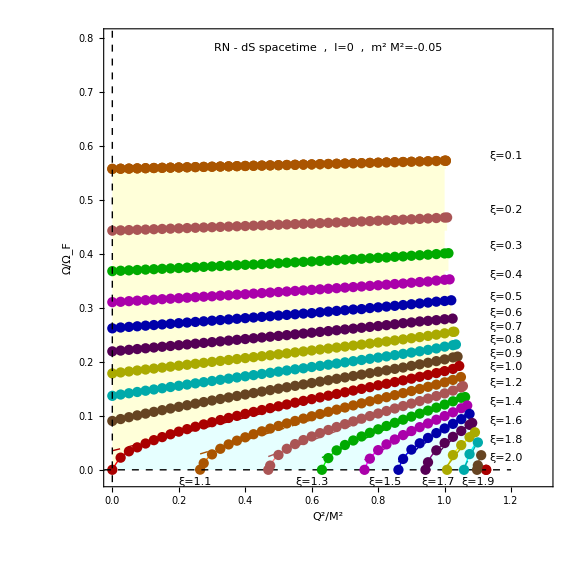

```mathematica
figomrelqm005ext=Show[fill1,plintomrel01q,plomrel01q,pllmfomtabrel01q,plintomrel01q,plomrel01q,pllmfomtabrel01q,plintomrel02q,plomrel02q,pllmfomtabrel02q,plintomrel03q,plomrel03q,pllmfomtabrel03q,plintomrel04q,plomrel04q,pllmfomtabrel04q,plintomrel05q,plomrel05q,pllmfomtabrel05q,plintomrel06q,plomrel06q,pllmfomtabrel06q,plintomrel07q,plomrel07q,pllmfomtabrel07q,plintomrel08q,plomrel08q,pllmfomtabrel08q,plintomrel09q,plomrel09q,pllmfomtabrel09q,plintomrel10q,plomrel10q,pllmfomtabrel10q,plintomrel11q,plomrel11q,pllmfomtabrel11q,plintomrel12q,plomrel12q,pllmfomtabrel12q,plintomrel13q,plomrel13q,pllmfomtabrel13q,plintomrel14q,plomrel14q,pllmfomtabrel14q,plintomrel15q,plomrel15q,pllmfomtabrel15q,plintomrel16q,plomrel16q,pllmfomtabrel16q,plintomrel17q,plomrel17q,pllmfomtabrel17q,plintomrel18q,plomrel18q,pllmfomtabrel18q,plintomrel19q,plomrel19q,pllmfomtabrel19q,plomrel20q,Graphics[{Inset[" RN - dS spacetime  ,  l=0  ,  m^2M^2=-0.05",{0.65,0.78},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["ξ=0.1  ",{1.185,0.58},BaseStyle->{Bold,Darker[Orange],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.2  ",{1.185,0.48},BaseStyle->{Bold,Darker[Pink],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.3  ",{1.185,0.415},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.4  ",{1.185,0.36},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.5  ",{1.185,0.32},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.6  ",{1.185,0.29},BaseStyle->{Bold,Darker[Purple],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.7  ",{1.185,0.265},BaseStyle->{Bold,Darker[Yellow],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.8  ",{1.185,0.24},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.9  ",{1.185,0.215},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.0  ",{1.185,0.19},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.2  ",{1.185,0.16},BaseStyle->{Bold,Darker[Pink],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.4 ",{1.185,0.125},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.6 ",{1.185,0.09 },BaseStyle->{Bold,Darker[Purple],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.8 ",{1.185,0.055},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=2.0 ",{1.185,0.022},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.1 ",{0.25,-0.022},BaseStyle->{Bold,Darker[Orange],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.3 ",{0.6,-0.022},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.5 ",{0.82,-0.022},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.7 ",{0.98,-0.022},BaseStyle->{Bold,Darker[Yellow],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.9 ",{1.1,-0.022},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],PlotRange->{{0,1.3},{-0.015,0.8}},Frame->True,FrameLabel->{"Q^2/M^2","Ω/Ω_F"},Axes->None,AspectRatio->1,Epilog->{{Dashed,Black,Line[{{-0.15,0},{1.2,0}}]},{Dashed,Black,Line[{{0,-0.1},{0,1.4}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

```mathematica
(* m^2 M^2=-0.2  *)
```

```mathematica
(* Table obtained from mathsfile: tables_fig6.nb   *)
```

```mathematica
omtabrelq={{0.,0.1,0.644306474273724},{0.025,0.1,0.6446987094962742},{0.05,0.1,0.6450922710257614},{0.07500000000000001,0.1,0.6454872298106684},{0.1,0.1,0.6458835878691176},{0.125,0.1,0.6462814000462495},{0.15000000000000002,0.1,0.6466806867550075},{0.17500000000000002,0.1,0.6470815511375503},{0.2,0.1,0.6474839079213088},{0.225,0.1,0.6478878167058161},{0.25,0.1,0.6482934345470781},{0.275,0.1,0.6487005047079049},{0.30000000000000004,0.1,0.6491093804253422},{0.325,0.1,0.6495201441249528},{0.35000000000000003,0.1,0.6499324749617525},{0.375,0.1,0.6503465247874811},{0.4,0.1,0.6507625944614157},{0.42500000000000004,0.1,0.6511805837319007},{0.45,0.1,0.6516005146675998},{0.47500000000000003,0.1,0.6520224778682443},{0.5,0.1,0.6524466186621041},{0.525,0.1,0.6528728345289402},{0.55,0.1,0.6533012707062362},{0.5750000000000001,0.1,0.6537320023210068},{0.6000000000000001,0.1,0.6541651038863815},{0.625,0.1,0.6546006242175336},{0.65,0.1,0.6550386877970903},{0.675,0.1,0.6554793746892124},{0.7000000000000001,0.1,0.655922920554698},{0.7250000000000001,0.1,0.6563693555777935},{0.75,0.1,0.6568188148264893},{0.775,0.1,0.6572714748098544},{0.8,0.1,0.6577272725532863},{0.8250000000000001,0.1,0.658186653724395},{0.8500000000000001,0.1,0.6586496967565006},{0.875,0.1,0.6591169871090287},{0.9,0.1,0.6595881242900024},{0.925,0.1,0.6600639479399298},{0.9500000000000001,0.1,0.6605446328073258},{0.9750000000000001,0.1,0.66103108737203},{1.,0.1,0.6615238826983413},{1.0250000000000001,0.1,0.6620239135144808-5.03221808150397*^-8 ⅈ},{1.05,0.1,0.6625321120273104-1.2271263865654683*^-6 ⅈ},{1.075,0.1,0.6630460743838595-5.588372292397236*^-6 ⅈ},{1.1,0.1,0.6516563117791963-0.004065442913827187 ⅈ},{1.125,0.1,0.6640842389151997-0.000030292850044121573 ⅈ},{0.,0.2,0.5388869089300489},{0.025,0.2,0.5395463348711996},{0.05,0.2,0.5402083181384131},{0.07500000000000001,0.2,0.5408729434226774},{0.1,0.2,0.5415399647719468},{0.125,0.2,0.5422093411440125},{0.15000000000000002,0.2,0.5428816229385736},{0.17500000000000002,0.2,0.5435564698520676},{0.2,0.2,0.5442340859417568},{0.225,0.2,0.5449146010953039},{0.25,0.2,0.5455978724556994},{0.275,0.2,0.5462842667884327},{0.30000000000000004,0.2,0.546973922574186},{0.325,0.2,0.547666606049662},{0.35000000000000003,0.2,0.5483627920781476},{0.375,0.2,0.5490623675291221},{0.4,0.2,0.5497653447403257},{0.42500000000000004,0.2,0.5504724496626466},{0.45,0.2,0.5511825645337692},{0.47500000000000003,0.2,0.5518969702766932},{0.5,0.2,0.5526152709623412},{0.525,0.2,0.5533377925861331},{0.55,0.2,0.5540648740910814},{0.5750000000000001,0.2,0.5547964810558939},{0.6000000000000001,0.2,0.5555326157633482},{0.625,0.2,0.5562739754189352},{0.65,0.2,0.5570205339854563},{0.675,0.2,0.5577722851941763},{0.7000000000000001,0.2,0.5585301859870312},{0.7250000000000001,0.2,0.5592938072933836},{0.75,0.2,0.5600637639650945},{0.775,0.2,0.5608403073142969},{0.8,0.2,0.5616242723546877},{0.8250000000000001,0.2,0.5624163009044667},{0.8500000000000001,0.2,0.5632159506174638},{0.875,0.2,0.564025066549724},{0.9,0.2,0.5648437926436285},{0.925,0.2,0.5656736516900942},{0.9500000000000001,0.2,0.5665153889997605},{0.9750000000000001,0.2,0.5673710546530851},{1.,0.2,0.568243549328055},{1.0250000000000001,0.2,0.5691366601659948-8.004604912388416*^-8 ⅈ},{1.05,0.2,0.559436656146924-0.003865089449684039 ⅈ},{1.075,0.2,0.5710060016700488-0.00007739386573085027 ⅈ},{1.1,0.2,0.5646247303463809+0.00519501996966729 ⅈ},{1.125,0.2,0.5728267732202689-0.00017822083671441838 ⅈ},{0.,0.30000000000000004,0.46307807194364614},{0.025,0.30000000000000004,0.4639985082698075},{0.05,0.30000000000000004,0.4649217237500284},{0.07500000000000001,0.30000000000000004,0.4658481232426818},{0.1,0.30000000000000004,0.46677810932646313},{0.125,0.30000000000000004,0.46771081921498636},{0.15000000000000002,0.30000000000000004,0.46864732285362537},{0.17500000000000002,0.30000000000000004,0.21514888509356708},{0.2,0.30000000000000004,0.4705310348295347},{0.225,0.30000000000000004,0.4714786435558732},{0.25,0.30000000000000004,0.4724299615022316},{0.275,0.30000000000000004,0.473385590312531},{0.30000000000000004,0.30000000000000004,0.47434525187534665},{0.325,0.30000000000000004,0.47530930784679204},{0.35000000000000003,0.30000000000000004,0.47627803370218946},{0.375,0.30000000000000004,0.47725125612057395},{0.4,0.30000000000000004,0.47822946256189086},{0.42500000000000004,0.30000000000000004,0.4792125525119661},{0.45,0.30000000000000004,0.4802013128202134},{0.47500000000000003,0.30000000000000004,8.373136558447383},{0.5,0.30000000000000004,0.4821946967366989},{0.525,0.30000000000000004,0.48320047215247713},{0.55,0.30000000000000004,0.48421238196500604},{0.5750000000000001,0.30000000000000004,0.4852308145213904},{0.6000000000000001,0.30000000000000004,0.4862563001948014},{0.625,0.30000000000000004,0.48728918797989035},{0.65,0.30000000000000004,0.48832930593820845},{0.675,0.30000000000000004,0.4893774529953044},{0.7000000000000001,0.30000000000000004,0.49043440421871415},{0.7250000000000001,0.30000000000000004,0.49150021698356555},{0.75,0.30000000000000004,0.4925759106638593},{0.775,0.30000000000000004,0.493661890242632},{0.8,0.30000000000000004,0.49475893009992306},{0.8250000000000001,0.30000000000000004,0.49586803698257736},{0.8500000000000001,0.30000000000000004,0.49699026433365207},{0.875,0.30000000000000004,0.4981267645622327},{0.9,0.30000000000000004,0.49927895398077515},{0.925,0.30000000000000004,0.500449465266094},{0.9500000000000001,0.30000000000000004,0.5016401233064413},{0.9750000000000001,0.30000000000000004,0.5028546057808988},{1.,0.30000000000000004,0.5040977786501842},{1.0250000000000001,0.30000000000000004,0.50537936000483-1.5361625950087206*^-8 ⅈ},{1.05,0.30000000000000004,0.506720666970622-0.000012856168392446853 ⅈ},{1.075,0.30000000000000004,0.49825844341890124-0.003864629701727272 ⅈ},{1.1,0.30000000000000004,0.509330733262501-0.00009750001233613309 ⅈ},{1.125,0.30000000000000004,0.024767213903274445+0.17655959492298212 ⅈ},{0.,0.4,0.4007909732051085},{0.025,0.4,0.4019893693870027},{0.05,0.4,0.4031913807585524},{0.07500000000000001,0.4,0.4043964462798098},{0.1,0.4,0.4056045989619019},{0.125,0.4,0.40681661351121795},{0.15000000000000002,0.4,0.40803249287490967},{0.17500000000000002,0.4,0.4092519161513388},{0.2,0.4,0.41047574499048645},{0.225,0.4,0.4117036971315596},{0.25,0.4,0.41293603104972854},{0.275,0.4,0.4141727346099658},{0.30000000000000004,0.4,0.4154146001913482},{0.325,0.4,0.4166611140461762},{0.35000000000000003,0.4,0.4179130479782601},{0.375,0.4,0.41917081994255045},{0.4,0.4,0.42043369424048427},{0.42500000000000004,0.4,0.4217029362142622},{0.45,0.4,0.4229783166133215},{0.47500000000000003,0.4,0.42426042737306907},{0.5,0.4,0.4255495222096017},{0.525,0.4,0.42684587703899846},{0.55,0.4,0.42814990803015157},{0.5750000000000001,0.4,0.42946234884940077},{0.6000000000000001,0.4,0.4307832398658811},{0.625,0.4,0.4321131450177291},{0.65,0.4,0.4334528947087907},{0.675,0.4,0.434802925351611},{0.7000000000000001,0.4,0.43616378730054217},{0.7250000000000001,0.4,0.43753668532777246},{0.75,0.4,0.4389224196437593},{0.775,0.4,0.44032154089418535},{0.8,0.4,0.4417354112549487},{0.8250000000000001,0.4,0.4431659800927269},{0.8500000000000001,0.4,0.44461423195144395},{0.875,0.4,0.4460820435827927},{0.9,0.4,0.44757197604329346},{0.925,0.4,0.449072286315855},{0.9500000000000001,0.4,0.45063105164371015},{0.9750000000000001,0.4,0.45220975338396163},{1.,0.4,0.4538229350712247},{1.0250000000000001,0.4,1.3729582271507434-0.007012232177108284 ⅈ},{1.05,0.4,0.43407834781814025-0.0030273263658723236 ⅈ},{1.075,0.4,0.45514264669887355+0.0013851187407973118 ⅈ},{1.1,0.4,0.4586078102606836-0.00017588078020435615 ⅈ},{1.125,0.4,0.4630865482315737-0.004870438861609039 ⅈ},{0.,0.5,0.3457778667824016},{0.025,0.5,0.34729402134973925},{0.05,0.5,0.3488124138490203},{0.07500000000000001,0.5,0.3503333407555174},{0.1,0.5,0.351857235118038},{0.125,0.5,0.3533836497098984},{0.15000000000000002,0.5,0.35491300314389074},{0.17500000000000002,0.5,0.356445810421918},{0.2,0.5,0.35798223506087196},{0.225,0.5,0.3595225437389603},{0.25,0.5,0.36106661842718457},{0.275,0.5,0.3626149170857763},{0.30000000000000004,0.5,0.3641675875022096},{0.325,0.5,0.365725604978809},{0.35000000000000003,0.5,0.36728843338862743},{0.375,0.5,0.3688567632540866},{0.4,0.5,0.3704311689636033},{0.42500000000000004,0.5,0.3720115998889615},{0.45,0.5,0.37359838467370826},{0.47500000000000003,0.5,0.3751929792815889},{0.5,0.5,0.376793831178677},{0.525,0.5,0.37840367700549354},{0.55,0.5,0.3800213137871739},{0.5750000000000001,0.5,0.38164843811985655},{0.6000000000000001,0.5,0.383284705642531},{0.625,0.5,0.3849319166193402},{0.65,0.5,0.38658993986418555},{0.675,0.5,0.3882603144828608},{0.7000000000000001,0.5,0.38994335608554825},{0.7250000000000001,0.5,0.39164032995527776},{0.75,0.5,0.39335256021414816},{0.775,0.5,0.39508129438374073},{0.8,0.5,0.3968281826722649},{0.8250000000000001,0.5,0.3985954129419595},{0.8500000000000001,0.5,0.4003842335711181},{0.875,0.5,0.40219798902279963},{0.9,0.5,0.4040398453553431},{0.925,0.5,0.4059139034273098},{0.9500000000000001,0.5,0.4078259429784283},{0.9750000000000001,0.5,0.40978313031049374},{1.,0.5,0.09030439250309025},{1.0250000000000001,0.5,0.413890924732751-1.515899012785283*^-9 ⅈ},{1.05,0.5,0.41041653986895055+0.01358094283544853 ⅈ},{1.075,0.5,0.4047666870165154-0.024624417205126994 ⅈ},{1.1,0.5,0.4206028462199899-0.00029081293790551263 ⅈ},{1.125,0.5,0.422720570731178-0.0009613472098123902 ⅈ},{0.,0.6,0.2945164046617039},{0.025,0.6,0.29642118153228764},{0.05,0.6,0.29832537417958405},{0.07500000000000001,0.6,0.3002290594310022},{0.1,0.6,0.302132726943143},{0.125,0.6,0.3040367997013255},{0.15000000000000002,0.6,0.30594118434722906},{0.17500000000000002,0.6,0.30784655491603585},{0.2,0.6,0.3097531694560561},{0.225,0.6,0.31166144039663274},{0.25,0.6,0.31357141429196006},{0.275,0.6,0.3154839447415758},{0.30000000000000004,0.6,0.31739911115888947},{0.325,0.6,0.3193174055463963},{0.35000000000000003,0.6,0.3212392671325229},{0.375,0.6,0.3231652358478808},{0.4,0.6,0.325095368518092},{0.42500000000000004,0.6,0.32703063988264564},{0.45,0.6,0.3289714340703661},{0.47500000000000003,0.6,0.33091826330006446},{0.5,0.6,0.33287189804165873},{0.525,0.6,0.33483255354974567},{0.55,0.6,0.3368016401916511},{0.5750000000000001,0.6,0.33877917401039825},{0.6000000000000001,0.6,0.34076636472473293},{0.625,0.6,0.3427643714963708},{0.65,0.6,0.3447738450313398},{0.675,0.6,0.3467956052711809},{0.7000000000000001,0.6,0.3488315961079817},{0.7250000000000001,0.6,0.35088222891433857},{0.75,0.6,0.35294972810252073},{0.775,0.6,0.3550358319456427},{0.8,0.6,0.3571423437746506},{0.8250000000000001,0.6,0.359272096401672},{0.8500000000000001,0.6,0.3614273660146988},{0.875,0.6,0.36361165566067893},{0.9,0.6,0.365829731000266},{0.925,0.6,0.3680864314533126},{0.9500000000000001,0.6,0.37038945474651963},{0.9750000000000001,0.6,0.3727485821096702},{1.,0.6,0.3751794904355857},{1.0250000000000001,0.6,0.37770988163265257+6.230108260146485*^-9 ⅈ},{1.05,0.6,0.3803873153061279-0.00005319270275232304 ⅈ},{1.075,0.6,0.07292948482878389-0.03099215328977419 ⅈ},{1.1,0.6,-0.0060903007308912935+0.2170549367435539 ⅈ},{1.125,0.6,0.3876999616156894-0.0022572416921876897 ⅈ},{0.,0.7000000000000001,0.24426484554089586},{0.025,0.7000000000000001,0.2466894206736213},{0.05,0.7000000000000001,0.24910548578000505},{0.07500000000000001,0.7000000000000001,0.251513529022748},{0.1,0.7000000000000001,0.25391395194153965},{0.125,0.7000000000000001,0.2563076457490619},{0.15000000000000002,0.7000000000000001,0.258695036105011},{0.17500000000000002,0.7000000000000001,0.2610768785028073},{0.2,0.7000000000000001,0.2634538878853582},{0.225,0.7000000000000001,0.2658266193319596},{0.25,0.7000000000000001,0.26819532893503895},{0.275,0.7000000000000001,0.27056108039930576},{0.30000000000000004,0.7000000000000001,0.27292437111060713},{0.325,0.7000000000000001,0.2752858057459593},{0.35000000000000003,0.7000000000000001,0.2776463117076196},{0.375,0.7000000000000001,0.2800062742700973},{0.4,0.7000000000000001,0.28236661359515186},{0.42500000000000004,0.7000000000000001,0.28472798259673987},{0.45,0.7000000000000001,0.2870910977495134},{0.47500000000000003,0.7000000000000001,0.289456838018028},{0.5,0.7000000000000001,0.2918262635665041},{0.525,0.7000000000000001,0.29419969115794403},{0.55,0.7000000000000001,0.2965785574371303},{0.5750000000000001,0.7000000000000001,0.29896360583466514},{0.6000000000000001,0.7000000000000001,0.30135650422111815},{0.625,0.7000000000000001,0.3037576174597818},{0.65,0.7000000000000001,0.30616888666357206},{0.675,0.7000000000000001,0.308591059608006},{0.7000000000000001,0.7000000000000001,0.3110265101675695},{0.7250000000000001,0.7000000000000001,0.31347651686229794},{0.75,0.7000000000000001,0.31594303874232094},{0.775,0.7000000000000001,0.318428416672224},{0.8,0.7000000000000001,0.3209353169092584},{0.8250000000000001,0.7000000000000001,0.32346646148711655},{0.8500000000000001,0.7000000000000001,0.32602567870932486},{0.875,0.7000000000000001,0.32861725046173057},{0.9,0.7000000000000001,0.3312462674233961},{0.925,0.7000000000000001,0.3339196112249925},{0.9500000000000001,0.7000000000000001,0.33664649610856023},{0.9750000000000001,0.7000000000000001,-0.007565972628710209},{1.,0.7000000000000001,0.3423185577228759},{1.0250000000000001,0.7000000000000001,0.34531737326523},{1.05,0.7000000000000001,0.34848300680794175-9.470725309352306*^-6 ⅈ},{1.075,0.7000000000000001,0.022661904101240495-0.04394896481637737 ⅈ},{1.1,0.7000000000000001,0.341463303500931+0.02429273889024632 ⅈ},{1.125,0.7000000000000001,0.03336370933835042-0.055148542554632786 ⅈ},{0.,0.8,0.19182788318401314},{0.025,0.8,0.19505367976581267},{0.05,0.8,0.19824704981807736},{0.07500000000000001,0.8,0.20140980294877592},{0.1,0.8,0.20454396489787682},{0.125,0.8,0.2076516476120992},{0.15000000000000002,0.8,0.21073417475912667},{0.17500000000000002,0.8,0.21379371943258343},{0.2,0.8,0.21683143308337058},{0.225,0.8,0.21984917140755256},{0.25,0.8,0.22284817202732618},{0.275,0.8,0.22583006885770462},{0.30000000000000004,0.8,0.2287961892353881},{0.325,0.8,0.23174810425698994},{0.35000000000000003,0.8,0.23468689757464886},{0.375,0.8,0.23761403705786036},{0.4,0.8,0.24053091014265582},{0.42500000000000004,0.8,0.24343871945463033},{0.45,0.8,0.2463389600194682},{0.47500000000000003,0.8,0.24923290763648923},{0.5,0.8,0.25212194723342785},{0.525,0.8,0.2550075406788507},{0.55,0.8,0.2578909538835076},{0.5750000000000001,0.8,0.26077391072432715},{0.6000000000000001,0.8,0.26365836322097846},{0.625,0.8,0.2665447929460557},{0.65,0.8,0.2694361737726159},{0.675,0.8,0.2723340592967886},{0.7000000000000001,0.8,0.27524046997957274},{0.7250000000000001,0.8,0.27815765265366377},{0.75,0.8,0.28108840392829304},{0.775,0.8,0.2840351111901296},{0.8,0.8,0.2870016798344614},{0.8250000000000001,0.8,0.28999126491016586},{0.8500000000000001,0.8,0.2930082894147789},{0.875,0.8,0.2960592258642685},{0.9,0.8,0.2991493224552286},{0.925,0.8,0.30228726285522944},{0.9500000000000001,0.8,0.3054842752703768},{0.9750000000000001,0.8,0.3087557067924915},{1.,0.8,0.3121248851424514},{1.0250000000000001,0.8,0.315632416585468},{1.05,0.8,0.3193779177256326-9.036474101654456*^-6 ⅈ},{1.075,0.8,0.2979447213113595-0.036739495645822365 ⅈ},{1.1,0.8,0.3243675502053603+0.008743605435442567 ⅈ},{1.125,0.8,0.3315457120675942-0.002165155150939275 ⅈ},{0.,0.9,0.13080376515217482},{0.025,0.9,0.13568891426926136},{0.05,0.9,0.14043327487319263},{0.07500000000000001,0.9,0.14505138698015407},{0.1,0.9,0.14955578081768003},{0.125,0.9,0.15395726797578327},{0.15000000000000002,0.9,0.15826539473821258},{0.17500000000000002,0.9,0.1624883671567034},{0.2,0.9,0.16663350431498128},{0.225,0.9,0.17070763104688466},{0.25,0.9,0.17471650214006984},{0.275,0.9,0.17866562051490723},{0.30000000000000004,0.9,0.18255981663418797},{0.325,0.9,0.18640366592887125},{0.35000000000000003,0.9,0.1902012586815779},{0.375,0.9,0.19395652497227328},{0.4,0.9,0.19767303803225333},{0.42500000000000004,0.9,0.20135432815993534},{0.45,0.9,0.20500353226174653},{0.47500000000000003,0.9,0.20862372560665293},{0.5,0.9,0.21221815734834404},{0.525,0.9,0.21578938312192988},{0.55,0.9,0.21934058348073823},{0.5750000000000001,0.9,0.22287422502672957},{0.6000000000000001,0.9,0.22639337953918048},{0.625,0.9,0.2299008175116163},{0.65,0.9,0.2333993761897202},{0.675,0.9,0.2368922316914468},{0.7000000000000001,0.9,0.24038234780629747},{0.7250000000000001,0.9,0.24387295022617173},{0.75,0.9,0.24736783718128375},{0.775,0.9,0.25087057398546453},{0.8,0.9,0.2543857186444752},{0.8250000000000001,0.9,0.257918208543947},{0.8500000000000001,0.9,0.2614734844741368},{0.875,0.9,0.016569219035217325},{0.9,0.9,0.26868057617687946},{0.925,0.9,0.2723505933381601},{0.9500000000000001,0.9,0.27608160835733675},{0.9750000000000001,0.9,0.27989174939824735},{1.,0.9,0.28380885415215995},{1.0250000000000001,0.9,0.28787998731731124},{1.05,0.9,1.994465274860174-0.00469076053880986 ⅈ},{1.075,0.9,0.2719189904767633+0.10334233755325675 ⅈ},{1.1,0.9,0.30152243853790683-0.0012434210384819268 ⅈ},{1.125,0.9,0.022887434410467446-0.09149386053442178 ⅈ},{0.,1.,-5.128158101066744*^-9},{0.025,1.,0.033505017283280335},{0.05,1.,0.05040593953580662},{0.07500000000000001,1.,0.0627815995903743},{0.1,1.,0.07302518111519801},{0.125,1.,0.08200672614261112},{0.15000000000000002,1.,0.09013396717107952},{0.17500000000000002,1.,0.09763238978084535},{0.2,1.,0.10464219832134698},{0.225,1.,0.1112581526992003},{0.25,1.,0.11754827871780159},{0.275,1.,0.12356380768639853},{0.30000000000000004,1.,0.12934435000035105},{0.325,1.,0.13492156384663945},{0.35000000000000003,1.,0.14032132893426508},{0.375,1.,0.14556500125536773},{0.4,1.,0.15067072583921068},{0.42500000000000004,1.,0.15565367302406105},{0.45,1.,0.1605272827356864},{0.47500000000000003,1.,6.461448321401202},{0.5,1.,0.16999159872613404},{0.525,1.,0.1746019701421934},{0.55,1.,0.1791425492390888},{0.5750000000000001,1.,0.18362080748430773},{0.6000000000000001,1.,0.18804402122877978},{0.625,1.,0.19241868401358064},{0.65,1.,0.19675122713506768},{0.675,1.,0.20104735097705856},{0.7000000000000001,1.,0.20531337587653736},{0.7250000000000001,1.,0.20955501824103318},{0.75,1.,0.21377820574095963},{0.775,1.,0.21798883405005726},{0.8,1.,0.22219369459976634},{0.8250000000000001,1.,0.22639949871020262},{0.8500000000000001,1.,0.2306143174842335},{0.875,1.,0.234846351881642},{0.9,1.,0.23910622723489558},{0.925,1.,0.24340652398605572},{0.9500000000000001,1.,0.24776324823117674},{0.9750000000000001,1.,0.25219806661105665},{1.,1.,0.25674337512204},{1.0250000000000001,1.,0.2614527220961483},{1.05,1.,0.26644681836393375+5.345182351053477*^-7 ⅈ},{1.075,1.,0.3687840254612849+0.03876561919300138 ⅈ},{1.1,1.,0.28895936029191355-0.01144755458105928 ⅈ},{1.125,1.,0.2807505844578406-0.030227409016683696 ⅈ},{0.,1.1,1.584967387023358+0.08004314923747598 ⅈ},{0.025,1.1,1.3403632567925172+0.00021291400065653307 ⅈ},{0.05,1.1,1.271101533515094-0.005828874615020754 ⅈ},{0.07500000000000001,1.1,1.3388637157198453+0.0005215445814890517 ⅈ},{0.1,1.1,1.3253127009440662-0.009253693328915727 ⅈ},{0.125,1.1,1.2733516206493791-0.06283363185968222 ⅈ},{0.15000000000000002,1.1,1.2074177009191778-0.14914697762492415 ⅈ},{0.17500000000000002,1.1,0.5818599489411569+0.0401553710935391 ⅈ},{0.2,1.1,0.0036952914869964344+0.19320393710668327 ⅈ},{0.225,1.1,25.85373585305638+0. ⅈ},{0.25,1.1,7.838185917409885+0. ⅈ},{0.275,1.1,0.020873430092829888},{0.30000000000000004,1.1,0.04462634283494942},{0.325,1.1,0.05963566331719914},{0.35000000000000003,1.1,0.07147280972679816},{0.375,1.1,0.08163429278492712},{0.4,1.1,0.09072616335382334},{0.42500000000000004,1.1,0.0990575907968633},{0.45,1.1,0.106812187443092},{0.47500000000000003,1.1,0.11411070012824222},{0.5,1.1,0.12103823696469476},{0.525,1.1,0.12765800393453247},{0.55,1.1,0.1340185713611752},{0.5750000000000001,1.1,0.14015868471536236},{0.6000000000000001,1.1,0.1461095219268278},{0.625,1.1,0.15189717062290126},{0.65,1.1,0.15754381617492935},{0.675,1.1,0.1630683905475812},{0.7000000000000001,1.1,0.16848771322409886},{0.7250000000000001,1.1,0.17381709239685347},{0.75,1.1,0.17906988254180184},{0.775,1.1,0.18425959163908395},{0.8,1.1,0.1893984234880687},{0.8250000000000001,1.1,0.19449816896578828},{0.8500000000000001,1.1,0.19957200513269996},{0.875,1.1,0.20463294663649195},{0.9,1.1,0.20969578303602676},{0.925,1.1,0.2147769874165004},{0.9500000000000001,1.1,0.2198974194576811},{0.9750000000000001,1.1,0.22508289224322986},{1.,1.1,0.2303719559195369},{1.0250000000000001,1.1,0.23582518669497252},{1.05,1.1,0.241567793899671+3.320382572786347*^-7 ⅈ},{1.075,1.1,0.012914970114071521-0.09607917715932593 ⅈ},{1.1,1.1,0.25401851624599175-0.0015145121922262902 ⅈ},{1.125,1.1,0.2595664616106911-0.0010559417529422228 ⅈ},{0.,1.2000000000000002,2.1162948856027466+0.299917504099859 ⅈ},{0.025,1.2000000000000002,0.015826323722767096+0.5902297605619213 ⅈ},{0.05,1.2000000000000002,1.3319241056583397+0.00012003991308155944 ⅈ},{0.07500000000000001,1.2000000000000002,0.49890020160424575+0.034588501498489986 ⅈ},{0.1,1.2000000000000002,0.02289943333928799+0.38886790745670285 ⅈ},{0.125,1.2000000000000002,1.2076602416961366+0.02763163169695839 ⅈ},{0.15000000000000002,1.2000000000000002,1.3412303449100387+0.0011410718946555703 ⅈ},{0.17500000000000002,1.2000000000000002,1.3203304057854874+0.0005764088438523677 ⅈ},{0.2,1.2000000000000002,1.3274646239267887-0.0011776779212469984 ⅈ},{0.225,1.2000000000000002,1.2089266967751666+0.026052866100529076 ⅈ},{0.25,1.2000000000000002,1.466102916723128-0.23308237330301698 ⅈ},{0.275,1.2000000000000002,1.5050016868136844-0.015019105155337263 ⅈ},{0.30000000000000004,1.2000000000000002,1.3249171776926836+0.0031967107441116314 ⅈ},{0.325,1.2000000000000002,1.341669169763009-0.00009677339973837894 ⅈ},{0.35000000000000003,1.2000000000000002,1.3760532124331049-0.0008736108234534248 ⅈ},{0.375,1.2000000000000002,1.2752264233378998+0.1639340748684419 ⅈ},{0.4,1.2000000000000002,1.4826517333217164-0.03694972538793388 ⅈ},{0.42500000000000004,1.2000000000000002,-0.003484068743272822+0.24570436238363175 ⅈ},{0.45,1.2000000000000002,3.134959315237544+0. ⅈ},{0.47500000000000003,1.2000000000000002,0.013940664218357157},{0.5,1.2000000000000002,0.04339614234306374},{0.525,1.2000000000000002,0.06017641925500092},{0.55,1.2000000000000002,0.07314029961945412},{0.5750000000000001,1.2000000000000002,0.08419952164425357},{0.6000000000000001,1.2000000000000002,0.09407058950021409},{0.625,1.2000000000000002,0.1031086917474807},{0.65,1.2000000000000002,0.11152292164798153},{0.675,1.2000000000000002,0.11945064557386563},{0.7000000000000001,1.2000000000000002,0.12698883194198005},{0.7250000000000001,1.2000000000000002,0.13420989525802485},{0.75,1.2000000000000002,0.14116990037427904},{0.775,1.2000000000000002,0.14791419448067364},{0.8,1.2000000000000002,0.15448028058783878},{0.8250000000000001,1.2000000000000002,0.1609006919683332},{0.8500000000000001,1.2000000000000002,0.16720425083729457},{0.875,1.2000000000000002,0.17341803019879626},{0.9,1.2000000000000002,0.1795679301606302},{0.925,1.2000000000000002,0.18568106288367114},{0.9500000000000001,1.2000000000000002,0.1917871795023151},{0.9750000000000001,1.2000000000000002,0.19792164119796982},{1.,1.2000000000000002,0.20413097368782981},{1.0250000000000001,1.2000000000000002,0.21048579237334594},{1.05,1.2000000000000002,0.2171197507921699},{1.075,1.2000000000000002,0.2243892841485023-0.00018646578182605 ⅈ},{1.1,1.2000000000000002,0.23182964816863685-0.0016412887729853488 ⅈ},{1.125,1.2000000000000002,0.23895446078977667-0.004019302914592701 ⅈ},{0.,1.3000000000000003,0.40939712611079865-0.02129554946034233 ⅈ},{0.025,1.3000000000000003,1.5820937433192062+0.003944565273071498 ⅈ},{0.05,1.3000000000000003,1.3276509697463985-0.00950931477300224 ⅈ},{0.07500000000000001,1.3000000000000003,1.341918361087457+1.1734308629110667*^-6 ⅈ},{0.1,1.3000000000000003,0.4212855476145098-0.026906165233231513 ⅈ},{0.125,1.3000000000000003,1.474393375606899-0.07159091216017795 ⅈ},{0.15000000000000002,1.3000000000000003,0.6340821253671536+0.13664326421516168 ⅈ},{0.17500000000000002,1.3000000000000003,0.05677757582864568+0.5511276322246935 ⅈ},{0.2,1.3000000000000003,1.3872719090408512-0.005112810585162932 ⅈ},{0.225,1.3000000000000003,-0.004193312059396976-0.4257099976272668 ⅈ},{0.25,1.3000000000000003,1.3416364653768138-1.0811313302165825*^-7 ⅈ},{0.275,1.3000000000000003,1.344173775206228+0.00042941545356093994 ⅈ},{0.30000000000000004,1.3000000000000003,-0.0003573586147066775-0.34629432869068116 ⅈ},{0.325,1.3000000000000003,0.021667846040806432-0.4478481929574664 ⅈ},{0.35000000000000003,1.3000000000000003,0.5179387755734305-0.05335932401454007 ⅈ},{0.375,1.3000000000000003,1.4455802386275491+0.20036875247545058 ⅈ},{0.4,1.3000000000000003,1.6146575676222152-0.12416922973305747 ⅈ},{0.42500000000000004,1.3000000000000003,1.3636181875962772-0.01807660420333915 ⅈ},{0.45,1.3000000000000003,1.3430463509102388-0.004054113806141581 ⅈ},{0.47500000000000003,1.3000000000000003,1.3509440226832223+0.0031344180768055952 ⅈ},{0.5,1.3000000000000003,1.390984383882217+0.0022264585756556904 ⅈ},{0.525,1.3000000000000003,1.3143309645555492-0.00831461725883115 ⅈ},{0.55,1.3000000000000003,1.3380145833986146-0.004979107008268352 ⅈ},{0.5750000000000001,1.3000000000000003,1.3415968546028079+0.000012989654281759138 ⅈ},{0.6000000000000001,1.3000000000000003,3.1310709788415907+0. ⅈ},{0.625,1.3000000000000003,6.719533792502268+0. ⅈ},{0.65,1.3000000000000003,0.03510859045168449},{0.675,1.3000000000000003,0.056311348029382854},{0.7000000000000001,1.3000000000000003,0.07138936105801141},{0.7250000000000001,1.3000000000000003,0.08390970113220385},{0.75,1.3000000000000003,0.09495330910143417},{0.775,1.3000000000000003,0.10500719092220266},{0.8,1.3000000000000003,0.11434498179756258},{0.8250000000000001,1.3000000000000003,0.12314253182654977},{0.8500000000000001,1.3000000000000003,0.13152326121796146},{0.875,1.3000000000000003,0.1395802573282295},{0.9,1.3000000000000003,0.14738771081413557},{0.925,1.3000000000000003,0.1550090669203505},{0.9500000000000001,1.3000000000000003,0.16250268258085618},{0.9750000000000001,1.3000000000000003,0.16992722245046007},{1.,1.3000000000000003,0.1773492323086135},{1.0250000000000001,1.3000000000000003,0.18485725217793825},{1.05,1.3000000000000003,0.19260041895970184},{1.075,1.3000000000000003,0.20096597631775356-0.00009300441018174976 ⅈ},{1.1,1.3000000000000003,0.20986215423253082-0.0016561562875678495 ⅈ},{1.125,1.3000000000000003,0.21765268895780449-0.004356033909500011 ⅈ},{0.,1.4000000000000001,0.4033908965113124+0.10611648441131553 ⅈ},{0.025,1.4000000000000001,1.3331523538852594-0.0067103741046405626 ⅈ},{0.05,1.4000000000000001,0.39197229747036855-0.05948836442840178 ⅈ},{0.07500000000000001,1.4000000000000001,1.5467455038723494+0.08010539698813043 ⅈ},{0.1,1.4000000000000001,0.368421412673666-0.026528419467717605 ⅈ},{0.125,1.4000000000000001,1.3088482871785825+0.00022931548014184114 ⅈ},{0.15000000000000002,1.4000000000000001,-0.0073534800132736946+0.42593904469420846 ⅈ},{0.17500000000000002,1.4000000000000001,0.009739269756856192+0.5128662237373204 ⅈ},{0.2,1.4000000000000001,0.4515567877775732-0.019700276284135437 ⅈ},{0.225,1.4000000000000001,0.47187980286179787-0.02086771560606656 ⅈ},{0.25,1.4000000000000001,1.3416408657201426+1.4407295186533221*^-8 ⅈ},{0.275,1.4000000000000001,0.5461712289874242+0.012649577452280689 ⅈ},{0.30000000000000004,1.4000000000000001,0.4714599331701476-0.03723503859116706 ⅈ},{0.325,1.4000000000000001,0.09566133465160424+0.14261601502353127 ⅈ},{0.35000000000000003,1.4000000000000001,1.430065898036813-0.09583076736565992 ⅈ},{0.375,1.4000000000000001,1.3958597393351273+0.005557167088992463 ⅈ},{0.4,1.4000000000000001,1.2648687843625357+0.012195057180518975 ⅈ},{0.42500000000000004,1.4000000000000001,1.396143814037038+0.1745147367057104 ⅈ},{0.45,1.4000000000000001,0.48707149251189036-0.0783472553907453 ⅈ},{0.47500000000000003,1.4000000000000001,-0.0015202514252923949-0.3365931255011845 ⅈ},{0.5,1.4000000000000001,0.885351975371415+0.06980155766593131 ⅈ},{0.525,1.4000000000000001,1.3416407864998674+4.989609552058034*^-15 ⅈ},{0.55,1.4000000000000001,1.340891807499852+0.0007485905095259663 ⅈ},{0.5750000000000001,1.4000000000000001,1.3413101443553088+0.00044189989037775356 ⅈ},{0.6000000000000001,1.4000000000000001,1.329264128946273+0.0031413888472308048 ⅈ},{0.625,1.4000000000000001,1.3317619322283258+0.006382275501880109 ⅈ},{0.65,1.4000000000000001,1.333136728158043-0.01485514904420825 ⅈ},{0.675,1.4000000000000001,1.3281481368679966-0.002690713349450801 ⅈ},{0.7000000000000001,1.4000000000000001,1.3415265908637004+0.0036696018653024284 ⅈ},{0.7250000000000001,1.4000000000000001,0.011664507511272444-0.30749290737183105 ⅈ},{0.75,1.4000000000000001,7.658234312440094+0. ⅈ},{0.775,1.4000000000000001,0.03370859429906337},{0.8,1.4000000000000001,0.057395979073795185},{0.8250000000000001,1.4000000000000001,0.07382909492207287},{0.8500000000000001,1.4000000000000001,0.0874385583592866},{0.875,1.4000000000000001,0.09946157117878297},{0.9,1.4000000000000001,0.11044933893060944},{0.925,1.4000000000000001,0.12071624358197262},{0.9500000000000001,1.4000000000000001,0.1304715276883676},{0.9750000000000001,1.4000000000000001,0.13987331333563763},{1.,1.4000000000000001,0.1490578851174873},{1.0250000000000001,1.4000000000000001,0.15816556917085636},{1.05,1.4000000000000001,0.1673840511140431},{1.075,1.4000000000000001,0.1771494119425762+0.000026760682732940323 ⅈ},{1.1,1.4000000000000001,0.18773646600976518-0.0015635269424432404 ⅈ},{1.125,1.4000000000000001,0.19752094929185368-0.004899244188117514 ⅈ},{0.,1.5000000000000002,1.3418373612334933+0.000021364030405748632 ⅈ},{0.025,1.5000000000000002,0.010963875526778168+0.21570481705308953 ⅈ},{0.05,1.5000000000000002,0.08561217385329561+0.011755160930499147 ⅈ},{0.07500000000000001,1.5000000000000002,1.1058051609473556+0.0473300901198638 ⅈ},{0.1,1.5000000000000002,1.3416407864266295-1.0672380459225304*^-11 ⅈ},{0.125,1.5000000000000002,1.3619816559982272+0.0043481196705093175 ⅈ},{0.15000000000000002,1.5000000000000002,1.341640727099119-5.716512597652533*^-7 ⅈ},{0.17500000000000002,1.5000000000000002,-0.006562640301999059-0.377419657647142 ⅈ},{0.2,1.5000000000000002,0.29785765468834163-0.06442708776123061 ⅈ},{0.225,1.5000000000000002,1.3421634992166167+0.001108619464361023 ⅈ},{0.25,1.5000000000000002,0.56473478786239+0.01879989694661282 ⅈ},{0.275,1.5000000000000002,0.46378766387380044-0.0418260522956784 ⅈ},{0.30000000000000004,1.5000000000000002,0.1415855295430832+0.21086201610159686 ⅈ},{0.325,1.5000000000000002,0.37069203348369945-0.4492044486930562 ⅈ},{0.35000000000000003,1.5000000000000002,0.010480475446736593+0.17336509303681488 ⅈ},{0.375,1.5000000000000002,-0.002856612638431891-0.38587649996930234 ⅈ},{0.4,1.5000000000000002,0.11538601881417983-0.011086499800471526 ⅈ},{0.42500000000000004,1.5000000000000002,0.5789751828363555-0.01833106114400456 ⅈ},{0.45,1.5000000000000002,0.4758982352119646-0.09223560514142813 ⅈ},{0.47500000000000003,1.5000000000000002,0.697761135126567-0.03276165326787284 ⅈ},{0.5,1.5000000000000002,1.3427468997093286-0.010475937607171143 ⅈ},{0.525,1.5000000000000002,0.9797396640807415+0.33157078783160654 ⅈ},{0.55,1.5000000000000002,1.3857130332125742+0.0001616805384238416 ⅈ},{0.5750000000000001,1.5000000000000002,1.3436972090781092+0.02713964636601289 ⅈ},{0.6000000000000001,1.5000000000000002,0.03186439593785516-0.3626419063356241 ⅈ},{0.625,1.5000000000000002,0.8301261038186661+0.14874468673256735 ⅈ},{0.65,1.5000000000000002,1.341646222022055+1.1467062238937326*^-6 ⅈ},{0.675,1.5000000000000002,1.2838566792894754-0.0031705606318328267 ⅈ},{0.7000000000000001,1.5000000000000002,1.3403221018568119+0.006676481733825397 ⅈ},{0.7250000000000001,1.5000000000000002,1.3970537913641679+0.004722675219913122 ⅈ},{0.75,1.5000000000000002,1.3174392260317707+0.003057118196994084 ⅈ},{0.775,1.5000000000000002,1.3440625415162022+0.030838099290306505 ⅈ},{0.8,1.5000000000000002,1.2442916177240402+0.0013854771678333724 ⅈ},{0.8250000000000001,1.5000000000000002,1.185735216133942-0.05904501568376121 ⅈ},{0.8500000000000001,1.5000000000000002,6.423172626384407+0. ⅈ},{0.875,1.5000000000000002,0.03310157801748766},{0.9,1.5000000000000002,0.05927532534900703},{0.925,1.5000000000000002,0.07716393969553237},{0.9500000000000001,1.5000000000000002,0.09202600679480882},{0.9750000000000001,1.5000000000000002,0.1052549032738818},{1.,1.5000000000000002,0.11749018912673939},{1.0250000000000001,1.5000000000000002,0.12913503731692993},{1.05,1.5000000000000002,0.14053325778145997},{1.075,1.5000000000000002,0.15213598027695227},{1.1,1.5000000000000002,0.16493905172122658-0.0013036408444955536 ⅈ},{1.125,1.5000000000000002,0.17674659706807275-0.00521671908062451 ⅈ},{0.,1.6,0.21795512988524182-0.058489783160490166 ⅈ},{0.025,1.6,1.6256277223715552-0.17921948751034883 ⅈ},{0.05,1.6,1.3414855027022454-0.00003037261216434001 ⅈ},{0.07500000000000001,1.6,0.5513809974682478+0.0943559063801499 ⅈ},{0.1,1.6,1.4842600374486696-0.0021296003188511618 ⅈ},{0.125,1.6,0.0633511117071774+0.015034576457004806 ⅈ},{0.15000000000000002,1.6,0.3925117941143054-0.03753542425435385 ⅈ},{0.17500000000000002,1.6,1.3464158329283547-3.2113252840668405*^-6 ⅈ},{0.2,1.6,0.315610590355306-0.07286255514242047 ⅈ},{0.225,1.6,0.08967126485389519+0.3387293866337585 ⅈ},{0.25,1.6,0.689149889448087+0.013181927778501969 ⅈ},{0.275,1.6,0.5088222493390168+0.02664211919906043 ⅈ},{0.30000000000000004,1.6,-0.00013265144576834066-0.18306754298582198 ⅈ},{0.325,1.6,1.3319955563382535+0.005890735198183974 ⅈ},{0.35000000000000003,1.6,1.3416407881862298+2.200709129486726*^-8 ⅈ},{0.375,1.6,0.015941227915630046+0.16815539684302988 ⅈ},{0.4,1.6,1.5467742836916956-0.024566426927503784 ⅈ},{0.42500000000000004,1.6,1.3418971927616627-0.000108282617085154 ⅈ},{0.45,1.6,1.4061689767605166-0.0178500302124167 ⅈ},{0.47500000000000003,1.6,0.4757262781907058-0.05234379167247236 ⅈ},{0.5,1.6,1.3414598129901716-0.0007092169153682786 ⅈ},{0.525,1.6,0.6825434540169225-0.04069525025784921 ⅈ},{0.55,1.6,1.342917598778445+0.0026489143883305427 ⅈ},{0.5750000000000001,1.6,1.296390585973958+0.004462384544622985 ⅈ},{0.6000000000000001,1.6,0.629957468012913+0.22128432660230413 ⅈ},{0.625,1.6,0.9539691926985594-0.12551217724462413 ⅈ},{0.65,1.6,1.340226380055571-0.001325333088597128 ⅈ},{0.675,1.6,-0.003100972487253228-1.006681308980196 ⅈ},{0.7000000000000001,1.6,1.0007266361301483+0.06810284776989262 ⅈ},{0.7250000000000001,1.6,1.348131224215783+0.0003830171254267473 ⅈ},{0.75,1.6,0.38831182845606765+0.13330755046171214 ⅈ},{0.775,1.6,0.45383946147657445+0.15042687666935217 ⅈ},{0.8,1.6,1.2200243735985867-0.06550922679654182 ⅈ},{0.8250000000000001,1.6,1.3031226463778427+0.0037854242589668123 ⅈ},{0.8500000000000001,1.6,1.3373047091680041-0.0076135467958211005 ⅈ},{0.875,1.6,1.1399183982039478-0.13272345187101578 ⅈ},{0.9,1.6,1.3374429431967587+0.018831282305638172 ⅈ},{0.925,1.6,25.81090172463936+4.570123886652766*^-9 ⅈ},{0.9500000000000001,1.6,0.0237878280528078},{0.9750000000000001,1.6,0.05736123146437863},{1.,1.6,0.0780150310630765},{1.0250000000000001,1.6,0.0949923145811104},{1.05,1.6,0.1102860198415845},{1.075,1.6,0.12495055329796709},{1.1,1.6,0.14060199494930142-0.0009448026736099598 ⅈ},{1.125,1.6,0.15531112650081916-0.005444568985564522 ⅈ},{0.,1.7000000000000002,0.15371752715532697+0.14714923441193073 ⅈ},{0.025,1.7000000000000002,0.5812226630823509-0.18187438984340804 ⅈ},{0.05,1.7000000000000002,1.4678483943711282-0.010701896092313066 ⅈ},{0.07500000000000001,1.7000000000000002,0.5872033212874478+0.08203508812631845 ⅈ},{0.1,1.7000000000000002,0.3418182626909994-0.012220175505721353 ⅈ},{0.125,1.7000000000000002,1.347106585074808-0.00004457932549392509 ⅈ},{0.15000000000000002,1.7000000000000002,1.3451237576102202+0.003299738297524219 ⅈ},{0.17500000000000002,1.7000000000000002,-0.003942968790904328+0.4230392119224029 ⅈ},{0.2,1.7000000000000002,0.37052881140949334-0.02271789621666884 ⅈ},{0.225,1.7000000000000002,0.021856994700700846+0.34288124494703554 ⅈ},{0.25,1.7000000000000002,1.340546648317583-0.00015491499214229624 ⅈ},{0.275,1.7000000000000002,0.41506226431755655-0.01946005740673489 ⅈ},{0.30000000000000004,1.7000000000000002,1.342678055291248+0.00015171264555366922 ⅈ},{0.325,1.7000000000000002,0.010277607615699649-0.7109574291223132 ⅈ},{0.35000000000000003,1.7000000000000002,1.3541196328810445-0.00020115034857155913 ⅈ},{0.375,1.7000000000000002,1.476384336917712+0.09675212322920275 ⅈ},{0.4,1.7000000000000002,-0.006504899438957383-0.17104037548914588 ⅈ},{0.42500000000000004,1.7000000000000002,0.4455086907089511-0.05006757779920619 ⅈ},{0.45,1.7000000000000002,0.4866395448167675-0.11839267455042306 ⅈ},{0.47500000000000003,1.7000000000000002,1.3326751942846795+0.03586312626803207 ⅈ},{0.5,1.7000000000000002,1.620272937781686+0.4107470885908574 ⅈ},{0.525,1.7000000000000002,0.43142797155343227-0.0666926924093874 ⅈ},{0.55,1.7000000000000002,1.3414242640710305-0.010900605815502734 ⅈ},{0.5750000000000001,1.7000000000000002,0.02607374850221104+0.3652990410058042 ⅈ},{0.6000000000000001,1.7000000000000002,1.35058533215827-0.00141105274490489 ⅈ},{0.625,1.7000000000000002,0.9187439833427263-0.07619892283609604 ⅈ},{0.65,1.7000000000000002,1.4219005064931307-0.44606296737468987 ⅈ},{0.675,1.7000000000000002,1.0453707111931898-0.04253886895816293 ⅈ},{0.7000000000000001,1.7000000000000002,1.3638833438008846-0.000153066690040321 ⅈ},{0.7250000000000001,1.7000000000000002,1.0625071782004258+0.061239575871252575 ⅈ},{0.75,1.7000000000000002,1.1174529917340565+0.0009225554159298136 ⅈ},{0.775,1.7000000000000002,1.1332529335844082-0.016176582741002615 ⅈ},{0.8,1.7000000000000002,1.3467974364480602-0.05198770740608751 ⅈ},{0.8250000000000001,1.7000000000000002,1.2067599336690902+0.024951929453083894 ⅈ},{0.8500000000000001,1.7000000000000002,0.04877575336862249-0.23255844865436687 ⅈ},{0.875,1.7000000000000002,1.3415044078342377-0.0004715244801745082 ⅈ},{0.9,1.7000000000000002,1.3641816811756744+0.00225083818180277 ⅈ},{0.925,1.7000000000000002,1.3518688392552576+0.006857438790636907 ⅈ},{0.9500000000000001,1.7000000000000002,1.342304926118426-0.0001215797532923933 ⅈ},{0.9750000000000001,1.7000000000000002,1.3423524964039089-0.014011999907317224 ⅈ},{1.,1.7000000000000002,25.408397045592345+0. ⅈ},{1.0250000000000001,1.7000000000000002,0.04396770251129594},{1.05,1.7000000000000002,0.07181352015617283},{1.075,1.7000000000000002,0.09300532951873688},{1.1,1.7000000000000002,0.11335745218844798+0.0004453461446750283 ⅈ},{1.125,1.7000000000000002,0.13247712445540955-0.005580549150206141 ⅈ},{0.,1.8000000000000003,1.3659532564332029+0.0077210612474457796 ⅈ},{0.025,1.8000000000000003,1.4167125028650318+0.5230138027295405 ⅈ},{0.05,1.8000000000000003,1.3225695889734095+0.0008480418372887955 ⅈ},{0.07500000000000001,1.8000000000000003,1.4001141706233713+0.009065575113353947 ⅈ},{0.1,1.8000000000000003,0.27659898286007323+0.13200070808920972 ⅈ},{0.125,1.8000000000000003,0.5156249783034931+0.07499124587953303 ⅈ},{0.15000000000000002,1.8000000000000003,0.8086404026427663-0.11895447548990648 ⅈ},{0.17500000000000002,1.8000000000000003,0.24008754308674607+0.17632222185641447 ⅈ},{0.2,1.8000000000000003,1.3631709164096326-0.028539621807244103 ⅈ},{0.225,1.8000000000000003,-0.00027476096308427404+0.1871949752322943 ⅈ},{0.25,1.8000000000000003,1.2690682245777545+0.005033156266661739 ⅈ},{0.275,1.8000000000000003,1.3343531460450804+0.006015455662254357 ⅈ},{0.30000000000000004,1.8000000000000003,1.346453667699433+0.00004387088076680471 ⅈ},{0.325,1.8000000000000003,1.2897026436818713+0.016255628056824647 ⅈ},{0.35000000000000003,1.8000000000000003,0.5797576939446244+0.048084153907904874 ⅈ},{0.375,1.8000000000000003,1.3380895099983208-0.0063289508451257965 ⅈ},{0.4,1.8000000000000003,0.40306313826773427-0.034351851112953115 ⅈ},{0.42500000000000004,1.8000000000000003,0.4245980459662432-0.09019318987776234 ⅈ},{0.45,1.8000000000000003,0.0017279793095477261-0.3563522190522764 ⅈ},{0.47500000000000003,1.8000000000000003,0.6526636228505065-0.0008833073317514212 ⅈ},{0.5,1.8000000000000003,0.3986242759394313-0.054258074693104764 ⅈ},{0.525,1.8000000000000003,1.4700341863069197-0.013620936888752159 ⅈ},{0.55,1.8000000000000003,1.340876437403056+0.0007574819655915573 ⅈ},{0.5750000000000001,1.8000000000000003,0.7896493007155309+0.0004890613801327763 ⅈ},{0.6000000000000001,1.8000000000000003,1.0142506787002203-0.29491768948690145 ⅈ},{0.625,1.8000000000000003,1.245261725329895-0.08393863865828298 ⅈ},{0.65,1.8000000000000003,0.9723222126376939-0.021171154695024612 ⅈ},{0.675,1.8000000000000003,0.03576925295039065-0.3698485318233728 ⅈ},{0.7000000000000001,1.8000000000000003,1.1208654332539911-0.038818830820817954 ⅈ},{0.7250000000000001,1.8000000000000003,0.06129039943014546-0.2719883594009943 ⅈ},{0.75,1.8000000000000003,1.1397191341802-0.01269703614440588 ⅈ},{0.775,1.8000000000000003,1.332249498505573-0.06879969282208695 ⅈ},{0.8,1.8000000000000003,1.1894461134299725+0.048901927349053825 ⅈ},{0.8250000000000001,1.8000000000000003,1.3734882889901299+0.009023661488039942 ⅈ},{0.8500000000000001,1.8000000000000003,1.3532811378370784-0.028941039333271173 ⅈ},{0.875,1.8000000000000003,1.34163774253849-8.527475729197502*^-7 ⅈ},{0.9,1.8000000000000003,1.3432811999530112-0.002957094732907387 ⅈ},{0.925,1.8000000000000003,1.4157643602200538+0.08863775176624301 ⅈ},{0.9500000000000001,1.8000000000000003,1.3388593667995816-0.00024025023836405707 ⅈ},{0.9750000000000001,1.8000000000000003,1.3231337294257293+0.05391223870680035 ⅈ},{1.,1.8000000000000003,1.3411322795145715-0.00001506035185644739 ⅈ},{1.0250000000000001,1.8000000000000003,1.9536446405817525-0.39118188287057876 ⅈ},{1.05,1.8000000000000003,3.1351676097627625+0. ⅈ},{1.075,1.8000000000000003,0.04642591407462379},{1.1,1.8000000000000003,0.07821550586892759},{1.125,1.8000000000000003,0.10694781699112123-0.005522716499750825 ⅈ},{0.,1.9000000000000001,0.2560985818540398-0.02310915809055605 ⅈ},{0.025,1.9000000000000001,1.3324146905379453-0.003658701140936327 ⅈ},{0.05,1.9000000000000001,0.24450380691253829+0.019682898414627992 ⅈ},{0.07500000000000001,1.9000000000000001,1.3425726676592369+5.060164818596922*^-6 ⅈ},{0.1,1.9000000000000001,0.24718288380767384+0.05227017106319925 ⅈ},{0.125,1.9000000000000001,1.0747514134652603-0.0006436253309458968 ⅈ},{0.15000000000000002,1.9000000000000001,1.5687526639534883+0.3493442206200903 ⅈ},{0.17500000000000002,1.9000000000000001,0.00024240255100450704-0.2500017107148698 ⅈ},{0.2,1.9000000000000001,1.2974824022530713-0.00023463680633769405 ⅈ},{0.225,1.9000000000000001,1.3451766033560943-0.00018624026809452483 ⅈ},{0.25,1.9000000000000001,0.011903061857452435+0.34190928459702497 ⅈ},{0.275,1.9000000000000001,1.3373297435585034-0.000023012229026247148 ⅈ},{0.30000000000000004,1.9000000000000001,0.3972617092873226-0.021492587043430083 ⅈ},{0.325,1.9000000000000001,1.3404395350168434+0.00004977379312534624 ⅈ},{0.35000000000000003,1.9000000000000001,1.5227942824010228-0.0015013908360653227 ⅈ},{0.375,1.9000000000000001,0.4514697859509931-0.11868567504581669 ⅈ},{0.4,1.9000000000000001,0.5317263573928791+0.14300905517710116 ⅈ},{0.42500000000000004,1.9000000000000001,0.12046558504028175+0.014771489171204142 ⅈ},{0.45,1.9000000000000001,1.3535469760192176-0.0015678429915569096 ⅈ},{0.47500000000000003,1.9000000000000001,0.4565893969566834-0.04846060347643762 ⅈ},{0.5,1.9000000000000001,1.348225367336405-0.0009682642570485155 ⅈ},{0.525,1.9000000000000001,0.411730251182566-0.19068348285993372 ⅈ},{0.55,1.9000000000000001,0.7684160291562311-0.054376745310732395 ⅈ},{0.5750000000000001,1.9000000000000001,-0.014323189239473602+0.5166537817515436 ⅈ},{0.6000000000000001,1.9000000000000001,1.2372426517504784+0.03848851618108778 ⅈ},{0.625,1.9000000000000001,1.2274863409725374-0.13175229418012135 ⅈ},{0.65,1.9000000000000001,-0.02499840657915336-0.40428513095884905 ⅈ},{0.675,1.9000000000000001,0.04096719339880444-0.12417547584787968 ⅈ},{0.7000000000000001,1.9000000000000001,1.3413684028045694+0.04120386342837038 ⅈ},{0.7250000000000001,1.9000000000000001,1.1245012146272977+0.09402437825163407 ⅈ},{0.75,1.9000000000000001,1.2207874665571916-0.12166227600076096 ⅈ},{0.775,1.9000000000000001,1.1685835793105224+0.019861310611207023 ⅈ},{0.8,1.9000000000000001,1.2091956342939478+0.09277144047464854 ⅈ},{0.8250000000000001,1.9000000000000001,1.2612767684958945+0.009099921430996265 ⅈ},{0.8500000000000001,1.9000000000000001,1.287876165020853+0.06153397625566488 ⅈ},{0.875,1.9000000000000001,1.3415569768425946-0.0008763509255826112 ⅈ},{0.9,1.9000000000000001,1.3416157766975036-1.3792522328768833*^-6 ⅈ},{0.925,1.9000000000000001,1.3464335897353505+0.023195893446470554 ⅈ},{0.9500000000000001,1.9000000000000001,0.37897188974105855+0.15553069554367488 ⅈ},{0.9750000000000001,1.9000000000000001,0.15004503194269833-0.002623391718285324 ⅈ},{1.,1.9000000000000001,1.341404474956257-0.004789861513762762 ⅈ},{1.0250000000000001,1.9000000000000001,1.3435823953179433-0.0013700637943195118 ⅈ},{1.05,1.9000000000000001,1.3416407864998738+1.0377534220325933*^-36 ⅈ},{1.075,1.9000000000000001,8.802317415122431+0. ⅈ},{1.1,1.9000000000000001,0.01454491730042165},{1.125,1.9000000000000001,0.07696852199391191-0.0020407519675873093 ⅈ},{0.,2.,1.2844145156777822-0.014494617235233657 ⅈ},{0.025,2.,1.3109765837905845+0.0007151599412352021 ⅈ},{0.05,2.,0.4369336500428408+0.029182142524979034 ⅈ},{0.07500000000000001,2.,1.3136089119729688+0.08673019608306862 ⅈ},{0.1,2.,1.3374209320352766+0.0007556362785809693 ⅈ},{0.125,2.,0.002138378921279908-0.1824106912313626 ⅈ},{0.15000000000000002,2.,1.358323021323647+0.014685298465606487 ⅈ},{0.17500000000000002,2.,1.3436617411269791-0.0044143843496071734 ⅈ},{0.2,2.,0.39535981839415657+0.22026478524889295 ⅈ},{0.225,2.,-0.009611597606179247-0.5052323109782738 ⅈ},{0.25,2.,0.015577563807140071-0.38503119933111307 ⅈ},{0.275,2.,0.6452595528942568-0.002739495461198331 ⅈ},{0.30000000000000004,2.,0.20841814718275972+0.09796279885378512 ⅈ},{0.325,2.,1.5666046565730463+0.13568473465368097 ⅈ},{0.35000000000000003,2.,1.3415966499100043+8.154020243166681*^-6 ⅈ},{0.375,2.,1.846302487450323-0.1379254845928322 ⅈ},{0.4,2.,1.478647928284173+0.03394506698315814 ⅈ},{0.42500000000000004,2.,0.038195741614078745+0.01015006746571523 ⅈ},{0.45,2.,0.7784222551291522-0.0960580649640974 ⅈ},{0.47500000000000003,2.,0.008090895284931635-0.34690746720094134 ⅈ},{0.5,2.,1.3521233400916417+0.1223565268117342 ⅈ},{0.525,2.,0.7742370345051068-0.14022643217634753 ⅈ},{0.55,2.,0.014122776489201334-0.5138149115444468 ⅈ},{0.5750000000000001,2.,0.2931321342525778-0.22640832305707473 ⅈ},{0.6000000000000001,2.,0.2480474682043782-0.21275868000762269 ⅈ},{0.625,2.,0.916374895065023-0.02625053427876466 ⅈ},{0.65,2.,0.22612878848364534-0.22958367240322572 ⅈ},{0.675,2.,-0.0140606487436697-0.011841605415772151 ⅈ},{0.7000000000000001,2.,1.2999046891615096+0.003973731272216427 ⅈ},{0.7250000000000001,2.,0.011867575642688673+0.9988898506832403 ⅈ},{0.75,2.,1.3212086018125215-0.0012541647285559982 ⅈ},{0.775,2.,0.3941058709412394+0.23175902225810574 ⅈ},{0.8,2.,1.4221676111340227+0.017016988318643518 ⅈ},{0.8250000000000001,2.,1.3474746952146397-0.050179330039600956 ⅈ},{0.8500000000000001,2.,0.47342910959837514+0.011717965653458964 ⅈ},{0.875,2.,0.6102929561661442+0.20404722301051606 ⅈ},{0.9,2.,0.5699104094211437-0.10658019571928558 ⅈ},{0.925,2.,1.3414150802218094-0.00007657158910504084 ⅈ},{0.9500000000000001,2.,0.8618572724270571+0.018183046453972833 ⅈ},{0.9750000000000001,2.,0.01665099128406533+0.23759226021986515 ⅈ},{1.,2.,0.6514774288759845+0.14422092704799144 ⅈ},{1.0250000000000001,2.,1.3364469340986966-0.0037262641612317905 ⅈ},{1.05,2.,1.3416408198198833-1.3045970090488824*^-38 ⅈ},{1.075,2.,1.3416408154897397+1.0745573873332718*^-8 ⅈ},{1.1,2.,1.3438328567392432+0.0002647373343850289 ⅈ},{1.125,2.,9.081289779556157*^-13}};
```

```mathematica
omtabrel01q={{0.,0.644306474273724},{0.025,0.6446987094962742},{0.05,0.6450922710257614},{0.07500000000000001,0.6454872298106684},{0.1,0.6458835878691176},{0.125,0.6462814000462495},{0.15000000000000002,0.6466806867550075},{0.17500000000000002,0.6470815511375503},{0.2,0.6474839079213088},{0.225,0.6478878167058161},{0.25,0.6482934345470781},{0.275,0.6487005047079049},{0.30000000000000004,0.6491093804253422},{0.325,0.6495201441249528},{0.35000000000000003,0.6499324749617525},{0.375,0.6503465247874811},{0.4,0.6507625944614157},{0.42500000000000004,0.6511805837319007},{0.45,0.6516005146675998},{0.47500000000000003,0.6520224778682443},{0.5,0.6524466186621041},{0.525,0.6528728345289402},{0.55,0.6533012707062362},{0.5750000000000001,0.6537320023210068},{0.6000000000000001,0.6541651038863815},{0.625,0.6546006242175336},{0.65,0.6550386877970903},{0.675,0.6554793746892124},{0.7000000000000001,0.655922920554698},{0.7250000000000001,0.6563693555777935},{0.75,0.6568188148264893},{0.775,0.6572714748098544},{0.8,0.6577272725532863},{0.8250000000000001,0.658186653724395},{0.8500000000000001,0.6586496967565006},{0.875,0.6591169871090287},{0.9,0.6595881242900024},{0.925,0.6600639479399298},{0.9500000000000001,0.6605446328073258},{0.9750000000000001,0.66103108737203},{1.,0.6615238826983413},{1.0037,0.6615973767609804}};
```

```mathematica
lmfomtabrel01q=LinearModelFit[omtabrel01q,x,x]
```

FittedModel[0.644024+0.0171783 x]

```mathematica
pllmfomtabrel01q=Plot[lmfomtabrel01q[qq2],{qq2,0,1.0037},PlotStyle->{Darker[Orange], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel01q=ListPlot[omtabrel01q,PlotRange->All,PlotStyle->{Darker[Orange],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtabrel01q= Interpolation[omtabrel01q,InterpolationOrder->8,Method->"Hermite"];
```

```mathematica
plintomrel01q=Plot[intomtabrel01q[qq2],{qq2,0,1.0037},Filling->{1->{Axis,LightYellow}},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
omtabrel02q={{0.,0.5388869089300489},{0.025,0.5395463348711996},{0.05,0.5402083181384131},{0.07500000000000001,0.5408729434226774},{0.1,0.5415399647719468},{0.125,0.5422093411440125},{0.15000000000000002,0.5428816229385736},{0.17500000000000002,0.5435564698520676},{0.2,0.5442340859417568},{0.225,0.5449146010953039},{0.25,0.5455978724556994},{0.275,0.5462842667884327},{0.30000000000000004,0.546973922574186},{0.325,0.547666606049662},{0.35000000000000003,0.5483627920781476},{0.375,0.5490623675291221},{0.4,0.5497653447403257},{0.42500000000000004,0.5504724496626466},{0.45,0.5511825645337692},{0.47500000000000003,0.5518969702766932},{0.5,0.5526152709623412},{0.525,0.5533377925861331},{0.55,0.5540648740910814},{0.5750000000000001,0.5547964810558939},{0.6000000000000001,0.5555326157633482},{0.625,0.5562739754189352},{0.65,0.5570205339854563},{0.675,0.5577722851941763},{0.7000000000000001,0.5585301859870312},{0.7250000000000001,0.5592938072933836},{0.75,0.5600637639650945},{0.775,0.5608403073142969},{0.8,0.5616242723546877},{0.8250000000000001,0.5624163009044667},{0.8500000000000001,0.5632159506174638},{0.875,0.564025066549724},{0.9,0.5648437926436285},{0.925,0.5656736516900942},{0.9500000000000001,0.5665153889997605},{0.9750000000000001,0.5673710546530851},{1.,0.568243549328055},{1.0076,0.568512297432445}};
```

```mathematica
lmfomtabrel02q=LinearModelFit[omtabrel02q,x,x]
```

FittedModel[0.53833+0.0292377 x]

```mathematica
pllmfomtabrel02q=Plot[lmfomtabrel02q[qq2],{qq2,0,1.0076},PlotStyle->{Darker[Pink], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel02q=ListPlot[omtabrel02q,PlotRange->All,PlotStyle->{Darker[Pink],Dotted,Thick},PlotRange->All];
intomtabrel02q= Interpolation[omtabrel02q,InterpolationOrder->4,Method->"Hermite"];
plintomrel02q=Plot[intomtabrel02q[qq2],{qq2,0,1.0076},Filling->{1->{Axis,LightYellow}},PlotStyle->{Pink,Thick},PlotRange->All];
```

```mathematica
omtabrel03q={{0.,0.46307807194364614},{0.025,0.4639985082698075},{0.05,0.4649217237500284},{0.07500000000000001,0.4658481232426818},{0.1,0.46677810932646313},{0.125,0.46771081921498636},{0.15000000000000002,0.46864732285362537},{0.17500000000000002,0.4697},{0.2,0.4705310348295347},{0.225,0.4714786435558732},{0.25,0.4724299615022316},{0.275,0.473385590312531},{0.30000000000000004,0.47434525187534665},{0.325,0.47530930784679204},{0.35000000000000003,0.47627803370218946},{0.375,0.47725125612057395},{0.4,0.47822946256189086},{0.42500000000000004,0.4792125525119661},{0.45,0.4802013128202134},{0.47500000000000003,0.48115},{0.5,0.4821946967366989},{0.525,0.48320047215247713},{0.55,0.48421238196500604},{0.5750000000000001,0.4852308145213904},{0.6000000000000001,0.4862563001948014},{0.625,0.48728918797989035},{0.65,0.48832930593820845},{0.675,0.4893774529953044},{0.7000000000000001,0.49043440421871415},{0.7250000000000001,0.49150021698356555},{0.75,0.4925759106638593},{0.775,0.493661890242632},{0.8,0.49475893009992306},{0.8250000000000001,0.49586803698257736},{0.8500000000000001,0.49699026433365207},{0.875,0.4981267645622327},{0.9,0.49927895398077515},{0.925,0.500449465266094},{0.9500000000000001,0.5016401233064413},{0.9750000000000001,0.5028546057808988},{1.,0.5040977786501842},{1.0116,0.5046867837142448}};
```

```mathematica
lmfomtabrel03q=LinearModelFit[omtabrel03q,x,x]
```

FittedModel[0.462286+0.0407908 x]

```mathematica
pllmfomtabrel03q=Plot[lmfomtabrel03q[qq2],{qq2,0,1.0116},PlotStyle->{Darker[Green], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel03q=ListPlot[omtabrel03q,PlotRange->All,PlotStyle->{Darker[Green],Dotted,Thick},PlotRange->All];
intomtabrel03q= Interpolation[omtabrel03q,InterpolationOrder->3,Method->"Hermite"];
plintomrel03q=Plot[intomtabrel03q[qq2],{qq2,0,1.0116},Filling->{1->{Axis,LightYellow}},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
omtabrel04q={{0.,0.4007909732051085},{0.025,0.4019893693870027},{0.05,0.4031913807585524},{0.07500000000000001,0.4043964462798098},{0.1,0.4056045989619019},{0.125,0.40681661351121795},{0.15000000000000002,0.40803249287490967},{0.17500000000000002,0.4092519161513388},{0.2,0.41047574499048645},{0.225,0.4117036971315596},{0.25,0.41293603104972854},{0.275,0.4141727346099658},{0.30000000000000004,0.4154146001913482},{0.325,0.4166611140461762},{0.35000000000000003,0.4179130479782601},{0.375,0.41917081994255045},{0.4,0.42043369424048427},{0.42500000000000004,0.4217029362142622},{0.45,0.4229783166133215},{0.47500000000000003,0.42426042737306907},{0.5,0.4255495222096017},{0.525,0.42684587703899846},{0.55,0.42814990803015157},{0.5750000000000001,0.42946234884940077},{0.6000000000000001,0.4307832398658811},{0.625,0.4321131450177291},{0.65,0.4334528947087907},{0.675,0.434802925351611},{0.7000000000000001,0.43616378730054217},{0.7250000000000001,0.43753668532777246},{0.75,0.4389224196437593},{0.775,0.44032154089418535},{0.8,0.4417354112549487},{0.8250000000000001,0.4431659800927269},{0.8500000000000001,0.44461423195144395},{0.875,0.4460820435827927},{0.9,0.44757197604329346},{0.925,0.449072286315855},{0.9500000000000001,0.45063105164371015},{0.9750000000000001,0.45220975338396163},{1.,0.4538229350712247},{1.0157,0.45487682575210314}};
```

```mathematica
lmfomtabrel04q=LinearModelFit[omtabrel04q,x,x]
```

FittedModel[0.399808+0.0526979 x]

```mathematica
pllmfomtabrel04q=Plot[lmfomtabrel04q[qq2],{qq2,0,1.0157},PlotStyle->{Darker[Magenta], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel04q=ListPlot[omtabrel04q,PlotRange->All,PlotStyle->{Darker[Magenta],Dotted,Thick},PlotRange->All];
intomtabrel04q= Interpolation[omtabrel04q,InterpolationOrder->3,Method->"Hermite"];
plintomrel04q=Plot[intomtabrel04q[qq2],{qq2,0,1.0157},Filling->{1->{Axis,LightYellow}},PlotStyle->{Magenta,Thick},PlotRange->All];
```

```mathematica
omtabrel05q={{0.,0.3457778667824016},{0.025,0.34729402134973925},{0.05,0.3488124138490203},{0.07500000000000001,0.3503333407555174},{0.1,0.351857235118038},{0.125,0.3533836497098984},{0.15000000000000002,0.35491300314389074},{0.17500000000000002,0.356445810421918},{0.2,0.35798223506087196},{0.225,0.3595225437389603},{0.25,0.36106661842718457},{0.275,0.3626149170857763},{0.30000000000000004,0.3641675875022096},{0.325,0.365725604978809},{0.35000000000000003,0.36728843338862743},{0.375,0.3688567632540866},{0.4,0.3704311689636033},{0.42500000000000004,0.3720115998889615},{0.45,0.37359838467370826},{0.47500000000000003,0.3751929792815889},{0.5,0.376793831178677},{0.525,0.37840367700549354},{0.55,0.3800213137871739},{0.5750000000000001,0.38164843811985655},{0.6000000000000001,0.383284705642531},{0.625,0.3849319166193402},{0.65,0.38658993986418555},{0.675,0.3882603144828608},{0.7000000000000001,0.38994335608554825},{0.7250000000000001,0.39164032995527776},{0.75,0.39335256021414816},{0.775,0.39508129438374073},{0.8,0.3968281826722649},{0.8250000000000001,0.3985954129419595},{0.8500000000000001,0.4003842335711181},{0.875,0.40219798902279963},{0.9,0.4040398453553431},{0.925,0.4059139034273098},{0.9500000000000001,0.4078259429784283},{0.9750000000000001,0.40978313031049374},{1.,0.4117976322809858},{1.02,0.41346406909952815}};
```

```mathematica
lmfomtabrel05q=LinearModelFit[omtabrel05q,x,x]
```

FittedModel[0.344709+0.065534 x]

```mathematica
pllmfomtabrel05q=Plot[lmfomtabrel05q[qq2],{qq2,0,1.02},PlotStyle->{Darker[Blue], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel05q=ListPlot[omtabrel05q,PlotRange->All,PlotStyle->{Darker[Blue],Dotted,Thick},PlotRange->All];
intomtabrel05q= Interpolation[omtabrel05q,InterpolationOrder->8,Method->"Hermite"];
plintomrel05q=Plot[intomtabrel05q[qq2],{qq2,0,1.02},Filling->{1->{Axis,LightYellow}},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
omtabrel06q={{0.,0.2945164046617039},{0.025,0.29642118153228764},{0.05,0.29832537417958405},{0.07500000000000001,0.3002290594310022},{0.1,0.302132726943143},{0.125,0.3040367997013255},{0.15000000000000002,0.30594118434722906},{0.17500000000000002,0.30784655491603585},{0.2,0.3097531694560561},{0.225,0.31166144039663274},{0.25,0.31357141429196006},{0.275,0.3154839447415758},{0.30000000000000004,0.31739911115888947},{0.325,0.3193174055463963},{0.35000000000000003,0.3212392671325229},{0.375,0.3231652358478808},{0.4,0.325095368518092},{0.42500000000000004,0.32703063988264564},{0.45,0.3289714340703661},{0.47500000000000003,0.33091826330006446},{0.5,0.33287189804165873},{0.525,0.33483255354974567},{0.55,0.3368016401916511},{0.5750000000000001,0.33877917401039825},{0.6000000000000001,0.34076636472473293},{0.625,0.3427643714963708},{0.65,0.3447738450313398},{0.675,0.3467956052711809},{0.7000000000000001,0.3488315961079817},{0.7250000000000001,0.35088222891433857},{0.75,0.35294972810252073},{0.775,0.3550358319456427},{0.8,0.3571423437746506},{0.8250000000000001,0.359272096401672},{0.8500000000000001,0.3614273660146988},{0.875,0.36361165566067893},{0.9,0.365829731000266},{0.925,0.3680864314533126},{0.9500000000000001,0.37038945474651963},{0.9750000000000001,0.3727485821096702},{1.,0.3751794904355857},{1.0245,0.37765795672081975}};
```

```mathematica
lmfomtabrel06q=LinearModelFit[omtabrel06q,x,x]
```

FittedModel[0.293548+0.0799763 x]

```mathematica
pllmfomtabrel06q=Plot[lmfomtabrel06q[qq2],{qq2,0,1.0245},PlotStyle->{Darker[Purple], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel06q=ListPlot[omtabrel06q,PlotRange->All,PlotStyle->{Darker[Purple],Dotted,Thick},PlotRange->All];
intomtabrel06q= Interpolation[omtabrel06q,InterpolationOrder->7,Method->"Hermite"];
plintomrel06q=Plot[intomtabrel06q[qq2],{qq2,0,1.0245},Filling->{1->{Axis,LightYellow}},PlotStyle->{Purple,Thick},PlotRange->All];
```

```mathematica
omtabrel07q={{0.,0.24426484554089586},{0.025,0.2466894206736213},{0.05,0.24910548578000505},{0.07500000000000001,0.251513529022748},{0.1,0.25391395194153965},{0.125,0.2563076457490619},{0.15000000000000002,0.258695036105011},{0.17500000000000002,0.2610768785028073},{0.2,0.2634538878853582},{0.225,0.2658266193319596},{0.25,0.26819532893503895},{0.275,0.27056108039930576},{0.30000000000000004,0.27292437111060713},{0.325,0.2752858057459593},{0.35000000000000003,0.2776463117076196},{0.375,0.2800062742700973},{0.4,0.28236661359515186},{0.42500000000000004,0.28472798259673987},{0.45,0.2870910977495134},{0.47500000000000003,0.289456838018028},{0.5,0.2918262635665041},{0.525,0.29419969115794403},{0.55,0.2965785574371303},{0.5750000000000001,0.29896360583466514},{0.6000000000000001,0.30135650422111815},{0.625,0.3037576174597818},{0.65,0.30616888666357206},{0.675,0.308591059608006},{0.7000000000000001,0.3110265101675695},{0.7250000000000001,0.31347651686229794},{0.75,0.31594303874232094},{0.775,0.318428416672224},{0.8,0.3209353169092584},{0.8250000000000001,0.32346646148711655},{0.8500000000000001,0.32602567870932486},{0.875,0.32861725046173057},{0.9,0.3312462674233961},{0.925,0.3339196112249925},{0.9500000000000001,0.33664649610856023},{0.9750000000000001,0.33943977260652003},{1.,0.3423185577228759},{1.0250000000000001,0.34531737326523},{1.0287,0.34577517451959255}};
```

```mathematica
lmfomtabrel07q=LinearModelFit[omtabrel07q,x,x]
```

FittedModel[0.243698+0.097284 x]

```mathematica
pllmfomtabrel07q=Plot[lmfomtabrel07q[qq2],{qq2,0,1.0287},PlotStyle->{Darker[Yellow], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel07q=ListPlot[omtabrel07q,PlotRange->All,PlotStyle->{Darker[Yellow],Dotted,Thick},PlotRange->All];
intomtabrel07q= Interpolation[omtabrel07q,InterpolationOrder->7,Method->"Hermite"];
plintomrel07q=Plot[intomtabrel07q[qq2],{qq2,0,1.0287},Filling->{1->{Axis,LightYellow}},PlotStyle->{Yellow,Thick},PlotRange->All];
```

```mathematica
omtabrel08q={{0.,0.19182788318401314},{0.025,0.19505367976581267},{0.05,0.19824704981807736},{0.07500000000000001,0.20140980294877592},{0.1,0.20454396489787682},{0.125,0.2076516476120992},{0.15000000000000002,0.21073417475912667},{0.17500000000000002,0.21379371943258343},{0.2,0.21683143308337058},{0.225,0.21984917140755256},{0.25,0.22284817202732618},{0.275,0.22583006885770462},{0.30000000000000004,0.2287961892353881},{0.325,0.23174810425698994},{0.35000000000000003,0.23468689757464886},{0.375,0.23761403705786036},{0.4,0.24053091014265582},{0.42500000000000004,0.24343871945463033},{0.45,0.2463389600194682},{0.47500000000000003,0.24923290763648923},{0.5,0.25212194723342785},{0.525,0.2550075406788507},{0.55,0.2578909538835076},{0.5750000000000001,0.26077391072432715},{0.6000000000000001,0.26365836322097846},{0.625,0.2665447929460557},{0.65,0.2694361737726159},{0.675,0.2723340592967886},{0.7000000000000001,0.27524046997957274},{0.7250000000000001,0.27815765265366377},{0.75,0.28108840392829304},{0.775,0.2840351111901296},{0.8,0.2870016798344614},{0.8250000000000001,0.28999126491016586},{0.8500000000000001,0.2930082894147789},{0.875,0.2960592258642685},{0.9,0.2991493224552286},{0.925,0.30228726285522944},{0.9500000000000001,0.3054842752703768},{0.9750000000000001,0.3087557067924915},{1.,0.3121248851424514},{1.0250000000000001,0.315632416585468},{1.0339,0.31692914487235985}};
```

```mathematica
lmfomtabrel08q=LinearModelFit[omtabrel08q,x,x]
```

FittedModel[0.192689+0.118716 x]

```mathematica
pllmfomtabrel08q=Plot[lmfomtabrel08q[qq2],{qq2,0,1.0339},PlotStyle->{Darker[Cyan], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel08q=ListPlot[omtabrel08q,PlotRange->All,PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->All];
intomtabrel08q= Interpolation[omtabrel08q,InterpolationOrder->7,Method->"Hermite"];
plintomrel08q=Plot[intomtabrel08q[qq2],{qq2,0,1.0339},Filling->{1->{Axis,LightYellow}},PlotStyle->{Cyan,Thick},PlotRange->All];
```

```mathematica
omtabrel09q={{0.,0.13080376515217482},{0.025,0.13568891426926136},{0.05,0.14043327487319263},{0.07500000000000001,0.14505138698015407},{0.1,0.14955578081768003},{0.125,0.15395726797578327},{0.15000000000000002,0.15826539473821258},{0.17500000000000002,0.1624883671567034},{0.2,0.16663350431498128},{0.225,0.17070763104688466},{0.25,0.17471650214006984},{0.275,0.17866562051490723},{0.30000000000000004,0.18255981663418797},{0.325,0.18640366592887125},{0.35000000000000003,0.1902012586815779},{0.375,0.19395652497227328},{0.4,0.19767303803225333},{0.42500000000000004,0.20135432815993534},{0.45,0.20500353226174653},{0.47500000000000003,0.20862372560665293},{0.5,0.21221815734834404},{0.525,0.21578938312192988},{0.55,0.21934058348073823},{0.5750000000000001,0.22287422502672957},{0.6000000000000001,0.22639337953918048},{0.625,0.2299008175116163},{0.65,0.2333993761897202},{0.675,0.2368922316914468},{0.7000000000000001,0.24038234780629747},{0.7250000000000001,0.24387295022617173},{0.75,0.24736783718128375},{0.775,0.25087057398546453},{0.8,0.2543857186444752},{0.8250000000000001,0.257918208543947},{0.8500000000000001,0.2614734844741368},{0.875,0.2649768779860565},{0.9,0.26868057617687946},{0.925,0.2723505933381601},{0.9500000000000001,0.27608160835733675},{0.9750000000000001,0.27989174939824735},{1.,0.28380885415215995},{1.0250000000000001,0.28787998731731124},{1.0389,0.29024364533847685}};
```

```mathematica
lmfomtabrel09q=LinearModelFit[omtabrel09q,x,x]
```

FittedModel[0.136089+0.148818 x]

```mathematica
pllmfomtabrel09q=Plot[lmfomtabrel09q[qq2],{qq2,0,1.0389},PlotStyle->{Darker[Brown], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel09q=ListPlot[omtabrel09q,PlotRange->All,PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->All];
intomtabrel09q= Interpolation[omtabrel09q,InterpolationOrder->7,Method->"Hermite"];
plintomrel09q=Plot[intomtabrel09q[qq2],{qq2,0,1.0389},Filling->{1->{Axis,LightYellow}},PlotStyle->{Brown,Thick},PlotRange->All];
```

```mathematica
omtabrel10q={{0.,-5.128158101066744*^-9},{0.025,0.033505017283280335},{0.05,0.05040593953580662},{0.07500000000000001,0.0627815995903743},{0.1,0.07302518111519801},{0.125,0.08200672614261112},{0.15000000000000002,0.09013396717107952},{0.17500000000000002,0.09763238978084535},{0.2,0.10464219832134698},{0.225,0.1112581526992003},{0.25,0.11754827871780159},{0.275,0.12356380768639853},{0.30000000000000004,0.12934435000035105},{0.325,0.13492156384663945},{0.35000000000000003,0.14032132893426508},{0.375,0.14556500125536773},{0.4,0.15067072583921068},{0.42500000000000004,0.15565367302406105},{0.45,0.1605272827356864},{0.47500000000000003,0.16530308485578746},{0.5,0.16999159872613404},{0.525,0.1746019701421934},{0.55,0.1791425492390888},{0.5750000000000001,0.18362080748430773},{0.6000000000000001,0.18804402122877978},{0.625,0.19241868401358064},{0.65,0.19675122713506768},{0.675,0.20104735097705856},{0.7000000000000001,0.20531337587653736},{0.7250000000000001,0.20955501824103318},{0.75,0.21377820574095963},{0.775,0.21798883405005726},{0.8,0.22219369459976634},{0.8250000000000001,0.22639949871020262},{0.8500000000000001,0.2306143174842335},{0.875,0.234846351881642},{0.9,0.23910622723489558},{0.925,0.24340652398605572},{0.9500000000000001,0.24776324823117674},{0.9750000000000001,0.25219806661105665},{1.,0.25674337512204},{1.0250000000000001,0.2614527220961483},{1.044,0.2651752950653903}};
```

```mathematica
lmfomtabrel10q=LinearModelFit[omtabrel10q,x,x]
```

FittedModel[0.05523+0.211178 x]

```mathematica
pllmfomtabrel10q=Plot[lmfomtabrel10q[qq2],{qq2,0,1.044},PlotStyle->{Darker[Red], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel10q=ListPlot[omtabrel10q,PlotRange->All,PlotStyle->{Darker[Red],Dotted,Thick},PlotRange->All];
intomtabrel10q= Interpolation[omtabrel10q,InterpolationOrder->7,Method->"Hermite"];
plintomrel10q=Plot[intomtabrel10q[qq2],{qq2,0,1.044},PlotStyle->{Red,Thick},Filling->{1->{Axis,LightCyan}},PlotRange->All];
```

```mathematica
omtabrel11q={{0.2641,0.00023883437437798662},{0.275,0.020873430092829888},{0.30000000000000004,0.04462634283494942},{0.325,0.05963566331719914},{0.35000000000000003,0.07147280972679816},{0.375,0.08163429278492712},{0.4,0.09072616335382334},{0.42500000000000004,0.0990575907968633},{0.45,0.106812187443092},{0.47500000000000003,0.11411070012824222},{0.5,0.12103823696469476},{0.525,0.12765800393453247},{0.55,0.1340185713611752},{0.5750000000000001,0.14015868471536236},{0.6000000000000001,0.1461095219268278},{0.625,0.15189717062290126},{0.65,0.15754381617492935},{0.675,0.1630683905475812},{0.7000000000000001,0.16848771322409886},{0.7250000000000001,0.17381709239685347},{0.75,0.17906988254180184},{0.775,0.18425959163908395},{0.8,0.1893984234880687},{0.8250000000000001,0.19449816896578828},{0.8500000000000001,0.19957200513269996},{0.875,0.20463294663649195},{0.9,0.20969578303602676},{0.925,0.2147769874165004},{0.9500000000000001,0.2198974194576811},{0.9750000000000001,0.22508289224322986},{1.,0.2303719559195369},{1.0250000000000001,0.23582518669497252},{1.0496,0.2414723752672263}};
```

```mathematica
lmfomtabrel11q=LinearModelFit[omtabrel11q,x,x]
```

FittedModel[-0.0218133+0.261902 x]

```mathematica
pllmfomtabrel11q=Plot[lmfomtabrel11q[qq2],{qq2,0.2641,1.0496},PlotStyle->{Darker[Orange], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel11q=ListPlot[omtabrel11q,PlotRange->All,PlotStyle->{Darker[Orange],Dotted,Thick},PlotRange->All];
intomtabrel11q= Interpolation[omtabrel11q,InterpolationOrder->7,Method->"Hermite"];
plintomrel11q=Plot[intomtabrel11q[qq2],{qq2,0.2641,1.0496},Filling->{1->{Axis,LightCyan}},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
omtabrel12q={{0.4694,0.00038026215112697197},{0.47500000000000003,0.013940664218357157},{0.5,0.04339614234306374},{0.525,0.06017641925500092},{0.55,0.07314029961945412},{0.5750000000000001,0.08419952164425357},{0.6000000000000001,0.09407058950021409},{0.625,0.1031086917474807},{0.65,0.11152292164798153},{0.675,0.11945064557386563},{0.7000000000000001,0.12698883194198005},{0.7250000000000001,0.13420989525802485},{0.75,0.14116990037427904},{0.775,0.14791419448067364},{0.8,0.15448028058783878},{0.8250000000000001,0.1609006919683332},{0.8500000000000001,0.16720425083729457},{0.875,0.17341803019879626},{0.9,0.1795679301606302},{0.925,0.18568106288367114},{0.9500000000000001,0.1917871795023151},{0.9750000000000001,0.19792164119796982},{1.,0.20413097368782981},{1.0250000000000001,0.21048579237334594},{1.05,0.2171197507921699},{1.0555,0.21864414222135384}};
```

```mathematica
lmfomtabrel12q=LinearModelFit[omtabrel12q,x,x]
```

FittedModel[-0.110228+0.321865 x]

```mathematica
pllmfomtabrel12q=Plot[lmfomtabrel12q[qq2],{qq2,0.4694,1.0555},PlotStyle->{Darker[Pink], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel12q=ListPlot[omtabrel12q,PlotRange->All,PlotStyle->{Darker[Pink],Dotted,Thick},PlotRange->All];
intomtabrel12q= Interpolation[omtabrel12q,InterpolationOrder->7,Method->"Hermite"];
plintomrel12q=Plot[intomtabrel12q[qq2],{qq2,0.4694,1.0555},Filling->{1->{Axis,LightCyan}},PlotStyle->{Pink,Thick},PlotRange->All];
```

```mathematica
omtabrel13q={{0.631,0.0008},{0.65,0.03510859045168449},{0.675,0.056311348029382854},{0.7000000000000001,0.07138936105801141},{0.7250000000000001,0.08390970113220385},{0.75,0.09495330910143417},{0.775,0.10500719092220266},{0.8,0.11434498179756258},{0.8250000000000001,0.12314253182654977},{0.8500000000000001,0.13152326121796146},{0.875,0.1395802573282295},{0.9,0.14738771081413557},{0.925,0.1550090669203505},{0.9500000000000001,0.16250268258085618},{0.9750000000000001,0.16992722245046007},{1.,0.1773492323086135},{1.0250000000000001,0.18485725217793825},{1.05,0.19260041895970184},{1.0617,0.19638921706650722}};
```

```mathematica
lmfomtabrel13q=LinearModelFit[omtabrel13q,x,x]
```

FittedModel[-0.20778+0.389644 x]

```mathematica
pllmfomtabrel13q=Plot[lmfomtabrel13q[qq2],{qq2,0.631,1.0617},PlotStyle->{Darker[Green], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel13q=ListPlot[omtabrel13q,PlotRange->All,PlotStyle->{Darker[Green],Dotted,Thick},PlotRange->All];
intomtabrel13q= Interpolation[omtabrel13q,InterpolationOrder->7,Method->"Hermite"];
plintomrel13q=Plot[intomtabrel13q[qq2],{qq2,0.631,1.0617},Filling->{1->{Axis,LightCyan}},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
omtabrel14q={{0.7589,0.00022001931374659385},{0.775,0.03370859429906337},{0.8,0.057395979073795185},{0.8250000000000001,0.07382909492207287},{0.8500000000000001,0.0874385583592866},{0.875,0.09946157117878297},{0.9,0.11044933893060944},{0.925,0.12071624358197262},{0.9500000000000001,0.1304715276883676},{0.9750000000000001,0.13987331333563763},{1.,0.1490578851174873},{1.0250000000000001,0.15816556917085636},{1.05,0.1673840511140431},{1.068,0.1743487082921413}};
```

```mathematica
lmfomtabrel14q=LinearModelFit[omtabrel14q,x,x]
```

FittedModel[-0.343454+0.493929 x]

```mathematica
pllmfomtabrel14q=Plot[lmfomtabrel14q[qq2],{qq2,0.7589,1.068},PlotStyle->{Darker[Magenta], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel14q=ListPlot[omtabrel14q,PlotRange->All,PlotStyle->{Darker[Magenta],Dotted,Thick},PlotRange->All];
intomtabrel14q= Interpolation[omtabrel14q,InterpolationOrder->7,Method->"Hermite"];
plintomrel14q=Plot[intomtabrel14q[qq2],{qq2,0.7589,1.068},Filling->{1->{Axis,LightCyan}},PlotStyle->{Magenta,Thick},PlotRange->All];
```

```mathematica
omtabrel15q={{0.861,0.0004},{0.875,0.03310157801748766},{0.9,0.05927532534900703},{0.925,0.07716393969553237},{0.9500000000000001,0.09202600679480882},{0.9750000000000001,0.1052549032738818},{1.,0.11749018912673939},{1.0250000000000001,0.12913503731692993},{1.05,0.14053325778145997},{1.0753,0.15241319696069328}};
```

```mathematica
lmfomtabrel15q=LinearModelFit[omtabrel15q,x,x]
```

FittedModel[-0.526875+0.640863 x]

```mathematica
pllmfomtabrel15q=Plot[lmfomtabrel15q[qq2],{qq2,0.861,1.0753},PlotStyle->{Darker[Blue], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel15q=ListPlot[omtabrel15q,PlotRange->All,PlotStyle->{Darker[Blue],Dotted,Thick},PlotRange->All];
intomtabrel15q= Interpolation[omtabrel15q,InterpolationOrder->7,Method->"Hermite"];
plintomrel15q=Plot[intomtabrel15q[qq2],{qq2,0.861,1.0753},Filling->{1->{Axis,LightCyan}},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
omtabrel16q={{0.9425,0.0002},{0.9500000000000001,0.0237878280528078},{0.9750000000000001,0.05736123146437863},{1.,0.0780150310630765},{1.0250000000000001,0.0949923145811104},{1.05,0.1102860198415845},{1.075,0.12495055329796709},{1.0823,0.12950404309756436}};
```

```mathematica
lmfomtabrel16q=LinearModelFit[omtabrel16q,x,x]
```

FittedModel[-0.78113+0.847939 x]

```mathematica
pllmfomtabrel16q=Plot[lmfomtabrel16q[qq2],{qq2,0.9425,1.0823},PlotStyle->{Darker[Purple], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel16q=ListPlot[omtabrel16q,PlotRange->All,PlotStyle->{Darker[Purple],Dotted,Thick},PlotRange->All];
intomtabrel16q= Interpolation[omtabrel16q,InterpolationOrder->7,Method->"Hermite"];
plintomrel16q=Plot[intomtabrel16q[qq2],{qq2,0.9425,1.0823},Filling->{1->{Axis,LightCyan}},PlotStyle->{Purple,Thick},PlotRange->All];
```

```mathematica
omtabrel17q={{1.0074,0.0003},{1.0250000000000001,0.04396770251129594},{1.05,0.07181352015617283},{1.075,0.09300532951873688},{1.0911,0.10600251022383284}};
```

```mathematica
lmfomtabrel17q=LinearModelFit[omtabrel17q,x,x]
```

FittedModel[-1.18783+1.19162 x]

```mathematica
pllmfomtabrel17q=Plot[lmfomtabrel17q[qq2],{qq2,1.0074,1.0911},PlotStyle->{Darker[Yellow], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel17q=ListPlot[omtabrel17q,PlotRange->All,PlotStyle->{Darker[Yellow],Dotted,Thick},PlotRange->All];
intomtabrel17q= Interpolation[omtabrel17q,InterpolationOrder->4,Method->"Hermite"];
plintomrel17q=Plot[intomtabrel17q[qq2],{qq2,1.0074,1.0911},Filling->{1->{Axis,LightCyan}},PlotStyle->{Yellow,Thick},PlotRange->All];
```

```mathematica
omtabrel18q={{1.05884,0.00031},{1.075,0.04642591407462379},{1.1005,0.07968460804545564}};
```

```mathematica
lmfomtabrel18q=LinearModelFit[omtabrel18q,x,x]
```

FittedModel[-1.95368+1.85122 x]

```mathematica
pllmfomtabrel18q=Plot[lmfomtabrel18q[qq2],{qq2,1.05884,1.1005},PlotStyle->{Darker[Cyan], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel18q=ListPlot[omtabrel18q,PlotRange->All,PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->All];
intomtabrel18q= Interpolation[omtabrel18q,InterpolationOrder->2,Method->"Hermite"];
plintomrel18q=Plot[intomtabrel18q[qq2],{qq2,1.05884,1.1005},Filling->{1->{Axis,LightCyan}},PlotStyle->{Cyan,Thick},PlotRange->All];
```

```mathematica
omtabrel19q={{1.0975,0.002},{1.1,0.01454491730042165},{1.111,0.04678358531366141}};
```

```mathematica
lmfomtabrel19q=LinearModelFit[omtabrel19q,x,x]
```

FittedModel[-3.50855+3.20054 x]

```mathematica
pllmfomtabrel19q=Plot[lmfomtabrel19q[qq2],{qq2,1.0975,1.111},PlotStyle->{Darker[Brown], Dashing[0.01],Thick},PlotRange->All];
```

```mathematica
plomrel19q=ListPlot[omtabrel19q,PlotRange->All,PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->All];
intomtabrel19q= Interpolation[omtabrel19q,InterpolationOrder->2,Method->"Hermite"];
plintomrel19q=Plot[intomtabrel19q[qq2],{qq2,1.0975,1.111},Filling->{1->{Axis,LightCyan}},PlotStyle->{Brown,Thick},PlotRange->All];
```

```mathematica
omtabrel20q={{1.125,0}};
```

```mathematica
plomrel20q=ListPlot[omtabrel20q,PlotRange->All,PlotStyle->{Darker[Red],Dotted,Thick},Filling->{1->{Axis,LightCyan}},PlotRange->All];
```

```mathematica
fill1=Plot[{intomtabrel01q[qq2],intomtabrel10q[qq2]},{qq2,0,1},Filling->{1->{{2},LightYellow}},PlotStyle->{{LightYellow,Thin},{LightYellow,Thin}},PlotRange->All];
```

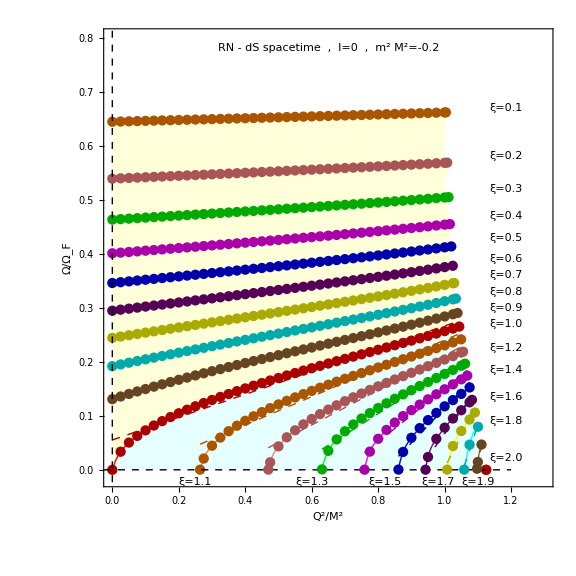

```mathematica
figomrelqm02ext=Show[fill1,plintomrel01q,plomrel01q,pllmfomtabrel01q,plintomrel02q,plomrel02q,pllmfomtabrel02q,plintomrel03q,plomrel03q,pllmfomtabrel03q,plintomrel04q,plomrel04q,pllmfomtabrel04q,plintomrel05q,plomrel05q,pllmfomtabrel05q,plintomrel06q,plomrel06q,pllmfomtabrel06q,plintomrel07q,plomrel07q,pllmfomtabrel07q,plintomrel08q,plomrel08q,pllmfomtabrel08q,plintomrel09q,plomrel09q,pllmfomtabrel09q,plintomrel10q,plomrel10q,pllmfomtabrel10q,plintomrel11q,plomrel11q,pllmfomtabrel11q,plintomrel12q,plomrel12q,pllmfomtabrel12q,plintomrel13q,plomrel13q,pllmfomtabrel13q,plintomrel14q,plomrel14q,pllmfomtabrel14q,plintomrel15q,plomrel15q,pllmfomtabrel15q,plintomrel16q,plomrel16q,pllmfomtabrel16q,plintomrel17q,plomrel17q,pllmfomtabrel17q,plintomrel18q,plomrel18q,pllmfomtabrel18q,plintomrel19q,plomrel19q,pllmfomtabrel19q,plomrel20q,Graphics[{Inset[" RN - dS spacetime  ,  l=0  ,  m^2M^2=-0.2",{0.65,0.78},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["ξ=0.1  ",{1.185,0.67},BaseStyle->{Bold,Darker[Orange],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.2  ",{1.185,0.58},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.3  ",{1.185,0.52},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.4  ",{1.185,0.47},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.5  ",{1.185,0.43},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.6  ",{1.185,0.39},BaseStyle->{Bold,Darker[Purple],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.7  ",{1.185,0.36},BaseStyle->{Bold,Darker[Yellow],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.8  ",{1.185,0.33},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.9  ",{1.185,0.3},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.0  ",{1.185,0.27},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.2  ",{1.185,0.225},BaseStyle->{Bold,Darker[Pink],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.4 ",{1.185,0.185},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.6 ",{1.185,0.135},BaseStyle->{Bold,Darker[Purple],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.8 ",{1.185,0.09},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=2.0 ",{1.185,0.022},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.1 ",{0.25,-0.022},BaseStyle->{Bold,Darker[Orange],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.3 ",{0.6,-0.022},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.5 ",{0.82,-0.022},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.7 ",{0.98,-0.022},BaseStyle->{Bold,Darker[Yellow],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=1.9 ",{1.1,-0.022},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],PlotRange->{{0,1.3},{-0.015,0.8}},Frame->True,FrameLabel->{"Q^2/M^2","Ω/Ω_F"},Axes->None,AspectRatio->1,Epilog->{{Dashed,Black,Line[{{-0.15,0},{1.2,0}}]},{Dashed,Black,Line[{{0,-0.1},{0,1.4}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

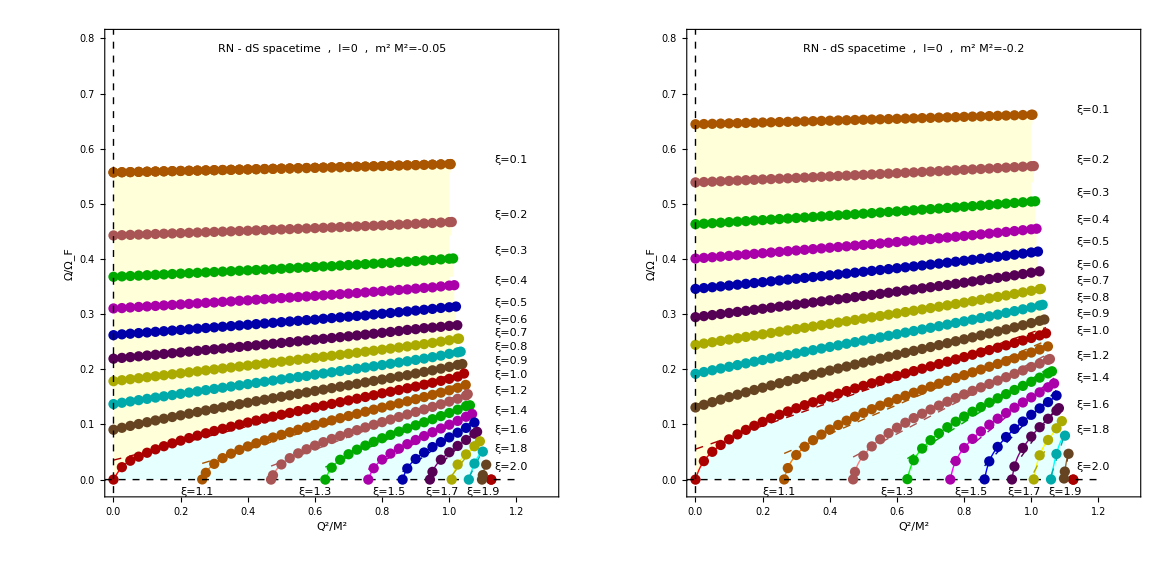

```mathematica
figregrrate=GraphicsGrid[{{figomrelqm005ext,figomrelqm02ext}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"figregrrate.pdf",figregrrate,ImageResolution->1000];
```

## Figure 7

```mathematica
(* Plot of the ξ dependent dimensionless growth rate of the instability Ω M as a function of the scalar  field mass m^2 M^2 (with m(ξ)^2<Subscript[m, cr](ξ)^2=0) for 
dimensionless parameters q^2=Q^2/M^2=0 (SdS spacetime) and q^2=Q^2/M^2=0.3 (RN-dS spacetime) *)
```

```mathematica
(* q^2=0 *)

ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
(* Table obtained from mathsfile: tables_fig7.nb   *)

omtab={{-0.9,0.1,0.63},{-0.8,0.1,0.6159277176398212},{-0.7,0.1,0.5736119723210482},{-0.6,0.1,0.5281415879684933},{-0.5,0.1,0.47868786657022167},{-0.4,0.1,0.423974610754447},{-0.29999999999999993,0.1,0.361853857880984},{-0.19999999999999996,0.1,0.2881426149638662},{-0.09999999999999998,0.1,0.19210990953936216},{-0.9,0.2,0.563723288774924},{-0.8,0.2,0.5287788113464351},{-0.7,0.2,0.4915754894449837},{-0.6,0.2,0.45160869316987384},{-0.5,0.2,0.4081535806258143},{-0.4,0.2,0.36009923924316917},{-0.29999999999999993,0.2,0.30558258555355516},{-0.19999999999999996,0.2,0.240997552110526},{-0.09999999999999998,0.2,0.15723392988572293},{-0.9,0.30000000000000004,0.49412902007510495},{-0.8,0.30000000000000004,0.46299622862168116},{-0.7,0.30000000000000004,0.4298580361667128},{-0.6,0.30000000000000004,0.39426833236640557},{-0.5,0.30000000000000004,0.3555876595280732},{-0.4,0.30000000000000004,0.31283895854149596},{-0.29999999999999993,0.30000000000000004,0.2643883351480686},{-0.19999999999999996,0.30000000000000004,0.2070948095511629},{-0.09999999999999998,0.30000000000000004,0.133136705325335},{-0.9,0.4,0.434441082091276},{-0.8,0.4,0.40670994568313},{-0.7,0.4,0.37719951197464396},{-0.6,0.4,0.34551659976437066},{-0.5,0.4,0.3110972066912488},{-0.4,0.4,0.27308219281621054},{-0.29999999999999993,0.4,0.23004077075250917},{-0.19999999999999996,0.4,0.1792391721709576},{-0.09999999999999998,0.4,0.11395619550113739},{-0.9,0.5,0.37972658506078016},{-0.8,0.5,0.3552215798892315},{-0.7,0.5,0.32915095855491805},{-0.6,0.5,0.3011702145109636},{-0.5,0.5,0.2707870227391671},{-0.4,0.5,0.23725192249858598},{-0.29999999999999993,0.5,0.19932209405796145},{-0.19999999999999996,0.5,0.15463656304785672},{-0.09999999999999998,0.5,0.0974520328743473},{-0.9,0.6,0.3270449779168828},{-0.8,0.6,0.3057393844685126},{-0.7,0.6,0.2830787124205787},{-0.6,0.6,0.2587662235588056},{-0.5,0.6,0.232378454114335},{-0.4,0.6,0.2032726332116724},{-0.29999999999999993,0.6,0.17038631746652963},{-0.19999999999999996,0.6,0.13171174025907606},{-0.09999999999999998,0.6,0.0824008425748148},{-0.9,0.7000000000000001,0.2738729998209404},{-0.8,0.7000000000000001,0.25588261595893397},{-0.7,0.7000000000000001,0.23675301885325753},{-0.6,0.7000000000000001,0.21623605905095303},{-0.5,0.7000000000000001,0.19397823544478462},{-0.4,0.7000000000000001,0.16944405880345895},{-0.29999999999999993,0.7000000000000001,0.14175090159181133},{-0.19999999999999996,0.7000000000000001,0.10923855982852637},{-0.09999999999999998,0.7000000000000001,0.06789809316317608},{-0.9,0.8,0.21693300113345845},{-0.8,0.8,0.20257689249257782},{-0.7,0.8,0.18731592153546672},{-0.6,0.8,0.17095387579468196},{-0.5,0.8,0.153211639835861},{-0.4,0.8,0.13366747151083155},{-0.29999999999999993,0.8,0.11162776998981991},{-0.19999999999999996,0.8,0.08578803735550057},{-0.09999999999999998,0.8,0.05295524321990641},{-0.9,0.9,0.14919846907976966},{-0.8,0.9,0.13925866969054995},{-0.7,0.9,0.1286951106516282},{-0.6,0.9,0.11737311149318692},{-0.5,0.9,0.10510102076424299},{-0.4,0.9,0.09158897648899088},{-0.29999999999999993,0.9,0.0763582461075458},{-0.19999999999999996,0.9,0.05849722211870273},{-0.09999999999999998,0.9,0.03572905360656819}};
```

```mathematica
omtab01=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,2,9}] ,{0,0},1];
```

```mathematica
plom01=ListPlot[omtab01,PlotRange->All,PlotStyle->{Darker[Orange],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtab01= Interpolation[omtab01,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintom01=Plot[intomtab01[mm2],{mm2,-0.8,0},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
omtab02=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,10,18}] ,{0,0},1];
```

```mathematica
plom02=ListPlot[omtab02,PlotRange->All,PlotStyle->{Darker[Red],Dotted,Thick},PlotRange->All];
intomtab02= Interpolation[omtab02,InterpolationOrder->8,Method->"Hermite"];
plintom02=Plot[intomtab02[mm2],{mm2,-0.9,0},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
omtab03=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,19,27}] ,{0,0},1];
plom03=ListPlot[omtab03,PlotRange->All,PlotStyle->{Darker[Green],Dotted,Thick},PlotRange->All];
intomtab03= Interpolation[omtab03,InterpolationOrder->8,Method->"Hermite"];
plintom03=Plot[intomtab03[mm2],{mm2,-0.9,0},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
omtab04=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,28,36}] ,{0,0},1];
plom04=ListPlot[omtab04,PlotRange->All,PlotStyle->{Darker[Magenta],Dotted,Thick},PlotRange->All];
intomtab04= Interpolation[omtab04,InterpolationOrder->8,Method->"Hermite"];
plintom04=Plot[intomtab04[mm2],{mm2,-0.9,0},PlotStyle->{Magenta,Thick},PlotRange->All];
```

```mathematica
omtab05=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,37,45}] ,{0,0},1];
```

```mathematica
plom05=ListPlot[omtab05,PlotRange->All,PlotStyle->{Darker[Blue],Dotted,Thick},PlotRange->All];
intomtab05= Interpolation[omtab05,InterpolationOrder->8,Method->"Hermite"];
plintom05=Plot[intomtab05[mm2],{mm2,-0.9,0},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
omtab06=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,46,54}] ,{0,0},1];
```

```mathematica
plom06=ListPlot[omtab06,PlotRange->All,PlotStyle->{Darker[Purple],Dotted,Thick},PlotRange->All];
intomtab06= Interpolation[omtab06,InterpolationOrder->7,Method->"Hermite"];
plintom06=Plot[intomtab06[mm2],{mm2,-0.9,0},PlotStyle->{Purple,Thick},PlotRange->All];
```

```mathematica
omtab07=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,55,63}] ,{0,0},1];
```

```mathematica
plom07=ListPlot[omtab07,PlotRange->All,PlotStyle->{Darker[Yellow],Dotted,Thick},PlotRange->All];
intomtab07= Interpolation[omtab07,InterpolationOrder->7,Method->"Hermite"];
plintom07=Plot[intomtab07[mm2],{mm2,-0.9,0},PlotStyle->{Yellow,Thick},PlotRange->All];
```

```mathematica
omtab08=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,64,72}] ,{0,0},1];
plom08=ListPlot[omtab08,PlotRange->All,PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->All];
intomtab08= Interpolation[omtab08,InterpolationOrder->7,Method->"Hermite"];
plintom08=Plot[intomtab08[mm2],{mm2,-0.9,0},PlotStyle->{Cyan,Thick},PlotRange->All];
```

```mathematica
omtab09=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,73,81}] ,{0,0},1];
plom09=ListPlot[omtab09,PlotRange->All,PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->All];
intomtab09= Interpolation[omtab09,InterpolationOrder->7,Method->"Hermite"];
plintom09=Plot[intomtab09[mm2],{mm2,-0.9,0},PlotStyle->{Brown,Thick},PlotRange->All];
```

```mathematica
plotomegaflat=Plot[(-mm2)^0.5,{mm2,0,-0.45},PlotStyle->{RGBColor[0.1,0.5,0.2],Dashed,Thickness[0.004]},PlotRange->All];
```

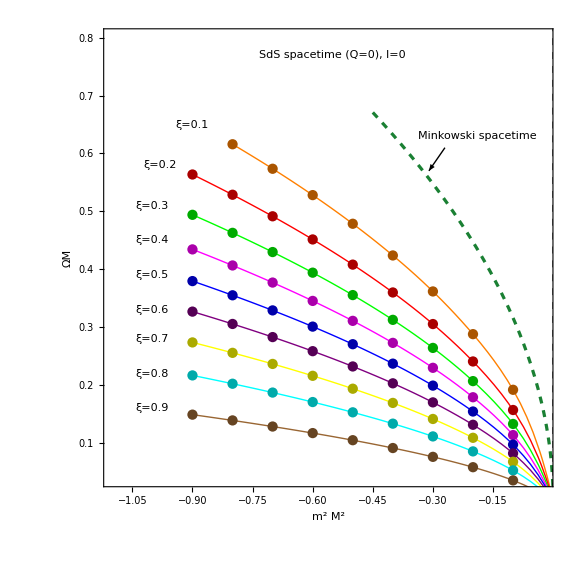

```mathematica
figomq0=Show[plintom01,plom01,plintom02,plom02,plintom03,plom03,plintom04,plom04,plintom05,plom05,plintom06,plom06,plintom07,plom07,plintom08,plom08,plintom09,plom09,plotomegaflat,Graphics[{Inset[" SdS spacetime (Q=0), l=0 ",{-0.55,0.77},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" Minkowski spacetime",{-0.19,0.63},BaseStyle->{Italic,Bold,RGBColor[0.1,0.5,0.2],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.1  ",{-0.9,0.65},BaseStyle->{Bold,Darker[Orange],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.2  ",{-0.98,0.58},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.3  ",{-1,0.51},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.4  ",{-1,0.45},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.5  ",{-1,0.39},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.6  ",{-1,0.33},BaseStyle->{Bold,Darker[Purple],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.7  ",{-1,0.28},BaseStyle->{Bold,Darker[Yellow],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.8  ",{-1,0.22},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.9  ",{-1,0.16},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],PlotRange->{{-1.1,-0.022},{0.04,0.8}},Frame->True,FrameLabel->{"m^2 M^2","ΩΜ"},Axes->None,AspectRatio->1,Epilog->{{Thin,Black,Arrowheads[0.02],Arrow[{{-0.27,0.61},{-0.31,0.57}}]},{Dashed,Black,Line[{{-0.15,0},{0.2,0}}]},{Dashed,Black,Line[{{0,-0.1},{0,1.4}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

```mathematica
(* q^2=0.3 *)
```

```mathematica
(* Table obtained from mathsfile: tables_fig7.nb   *)

omtab={{-0.9,0.1,0.5810646281340827},{-0.8,0.1,0.5408823431286177},{-0.7,0.1,0.5777743359936142},{-0.6,0.1,0.531989431488235},{-0.5,0.1,0.48219162700802326},{-0.4,0.1,0.427094474252389},{-0.29999999999999993,0.1,0.36453362314583987},{-0.19999999999999996,0.1,0.29029053989276593},{-0.09999999999999998,0.1,0.1935398649152649},{-0.9,0.2,0.5719873679154935},{-0.8,0.2,0.5365487758118498},{-0.7,0.2,0.4988178072606689},{-0.6,0.2,0.45828209509026835},{-0.5,0.2,0.41420577617006044},{-0.4,0.2,0.3654601665068474},{-0.29999999999999993,0.2,0.31015175781337506},{-0.19999999999999996,0.2,0.24461417455909615},{-0.09999999999999998,0.2,0.15957990200452973},{-0.9,0.30000000000000004,0.5059420975201175},{-0.8,0.30000000000000004,0.47408563285328914},{-0.7,0.30000000000000004,0.44017523955001503},{-0.6,0.30000000000000004,0.4037542109376699},{-0.5,0.30000000000000004,0.3641667428729699},{-0.4,0.30000000000000004,0.32040966471284027},{-0.29999999999999993,0.30000000000000004,0.27080715452167126},{-0.19999999999999996,0.30000000000000004,0.21213364651315314},{-0.09999999999999998,0.30000000000000004,0.13635380993515422},{-0.9,0.4,0.45007940283901604},{-0.8,0.4,0.4213723744145167},{-0.7,0.4,0.39082170508078545},{-0.6,0.4,0.3580185588253313},{-0.5,0.4,0.3223783539008938},{-0.4,0.4,0.28300848825477676},{-0.29999999999999993,0.4,0.23842284345143164},{-0.19999999999999996,0.4,0.1857790569747418},{-0.09999999999999998,0.4,0.11808662752653529},{-0.9,0.5,0.39971271756906607},{-0.8,0.5,0.37394079895804855},{-0.7,0.5,0.3465202337123131},{-0.6,0.5,0.3170878325787464},{-0.5,0.5,0.2851234987504292},{-0.4,0.5,0.24983651846677948},{-0.29999999999999993,0.5,0.20991420690845214},{-0.19999999999999996,0.5,0.16286069617140844},{-0.09999999999999998,0.5,0.10260616411973847},{-0.9,0.6,0.3522530878172104},{-0.8,0.6,0.3293283574840505},{-0.7,0.6,0.3049430150027529},{-0.6,0.6,0.27877692734660436},{-0.5,0.6,0.25037272754293144},{-0.4,0.6,0.2190358111327218},{-0.29999999999999993,0.6,0.18361745153069503},{-0.19999999999999996,0.6,0.14194520507107672},{-0.09999999999999998,0.6,0.08877996998397975},{-0.9,0.7000000000000001,0.30581417160856406},{-0.8,0.7000000000000001,0.2857476061775281},{-0.7,0.7000000000000001,0.26440803126348467},{-0.6,0.7000000000000001,0.24151785543443494},{-0.5,0.7000000000000001,0.2166806548218688},{-0.4,0.7000000000000001,0.1892964353379041},{-0.29999999999999993,0.7000000000000001,0.15837554069275095},{-0.19999999999999996,0.7000000000000001,0.12205548909138891},{-0.09999999999999998,0.7000000000000001,0.07586359864610238},{-0.9,0.8,0.25854280196258633},{-0.8,0.8,0.24145344985633502},{-0.7,0.8,0.22328474360367015},{-0.6,0.8,0.20380213816428436},{-0.5,0.8,0.1826717976523139},{-0.4,0.8,0.1593891123246577},{-0.29999999999999993,0.8,0.13312434495101869},{-0.19999999999999996,0.8,0.10232076642468362},{-0.09999999999999998,0.8,0.06322626924152057},{-0.9,0.9,0.2078735523973001},{-0.8,0.9,0.1940426011693295},{-0.7,0.9,0.17934178904100942},{-0.6,0.9,0.16358309534728807},{-0.5,0.9,0.14649917662381723},{-0.4,0.9,0.1276864959392639},{-0.29999999999999993,0.9,0.10648252308923062},{-0.19999999999999996,0.9,0.08164323199323693},{-0.09999999999999998,0.9,0.050118244222640496}};
```

```mathematica
omtab01=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,3,9}] ,{0,0},1];
```

```mathematica
plom01=ListPlot[omtab01,PlotRange->All,PlotStyle->{Darker[Orange],Dotted,Thick},PlotRange->All];
```

```mathematica
intomtab01= Interpolation[omtab01,InterpolationOrder->7,Method->"Hermite"];
```

```mathematica
plintom01=Plot[intomtab01[mm2],{mm2,-0.7,0},PlotStyle->{Orange,Thick},PlotRange->All];
```

```mathematica
omtab02=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,10,18}] ,{0,0},1];
```

```mathematica
plom02=ListPlot[omtab02,PlotRange->All,PlotStyle->{Darker[Red],Dotted,Thick},PlotRange->All];
intomtab02= Interpolation[omtab02,InterpolationOrder->3,Method->"Hermite"];
plintom02=Plot[intomtab02[mm2],{mm2,-0.9,0},PlotStyle->{Red,Thick},PlotRange->All];
```

```mathematica
omtab03=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,19,27}] ,{0,0},1];
```

```mathematica
plom03=ListPlot[omtab03,PlotRange->All,PlotStyle->{Darker[Green],Dotted,Thick},PlotRange->All];
intomtab03= Interpolation[omtab03,InterpolationOrder->3,Method->"Hermite"];
plintom03=Plot[intomtab03[mm2],{mm2,-0.9,0},PlotStyle->{Green,Thick},PlotRange->All];
```

```mathematica
omtab04=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,28,36}] ,{0,0},1];
```

```mathematica
plom04=ListPlot[omtab04,PlotRange->All,PlotStyle->{Darker[Magenta],Dotted,Thick},PlotRange->All];
intomtab04= Interpolation[omtab04,InterpolationOrder->8,Method->"Hermite"];
plintom04=Plot[intomtab04[mm2],{mm2,-0.9,0},PlotStyle->{Magenta,Thick},PlotRange->All];
```

```mathematica
omtab05=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,37,45}] ,{0,0},1];
```

```mathematica
plom05=ListPlot[omtab05,PlotRange->All,PlotStyle->{Darker[Blue],Dotted,Thick},PlotRange->All];
intomtab05= Interpolation[omtab05,InterpolationOrder->8,Method->"Hermite"];
plintom05=Plot[intomtab05[mm2],{mm2,-0.9,0},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
omtab06=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,46,54}] ,{0,0},1];
```

```mathematica
plom06=ListPlot[omtab06,PlotRange->All,PlotStyle->{Darker[Purple],Dotted,Thick},PlotRange->All];
intomtab06= Interpolation[omtab06,InterpolationOrder->7,Method->"Hermite"];
plintom06=Plot[intomtab06[mm2],{mm2,-0.9,0},PlotStyle->{Purple,Thick},PlotRange->All];
```

```mathematica
omtab07=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,55,63}] ,{0,0},1];
```

```mathematica
plom07=ListPlot[omtab07,PlotRange->All,PlotStyle->{Darker[Yellow],Dotted,Thick},PlotRange->All];
intomtab07= Interpolation[omtab07,InterpolationOrder->7,Method->"Hermite"];
plintom07=Plot[intomtab07[mm2],{mm2,-0.9,0},PlotStyle->{Yellow,Thick},PlotRange->All];
```

```mathematica
omtab08=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,64,72}] ,{0,0},1];
plom08=ListPlot[omtab08,PlotRange->All,PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->All];
intomtab08= Interpolation[omtab08,InterpolationOrder->7,Method->"Hermite"];
plintom08=Plot[intomtab08[mm2],{mm2,-0.9,0},PlotStyle->{Cyan,Thick},PlotRange->All];
```

```mathematica
omtab09=Insert[Table[{omtab[[i,1]],omtab[[i,3]]},{i,73,81}] ,{0,0},1];
plom09=ListPlot[omtab09,PlotRange->All,PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->All];
intomtab09= Interpolation[omtab09,InterpolationOrder->7,Method->"Hermite"];
plintom09=Plot[intomtab09[mm2],{mm2,-0.9,0},PlotStyle->{Brown,Thick},PlotRange->All];
```

```mathematica
plotomegaflat=Plot[(-mm2)^0.5,{mm2,0,-0.45},PlotStyle->{RGBColor[0.1,0.5,0.2],Dashed,Thickness[0.004]},PlotRange->All];
```

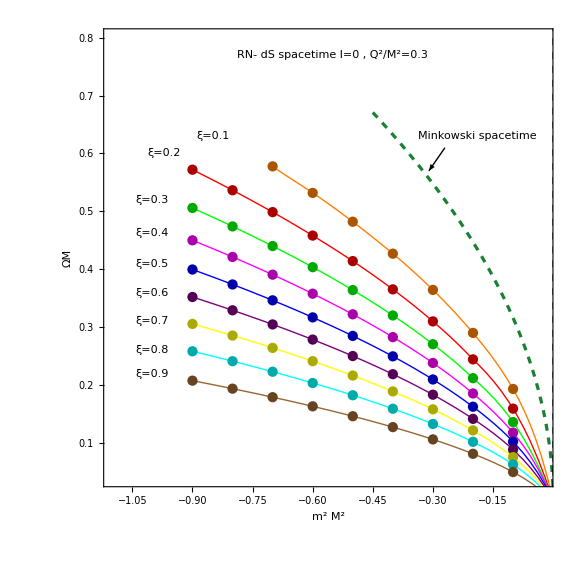

```mathematica
figomq03=Show[plintom01,plom01,plintom02,plom02,plintom03,plom03,plintom04,plom04,plintom05,plom05,plintom06,plom06,plintom07,plom07,plintom08,plom08,plintom09,plom09,plotomegaflat,Graphics[{Inset[" RN- dS spacetime l=0 , Q^2/M^2=0.3",{-0.55,0.77},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" Minkowski spacetime",{-0.19,0.63},BaseStyle->{Italic,Bold,RGBColor[0.1,0.5,0.2],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.1  ",{-0.85,0.63},BaseStyle->{Bold,Darker[Orange],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.2  ",{-0.97,0.6},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.3  ",{-1,0.52},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.4  ",{-1,0.463},BaseStyle->{Bold,Darker[Magenta],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.5  ",{-1,0.41},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.6  ",{-1,0.36},BaseStyle->{Bold,Darker[Purple],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.7  ",{-1,0.31},BaseStyle->{Bold,Darker[Yellow],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.8  ",{-1,0.26},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["ξ=0.9  ",{-1,0.22},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],PlotRange->{{-1.1,-0.022},{0.04,0.8}},Frame->True,FrameLabel->{"m^2 M^2","ΩΜ"},Axes->None,AspectRatio->1,Epilog->{{{Thin,Black,Arrowheads[0.02],Arrow[{{-0.27,0.61},{-0.31,0.57}}]},Dashed,Black,Line[{{-0.15,0},{0.2,0}}]},{Dashed,Black,Line[{{0,-0.1},{0,1.4}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

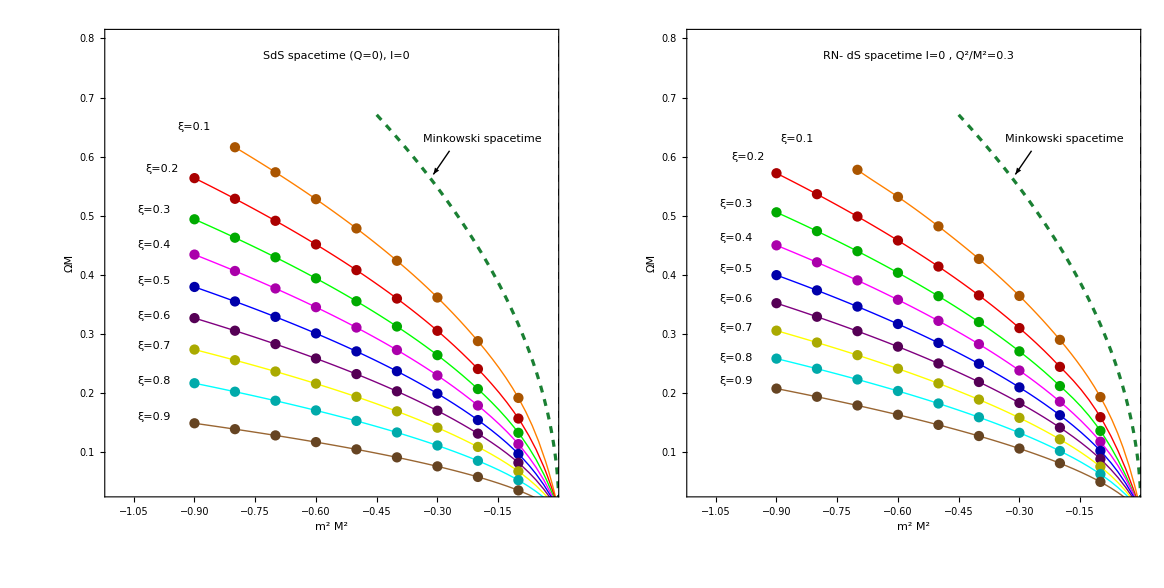

```mathematica
figom4q=GraphicsGrid[{{figomq0,figomq03}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"figom4q.pdf",figom4q,ImageResolution->1000];
```

## Figure 8 Pure deSitter background

```mathematica
(*  Plots of the m^2/Λ dependent Regge-Wheeler dimensionless potentials V/Λ  and  V_*/Λ  as a function of r √Λ and r_*√Λ respectively in the case 
of the deSitter spacetime (M=0, ξ=0) with angular scale l=0. The green solid curves correspond to the  critical value of the scalar field mass
 Subscript[m, cr]^2/Λ = 0.  The curves with m^2/Λ > 0 and m^2/Λ < 0 correspond to non-existence of bound states (stabilities) and existence of bound states 
(instabilities) respectively *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
```

```mathematica
Clear[ll,mm2]
A=2-mm2 l1^2;
B=0;
l1=Sqrt[3/ll];
vv[r_]:=-A/(l1^2 Cosh[r/l1]^2)+B/(l1^2 Sinh[r/l1]^2);
vv[r]//Simplify
Series[-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2,{r,0,2}];
```

-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2

```mathematica
ll=1;mm2=0;
plvrtdszero=Plot[vv[r],{r,0,5},PlotRange->All,AxesLabel->{"r_*√Λ","V_*(r_*√Λ)"},PlotStyle->{Darker[Green],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
eq1=D[u[x],{x,2}]-vv[x]u[x]==0;
xmin=0.0;
xmax=30;
bc1=u[xmin]==0;
bc2=u'[xmin]==1;
sol=NDSolve[{eq1,bc1,bc2},u,{x,xmin,xmax}]
Plot[Evaluate[u[x]/.sol],{x,xmin,xmax},PlotRange->All];
Evaluate[u'[xmax]/.sol]
```

{{u→InterpolatingFunction[{{0., 30.}}, <>]}}

{1.16773×10^-8}

```mathematica
ll=1;mm2=-2/3;
plvrtdsneg=Plot[vv[r],{r,0,5},PlotRange->All,AxesLabel->{"r_*√Λ","V(r_*√Λ)"},PlotStyle->{Darker[Red],Dashing[0.02],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ll=1;mm2=2/3;
plvrtdspos=Plot[vv[r],{r,0,5},PlotRange->All,AxesLabel->{"r_*√Λ","V(r_*√Λ)"},PlotStyle->{Darker[Red],Dotted,Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ll=1;mm2=-1;
plvrtdsnegb=Plot[vv[r],{r,0,5},PlotRange->All,AxesLabel->{"r_*√Λ","V(r_*√Λ)"},PlotStyle->{Green,Dashing[0.02],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
ll=1;mm2=1;
plvrtdsposb=Plot[vv[r],{r,0,5},PlotRange->All,AxesLabel->{"r_*√Λ","V(r_*√Λ)"},PlotStyle->{Green,Dotted,Thick},AspectRatio->1,ImageSize->Medium];
```

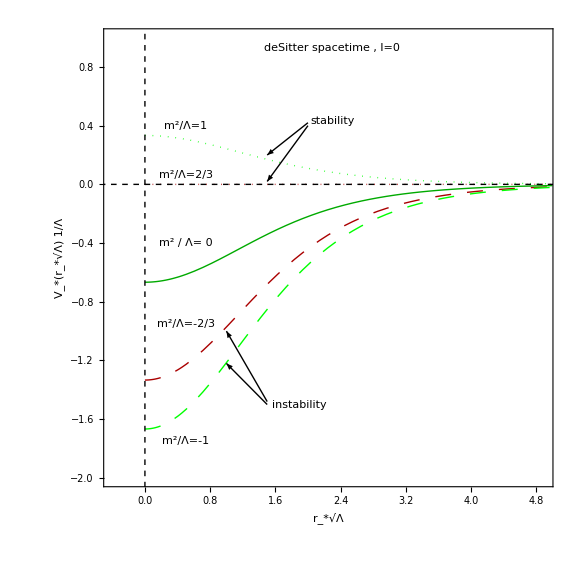

```mathematica
splvrtds=Show[plvrtdsneg,plvrtdspos,plvrtdsnegb,plvrtdsposb,plvrtdszero,Graphics[{Inset[" deSitter spacetime , l=0 ",{2.3,0.93},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" stability",{2.3,0.43},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" instability",{1.9,-1.5},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["  m^2 / Λ= 0 ",{0.5,-0.4},BaseStyle->{Bold,Darker[Green],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2/Λ=2/3 ",{0.5,0.067},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2/Λ=1",{0.5,0.4},BaseStyle->{Bold,Green,FontFamily->"Times",14}]}],Graphics[{Inset[" m^2/Λ=-2/3 ",{0.5,-0.95},BaseStyle->{Bold,Darker[Red],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2/Λ=-1 ",{0.5,-1.75},BaseStyle->{Bold,Green,FontFamily->"Times",14}]}],Epilog->{{Thin,Black,Arrowheads[0.01],Arrow[{{1.5,-1.5},{1.,-1.22}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{1.5,-1.48},{1.,-1}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{2,0.42},{1.5,0.2}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{2,0.4},{1.5,0.02}}]},{Dashing[0.007],Black,Line[{{0,-4},{0,4}}]},{Dashing[0.007],Black,Line[{{-20,0},{40,0}}]}},Frame->True,FrameLabel->{"r_*√Λ","V_*(r_*√Λ) 1/Λ"},Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-0.4,4.9},{-2,1.}},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"splvrtds.pdf",splvrtds,ImageResolution->1000];
```

## Figure 9 Pure deSitter background

```mathematica
(* Plot of the dimensionless growth rate of the instability Ω/√Λ as a function of the scalar field mass m^2/Λ (with m^2<Subscript[m, cr]^2=0) in the case of 
deSitter spacetime *)
```

-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2

-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2

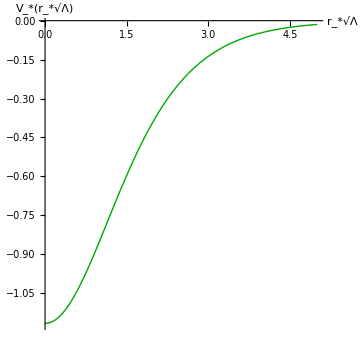

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
Clear[ll,mm2]
A=2-mm2 l1^2;
B=0;
l1=Sqrt[3/ll];
vv[r_]:=-A/(l1^2 Cosh[r/l1]^2)+B/(l1^2 Sinh[r/l1]^2);
vv[r]//Simplify
Series[-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2,{r,0,2}];
-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2
ll=1;mm2=-0.5;
plvrtdszero=Plot[vv[r],{r,0,5},PlotRange->All,AxesLabel->{"r_*√Λ","V_*(r_*√Λ)"},PlotStyle->{Darker[Green],Thick},AspectRatio->1,ImageSize->Medium]
```

0.252008

0.356394

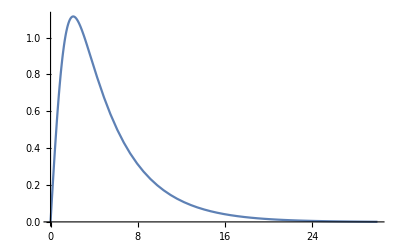

```mathematica
eqnp=D[u[x],{x,2}]-vv[x]u[x]-om^2 u[x];
xmin=0.0;
xmax=30;
bc1=u[xmin]==0;
bc2=u'[xmin]==1;

psol[om_?NumericQ]:=u/.First@NDSolve[{eqnp==0,bc1,bc2},u,{x,xmin,xmax}];
omeg=FindRoot[psol[om][xmax]==Exp[-om xmax],{om,1}][[1,2]]
omfl=Sqrt[-mm2];
omrel=omeg/omfl

usol=NDSolve[{eqnp==0 /. om->omeg,u[xmin]==0/. om->omeg,u'[xmin]==1/. om->omeg},u,{x,xmin,xmax}];
Plot[Evaluate[u[x]/. usol],{x,xmin,xmax},PlotRange->All]
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]
A=2-mm2 l1^2;
B=0;
```

```mathematica
omtab={};
omtabrel={};
```

```mathematica
l1=Sqrt[3/ll];
vv[r_]:=-A/(l1^2 Cosh[r/l1]^2)+B/(l1^2 Sinh[r/l1]^2);
vv[r]//Simplify
Series[-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2,{r,0,2}];
-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2
mm2=-1;
```

-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2

-1/3 (2 ll-3 mm2) Sech[r/(√3 √(1/ll))]^2

```mathematica
Do[
ll=1;

eqnp=D[u[x],{x,2}]-vv[x]u[x]-om^2 u[x];
xmin=0.0;
xmax=30;
bc1=u[xmin]==0;
bc2=u'[xmin]==1;

psol[om_?NumericQ]:=u/.First@NDSolve[{eqnp==0,bc1,bc2},u,{x,xmin,xmax}];
omeg=FindRoot[psol[om][xmax]==Exp[-om xmax],{om,1}][[1,2]];

usol=NDSolve[{eqnp==0 /. om->omeg,u[xmin]==0/. om->omeg,u'[xmin]==1/. om->omeg},u,{x,xmin,xmax}];

omrel=omeg/Sqrt[-mm2];
AppendTo[omtab,{mm2,omeg}];
AppendTo[omtabrel,{mm2,omrel}];

Print[mm2,"  ",omeg,"   ",ll],{mm2,-1.5,-0.05,0.05}]
```

-1.5  0.633975   1

-1.45  0.617214   1

-1.4  0.600262   1

-1.35  0.583112   1

-1.3  0.565757   1

-1.25  0.548188   1

-1.2  0.530399   1

-1.15  0.512379   1

-1.1  0.494122   1

-1.05  0.475615   1

-1.  0.45685   1

-0.95  0.437815   1

-0.9  0.418498   1

-0.85  0.398886   1

-0.8  0.378965   1

-0.75  0.358719   1

-0.7  0.338134   1

-0.65  0.317191   1

-0.6  0.29587   1

-0.55  0.27415   1

-0.5  0.252008   1

-0.45  0.229419   1

-0.4  0.206353   1

-0.35  0.182777   1

-0.3  0.158649   1

-0.25  0.133906   1

-0.2  0.108423   1

-0.15  0.0818943   1

-0.1  0.0534301   1

-0.05  0.0201923   1

```mathematica
omtab.08
```

{{-1.5 .08,0.633975 .08},{-1.45 .08,0.617214 .08},{-1.4 .08,0.600262 .08},{-1.35 .08,0.583112 .08},{-1.3 .08,0.565757 .08},{-1.25 .08,0.548188 .08},{-1.2 .08,0.530399 .08},{-1.15 .08,0.512379 .08},{-1.1 .08,0.494122 .08},{-1.05 .08,0.475615 .08},{-1. .08,0.45685 .08},{-0.95 .08,0.437815 .08},{-0.9 .08,0.418498 .08},{-0.85 .08,0.398886 .08},{-0.8 .08,0.378965 .08},{-0.75 .08,0.358719 .08},{-0.7 .08,0.338134 .08},{-0.65 .08,0.317191 .08},{-0.6 .08,0.29587 .08},{-0.55 .08,0.27415 .08},{-0.5 .08,0.252008 .08},{-0.45 .08,0.229419 .08},{-0.4 .08,0.206353 .08},{-0.35 .08,0.182777 .08},{-0.3 .08,0.158649 .08},{-0.25 .08,0.133906 .08},{-0.2 .08,0.108423 .08},{-0.15 .08,0.0818943 .08},{-0.1 .08,0.0534301 .08},{-0.05 .08,0.0201923 .08}}

```mathematica
omtabrel
```

{{-1.5,0.517638},{-1.45,0.512569},{-1.4,0.507314},{-1.35,0.501863},{-1.3,0.496201},{-1.25,0.490314},{-1.2,0.484185},{-1.15,0.477796},{-1.1,0.471127},{-1.05,0.464153},{-1.,0.45685},{-0.95,0.449189},{-0.9,0.441135},{-0.85,0.432652},{-0.8,0.423695},{-0.75,0.414214},{-0.7,0.404147},{-0.65,0.393426},{-0.6,0.381966},{-0.55,0.369664},{-0.5,0.356394},{-0.45,0.341998},{-0.4,0.326273},{-0.35,0.30895},{-0.3,0.289652},{-0.25,0.267811},{-0.2,0.242442},{-0.15,0.21145},{-0.1,0.168961},{-0.05,0.0903029}}

```mathematica
plom=ListPlot[omtab,PlotRange->All,PlotStyle->{Red,Dotted,Thick},PlotRange->All];
```

```mathematica
intomtab= Interpolation[omtab,InterpolationOrder->3,Method->"Hermite"];
```

```mathematica
plintom=Plot[intomtab[mm2],{mm2,-1.5,-0.05},PlotStyle->{Blue,Thick},PlotRange->All];
```

```mathematica
plotomegaflat=Plot[(-mm2)^0.5,{mm2,-1.,0},PlotStyle->{RGBColor[0.1,0.5,0.2],Dashed,Thickness[0.004]},PlotRange->All];
```

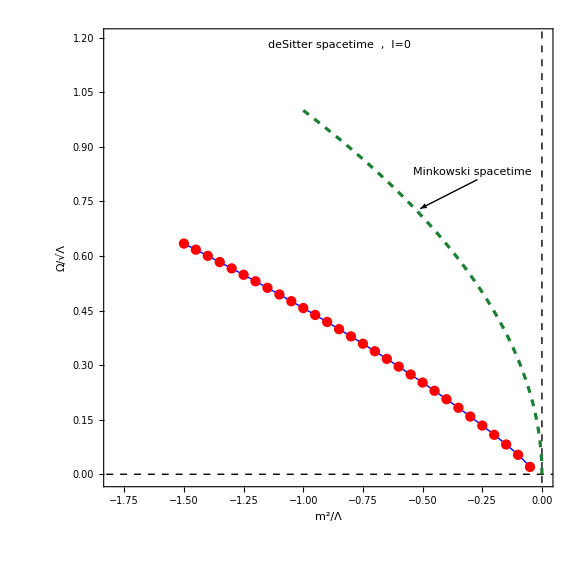

```mathematica
figomds=Show[plintom,plom,plotomegaflat,Graphics[{Inset[" deSitter spacetime  ,  l=0  ",{-0.85,1.18},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset[" Minkowski spacetime",{-0.29,0.83},BaseStyle->{Italic,Bold,RGBColor[0.1,0.5,0.2],FontFamily->"Times",14}]}],PlotRange->{{-1.8,0.01},{-0.01,1.2}},Frame->True,FrameLabel->{"m^2/Λ","Ω/√Λ"},Axes->None,AspectRatio->1,Epilog->{{Thin,Black,Arrowheads[0.02],Arrow[{{-0.27,0.81},{-0.51,0.73}}]},{Dashed,Black,Line[{{-2,0},{1.2,0}}]},{Dashed,Black,Line[{{0,-0.1},{0,1.4}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->Large]
```

```mathematica
Export[NotebookDirectory[]<>"figomds.pdf",figomds,ImageResolution->1000];
```

## Figure 10 Pure Schwarzschild background

```mathematica
(*  Plots of the m^2 Μ^2 dependent Regge-Wheeler potentials V  and  V_*  as a function of r/M and r*/M respectively in the case of the Schwarzschild 
spacetime (Λ=0, ξ=0) with angular scale l=0. The blue solid curves correspond to the critical value of the scalar field mass Subscript[m, cr]^2 Μ^2=0 .  The 
curves with m^2 Μ^2> 0 and m^2 Μ^2< 0 correspond to non-existence of bound states (stabilities) and existence of bound states (instabilities) 
respectively *)
```

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"]

Clear[aa,kk,s,ll,m,mm2]

(* Metric function f *)
aa[r_]:=(1-2*m/r-ll *r^2/3);

(*  Regge-Wheeler potential V  *)
V[r_,m_,ll_,l_,mm2_]:=(1-2*m/r-ll/3 *r^2)*(l*(l+1)/r^2+2*m/r^3-2*ll/3+mm2);
```

```mathematica
plvrshzero=Plot[V[r,1,0,0,0],{r,0,59},  PlotStyle->{Darker[Blue],Thick},PlotRange->{{0,59},{-0.08,0.1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvrshneg=Plot[V[r,1,0,0,-0.01615],{r,0,59},  PlotStyle->{Darker[Brown],Dashing[0.02],Thick},PlotRange->{{0,59},{-0.08,0.1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvrshnegb=Plot[V[r,1,0,0,-0.032],{r,0,59},  PlotStyle->{Darker[Cyan],Dashing[0.02],Thick},PlotRange->{{0,59},{-0.08,0.1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvrshpos=Plot[V[r,1,0,0,0.01615],{r,0,59},  PlotStyle->{Darker[Brown],Dotted,Thick},PlotRange->{{0,59},{-0.08,0.1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
plvrshposb=Plot[V[r,1,0,0,0.032],{r,0,59},  PlotStyle->{Darker[Cyan],Dotted,Thick},PlotRange->{{0,59},{-0.08,0.1}},AxesLabel->{"r","V(r)"},BaseStyle->{FontFamily->"Times",18},ImageSize->Large];
```

```mathematica
m=1;ll=0;


rt[r_]=r+2*m*Log[r/(2*m)-1];
plvrtshzero=ParametricPlot[{rt[r],V[r,1,0,0,0]},{r,0,60}, PlotRange->{{-15,50},{-0.1,0.1}},AxesLabel->{"r*/M","V(r*)"},PlotStyle->{Darker[Blue],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
m=1;ll=0;

rt[r_]=r+2*m*Log[r/(2*m)-1];
plvrtshneg=ParametricPlot[{rt[r],V[r,1,0,0,-0.01615]},{r,0,60}, PlotRange->{{-15,50},{-0.1,0.1}},AxesLabel->{"r*/M","V(r*)"},PlotStyle->{Darker[Brown],Dashing[0.02],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
plvrtshnegb=ParametricPlot[{rt[r],V[r,1,0,0,-0.032]},{r,0,60}, PlotRange->{{-15,50},{-0.1,0.1}},AxesLabel->{"r*/M","V(r*)"},PlotStyle->{Darker[Cyan],Dashing[0.02],Thick},AspectRatio->1,ImageSize->Medium];
```

```mathematica
plvrtshpos=ParametricPlot[{rt[r],V[r,1,0,0,0.01615]},{r,0,60}, PlotRange->{{-15,50},{-0.1,0.1}},AxesLabel->{"r*/M","V(r*)"},PlotStyle->{Thick,Darker[Brown],Dotted},AspectRatio->1,ImageSize->Medium];
```

```mathematica
plvrtshposb=ParametricPlot[{rt[r],V[r,1,0,0,0.032]},{r,0,60}, PlotRange->{{-15,50},{-0.1,0.1}},AxesLabel->{"r*/M","V(r*)"},PlotStyle->{Thick,Darker[Cyan],Dotted},AspectRatio->1,ImageSize->Medium];
```

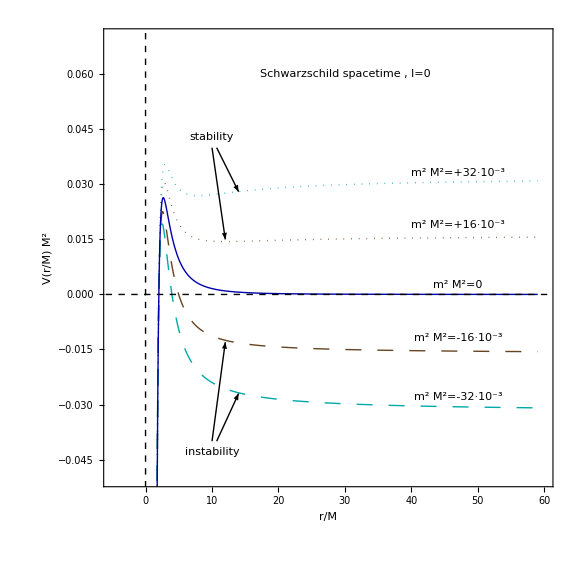

```mathematica
splvrsh=Show[plvrshneg,plvrshpos,plvrshnegb,plvrshposb,plvrshzero,Graphics[{Inset[" Schwarzschild spacetime , l=0 ",{30,0.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["stability ",{10 ,0.043},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["instability ",{10 ,-0.043},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["m^2Μ^2=0 ",{47,0.0025},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset["m^2Μ^2=-16·10^-3 ",{47,-0.012},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],Graphics[{Inset["m^2Μ^2=-32·10^-3 ",{47,-0.028},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset["m^2Μ^2=+16·10^-3 ",{47 ,0.019},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],Graphics[{Inset["m^2Μ^2=+32·10^-3 ",{47 ,0.033},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Frame->True,FrameLabel->{"r/M","V(r/M) M^2"},Axes->None,AspectRatio->1,Epilog->{{Thin,Black,Arrowheads[0.01],Arrow[{{10,-0.04},{12,-0.013}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{10.7,-0.04},{14,-0.027}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{10.7,0.04},{14,0.028}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{10,0.04},{12,0.015}}]},{Dashing[0.008],Black,Line[{{-6,0},{70,0}}]},{Dashing[0.008],Black,Line[{{0,-1},{0,1}}]}},FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-5,60},{-0.05,0.07}},ImageSize->Large]
```

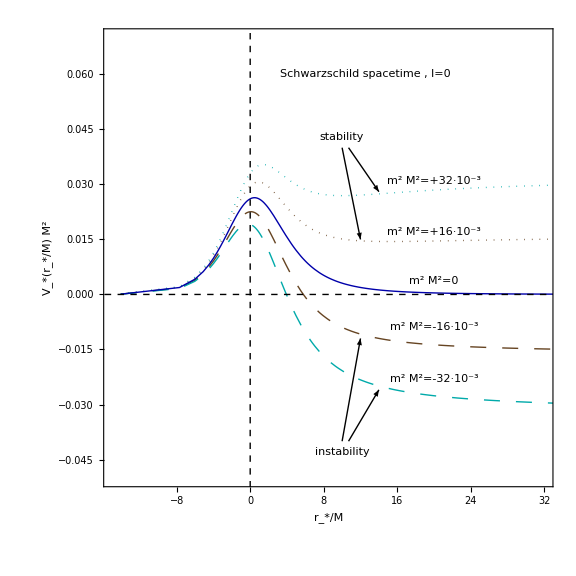

```mathematica
splvrtsh=Show[plvrtshneg,plvrtshpos,plvrtshnegb,plvrtshposb,plvrtshzero,Graphics[{Inset[" Schwarzschild spacetime , l=0 ",{12.5,0.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",18}]}],Graphics[{Inset["stability ",{10 ,0.043},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["instability ",{10 ,-0.043},BaseStyle->{Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" m^2Μ^2=0 ",{20,0.0038},BaseStyle->{Bold,Darker[Blue],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2Μ^2=+32·10^-3 ",{20,0.031},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2Μ^2=+16·10^-3 ",{20,0.017},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2Μ^2=-16·10^-3 ",{20,-0.009},BaseStyle->{Bold,Darker[Brown],FontFamily->"Times",14}]}],Graphics[{Inset[" m^2Μ^2=-32·10^-3 ",{20,-0.023},BaseStyle->{Bold,Darker[Cyan],FontFamily->"Times",14}]}],Epilog->{{Thin,Black,Arrowheads[0.01],Arrow[{{10,-0.04},{12,-0.012}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{10.7,-0.04},{14,-0.026}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{10.7,0.04},{14,0.028}}]},{Thin,Black,Arrowheads[0.01],Arrow[{{10,0.04},{12,0.015}}]},{Dashing[0.008],Black,Line[{{0,-1},{0,1}}]},{Dashing[0.008],Black,Line[{{-20,0},{40,0}}]}},Frame->True,FrameLabel->{"r_*/M","V_*(r_*/M) M^2"},Axes->None,AspectRatio->1,FrameStyle->Directive[Black,Thick],BaseStyle->{Large,Bold,Italic,FontFamily->"Times",18},PlotRange->{{-15,32},{-0.05,0.07}},ImageSize->Large]
```

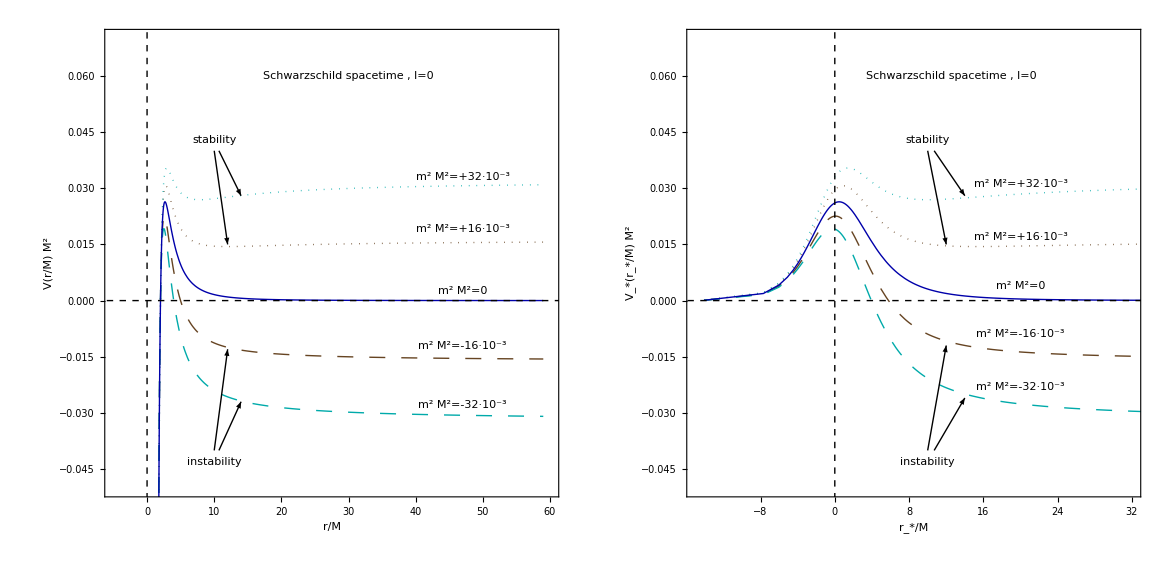

```mathematica
splvrvrtsh=GraphicsGrid[{{splvrsh,splvrtsh}},Spacings->0]
```

```mathematica
Export[NotebookDirectory[]<>"splvrvrtsh.pdf",splvrvrtsh,ImageResolution->1000];
```